### Dynamical Phase for general n dimensions

```mathematica
(*Clear all values assigned to ket1,ket2,...,ketn*)
Clear[Evaluate[Table["ket"<>ToString[i],{i,1,n}]]]
Clear[ket]
```

```mathematica
n=5;  (*Define n,the number of elements in the ket vector*)
(*Generate the ket vector with n elements:{ket1,ket2,...,ketn}*)
ket=Table[Symbol["ket"<>ToString[i]],{i,1,n}];
(*Display the generated ket vector*)
ket
(*Define parameters E1,E2,and t*)
En=Table[Symbol["E"<>ToString[i]],{i,1,n}];
 (*Energy values*)
t=t;        (*Time variable*)

(*Create the matrix*)
Upmns=Array[Symbol["U"<>ToString[#1]<>ToString[#2]]&,{n,n}];

(*Initialize the kett vector*)
kett=Table[0,{i,n}]; (*To hold the transformed elements*)
psi=Table[0,{i,n}]; (*To hold the transformed elements*)
psit=Table[0,{i,n}]; (*To hold the transformed elements*)
(*Use a loop to define the elements of kett*)
For[i=1,i<=Length[ket],i++,kett[[i]]=ket[[i]]*Exp[-I*En[[i]]*t];];
(*Display the result*)
kett
(*Defining the mixed states at time t*)
For[i=1,i<=Length[ket],i++,{psi[[i]]=Upmns[[i]].ket,psit[[i]]=Upmns[[i]].kett};];
psi
psit
```

{ket1,ket2,ket3,ket4,ket5}

{ket1 ⅇ^(-ⅈ E1 t),ket2 ⅇ^(-ⅈ E2 t),ket3 ⅇ^(-ⅈ E3 t),ket4 ⅇ^(-ⅈ E4 t),ket5 ⅇ^(-ⅈ E5 t)}

{ket1 U11+ket2 U12+ket3 U13+ket4 U14+ket5 U15,ket1 U21+ket2 U22+ket3 U23+ket4 U24+ket5 U25,ket1 U31+ket2 U32+ket3 U33+ket4 U34+ket5 U35,ket1 U41+ket2 U42+ket3 U43+ket4 U44+ket5 U45,ket1 U51+ket2 U52+ket3 U53+ket4 U54+ket5 U55}

{ket1 U11 ⅇ^(-ⅈ E1 t)+ket2 U12 ⅇ^(-ⅈ E2 t)+ket3 U13 ⅇ^(-ⅈ E3 t)+ket4 U14 ⅇ^(-ⅈ E4 t)+ket5 U15 ⅇ^(-ⅈ E5 t),ket1 U21 ⅇ^(-ⅈ E1 t)+ket2 U22 ⅇ^(-ⅈ E2 t)+ket3 U23 ⅇ^(-ⅈ E3 t)+ket4 U24 ⅇ^(-ⅈ E4 t)+ket5 U25 ⅇ^(-ⅈ E5 t),ket1 U31 ⅇ^(-ⅈ E1 t)+ket2 U32 ⅇ^(-ⅈ E2 t)+ket3 U33 ⅇ^(-ⅈ E3 t)+ket4 U34 ⅇ^(-ⅈ E4 t)+ket5 U35 ⅇ^(-ⅈ E5 t),ket1 U41 ⅇ^(-ⅈ E1 t)+ket2 U42 ⅇ^(-ⅈ E2 t)+ket3 U43 ⅇ^(-ⅈ E3 t)+ket4 U44 ⅇ^(-ⅈ E4 t)+ket5 U45 ⅇ^(-ⅈ E5 t),ket1 U51 ⅇ^(-ⅈ E1 t)+ket2 U52 ⅇ^(-ⅈ E2 t)+ket3 U53 ⅇ^(-ⅈ E3 t)+ket4 U54 ⅇ^(-ⅈ E4 t)+ket5 U55 ⅇ^(-ⅈ E5 t)}

```mathematica
(*Differentiate psi1 with respect to time*)
dpsi=D[psit,t]
```

{-ⅈ E1 ket1 U11 ⅇ^(-ⅈ E1 t)-ⅈ E2 ket2 U12 ⅇ^(-ⅈ E2 t)-ⅈ E3 ket3 U13 ⅇ^(-ⅈ E3 t)-ⅈ E4 ket4 U14 ⅇ^(-ⅈ E4 t)-ⅈ E5 ket5 U15 ⅇ^(-ⅈ E5 t),-ⅈ E1 ket1 U21 ⅇ^(-ⅈ E1 t)-ⅈ E2 ket2 U22 ⅇ^(-ⅈ E2 t)-ⅈ E3 ket3 U23 ⅇ^(-ⅈ E3 t)-ⅈ E4 ket4 U24 ⅇ^(-ⅈ E4 t)-ⅈ E5 ket5 U25 ⅇ^(-ⅈ E5 t),-ⅈ E1 ket1 U31 ⅇ^(-ⅈ E1 t)-ⅈ E2 ket2 U32 ⅇ^(-ⅈ E2 t)-ⅈ E3 ket3 U33 ⅇ^(-ⅈ E3 t)-ⅈ E4 ket4 U34 ⅇ^(-ⅈ E4 t)-ⅈ E5 ket5 U35 ⅇ^(-ⅈ E5 t),-ⅈ E1 ket1 U41 ⅇ^(-ⅈ E1 t)-ⅈ E2 ket2 U42 ⅇ^(-ⅈ E2 t)-ⅈ E3 ket3 U43 ⅇ^(-ⅈ E3 t)-ⅈ E4 ket4 U44 ⅇ^(-ⅈ E4 t)-ⅈ E5 ket5 U45 ⅇ^(-ⅈ E5 t),-ⅈ E1 ket1 U51 ⅇ^(-ⅈ E1 t)-ⅈ E2 ket2 U52 ⅇ^(-ⅈ E2 t)-ⅈ E3 ket3 U53 ⅇ^(-ⅈ E3 t)-ⅈ E4 ket4 U54 ⅇ^(-ⅈ E4 t)-ⅈ E5 ket5 U55 ⅇ^(-ⅈ E5 t)}

```mathematica
(*Specify the number of dimensions*)numDimensions=n;

(*Create a list to store all kets*)
allKets={};

(*Loop to create each ket*)
For[i=1,i<=numDimensions,i++,(*Create a vector of zeros*)tempket=Table[0,{numDimensions}];
(*Set the i-th element to 1*)tempket[[i]]=1;
(*Add the ket to our list*)AppendTo[allKets,tempket];
(*Define a variable for this ket using ToExpression*)ToExpression["ket"<>ToString[i]<>" = "<>ToString[tempket]];]
```

```mathematica
(*Compute the inner product*)
innerProduct=Conjugate[psit[[1]]].dpsi[[1]]
```

-ⅈ E1 U11 Conjugate[U11] ⅇ^(ⅈ Conjugate[(E1 t)]-ⅈ E1 t)-ⅈ E2 U12 Conjugate[U12] ⅇ^(ⅈ Conjugate[(E2 t)]-ⅈ E2 t)-ⅈ E3 U13 Conjugate[U13] ⅇ^(ⅈ Conjugate[(E3 t)]-ⅈ E3 t)-ⅈ E4 U14 Conjugate[U14] ⅇ^(ⅈ Conjugate[(E4 t)]-ⅈ E4 t)-ⅈ E5 U15 Conjugate[U15] ⅇ^(ⅈ Conjugate[(E5 t)]-ⅈ E5 t)

```mathematica
(*Specify the number of E variables*)numE=n;

(*Create the list of Element expressions*)
elementList=Join[Table[Element[Symbol["E"<>ToString[i]],Reals],{i,1,numE}],{Element[t,Reals]}];

(*Display the list*)
Print["Element list: ",elementList]
refinedExpression=Refine[innerProduct,elementList]
```

Element list: {E1∈ℝ,E2∈ℝ,E3∈ℝ,E4∈ℝ,E5∈ℝ,t∈ℝ}

-ⅈ E1 U11 Conjugate[U11]-ⅈ E2 U12 Conjugate[U12]-ⅈ E3 U13 Conjugate[U13]-ⅈ E4 U14 Conjugate[U14]-ⅈ E5 U15 Conjugate[U15]

```mathematica
(*Define symbolic real variables a and b*)Clear[a,b]

(*Define the complex number z*)
z=a+I*b;

(*Extract the real part of z*)
realPart=Re[z]

(*Extract the imaginary part of z*)
imaginaryPart=Im[z]
Refine[realPart,{Element[a,Reals],Element[b,Reals]}]
imaginaryPart
```

Re(a)-Im(b)

Im(a)+Re(b)

a

Im(a)+Re(b)

### Total Phase for general n dimensions

```mathematica
(*Compute the inner product*)
innerProduct2=Conjugate[psit[[1]]].psi[[1]];
refinedExpression=Refine[innerProduct2,elementList]
```

U11 Conjugate[U11] ⅇ^(ⅈ E1 t)+U12 Conjugate[U12] ⅇ^(ⅈ E2 t)+U13 Conjugate[U13] ⅇ^(ⅈ E3 t)+U14 Conjugate[U14] ⅇ^(ⅈ E4 t)+U15 Conjugate[U15] ⅇ^(ⅈ E5 t)

```mathematica
repartip2=Re[innerProduct2]
```

Re(U11 Conjugate[U11] ⅇ^(ⅈ Conjugate[(E1 t)])+U12 Conjugate[U12] ⅇ^(ⅈ Conjugate[(E2 t)])+U13 Conjugate[U13] ⅇ^(ⅈ Conjugate[(E3 t)])+U14 Conjugate[U14] ⅇ^(ⅈ Conjugate[(E4 t)])+U15 Conjugate[U15] ⅇ^(ⅈ Conjugate[(E5 t)]))

```mathematica
refinedExpression=Refine[repartip2,elementList]
```

Re(U11 Conjugate[U11] ⅇ^(ⅈ E1 t)+U12 Conjugate[U12] ⅇ^(ⅈ E2 t)+U13 Conjugate[U13] ⅇ^(ⅈ E3 t)+U14 Conjugate[U14] ⅇ^(ⅈ E4 t)+U15 Conjugate[U15] ⅇ^(ⅈ E5 t))

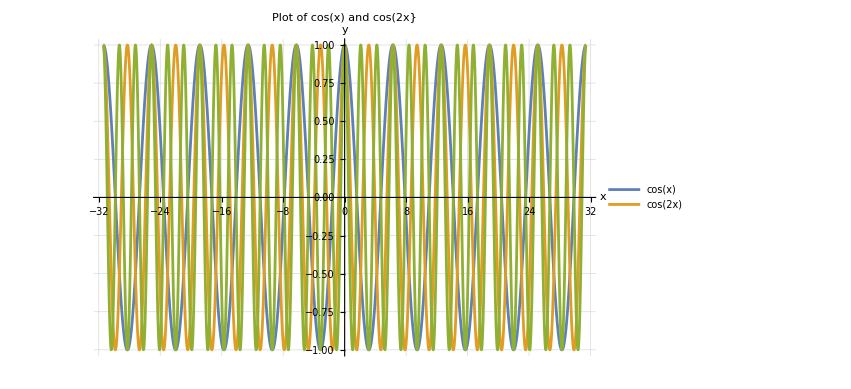

```mathematica
(*Define the range for x*)xRange={-10 Pi,10 Pi};

(*Plot cos(x) and cos(2x)*)
Plot[{Cos[x],Cos[2 x], Cos[3x]},{x,xRange[[1]],xRange[[2]]},PlotLegends->{"cos(x)","cos(2x)"},PlotStyle->Automatic,AxesLabel->{"x","y"},PlotLabel->"Plot of cos(x) and cos(2x}",GridLines->Automatic]
```

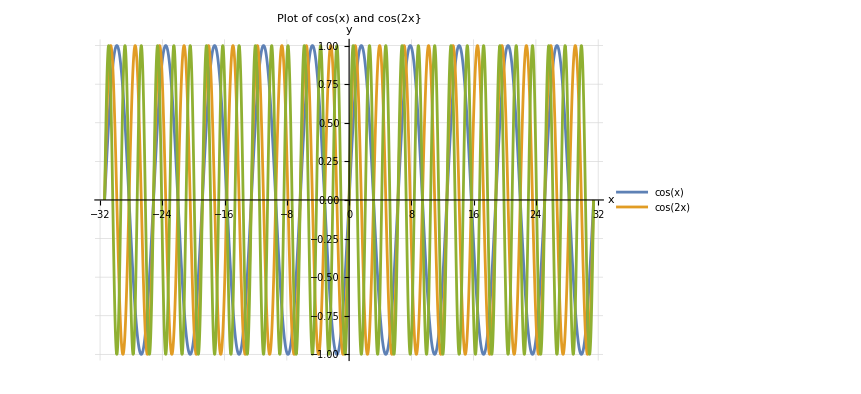

```mathematica
Plot[{Sin[x],Sin[2 x], Sin[3x]},{x,xRange[[1]],xRange[[2]]},PlotLegends->{"cos(x)","cos(2x)"},PlotStyle->Automatic,AxesLabel->{"x","y"},PlotLabel->"Plot of cos(x) and cos(2x}",GridLines->Automatic]
```

```mathematica
fnx=(a^2*Sin[x]+b^2*Sin[2x]+c^2*Sin[3x])/(a^2*Cos[x]+b^2*Cos[2x]+c^2*Cos[3x])
```

(a^2 sin(x)+b^2 sin(2 x)+c^2 sin(3 x))/(a^2 cos(x)+b^2 cos(2 x)+c^2 cos(3 x))

```mathematica
Clear[fnx]
```

```mathematica
fnx[1,1,1,1]
```

(sin(1)+sin(2)+sin(3))/(cos(1)+cos(2)+cos(3))

```mathematica
(*Define the function*)fnx[a_,b_,c_,x_]:=(a^2 Sin[x]+b^2 Sin[2 x]+c^2 Sin[3 x])/(a^2 Cos[x]+b^2 Cos[2 x]+c^2 Cos[3 x]);

(*Create the interactive plot with sliders for b and c*)
Manipulate[Plot[fnx[a,b,c,x],{x,-10,10},PlotRange->All,AxesLabel->{"x","f(x)"},PlotLabel->"Plot of f(x) with varying b and c"],{{b,1},0,5},(*Slider for b*){{c,1},0,5},{{a,1},0,5}  (*Slider for c*)]
```

```mathematica
(*Create the interactive plot with sliders for b and c*)
Manipulate[Plot[ArcTan[fnx[a,b,c,x]],{x,-10,10},PlotRange->{Automatic,{-5,5}},AxesLabel->{"x","f(x)"},PlotLabel->"Plot of f(x) with varying b and c"],{{b,1},0,5},(*Slider for b*){{c,1},0,5},{{a,1},0,5}  (*Slider for c*)]
```

```mathematica
(*Define three numbers*)num1=5;
num2=3;
num3=4;

(*Compute the LCM of the three numbers*)
lcmResult=LCM[num1,num2,num3];

(*Display the result*)
Print["LCM of ",num1,", ",num2,", and ",num3," is: ",lcmResult];
```

LCM of 5, 3, and 4 is: 60

### Dynamical Phase for SM case

#### For Vacuum Case

```mathematica
(*Neutrino mixing angles*)θ12=34.0 Degree;
θ23=40.0 Degree;
θ13=9.0 Degree;

(*Neutrino mixing matrix elements*)
U={{Cos[θ12] Cos[θ13],Sin[θ12] Cos[θ13],Sin[θ13]},{-Sin[θ12] Cos[θ23]-Cos[θ12] Sin[θ23] Sin[θ13],Cos[θ12] Cos[θ23]-Sin[θ12] Sin[θ23] Sin[θ13],Sin[θ23] Cos[θ13]},{Sin[θ12] Sin[θ23]-Cos[θ12] Cos[θ23] Sin[θ13],-Cos[θ12] Sin[θ23]-Sin[θ12] Cos[θ23] Sin[θ13],Cos[θ23] Cos[θ13]}};
```

```mathematica
U
```

(0.818831 | 0.552308 | 0.156434
-0.51173 | 0.57885 | 0.634874
0.260094 | -0.599906 | 0.756613)

```mathematica
nsm=3;  (*Define n,the number of elements in the ket vector*)
(*Generate the ket vector with n elements:{ket1,ket2,...,ketn}*)
ketsm=Table[Symbol["ketsm"<>ToString[i]],{i,1,nsm}];
(*Display the generated ket vector*)
ketsm
(*Define parameters E1,E2,and t*)
Ensm=Table[Symbol["Esm"<>ToString[i]],{i,1,nsm}];
 (*Energy values*)
tsm=tsm;        (*Time variable*)

(*Initialize the kett vector*)
kettsm=Table[0,{i,nsm}]; (*To hold the transformed elements*)
psism=Table[0,{i,nsm}]; (*To hold the transformed elements*)
psitsm=Table[0,{i,nsm}]; (*To hold the transformed elements*)
(*Use a loop to define the elements of kett*)
For[i=1,i<=Length[ketsm],i++,kettsm[[i]]=ketsm[[i]]*Exp[-I*Ensm[[i]]*tsm];];
(*Display the result*)
kettsm
(*Defining the mixed states at time t*)
For[i=1,i<=Length[ketsm],i++,{psism[[i]]=U[[i]].ketsm,psitsm[[i]]=U[[i]].kettsm};];
psism
psitsm
```

{ketsm1,ketsm2,ketsm3}

{ketsm1 ⅇ^(-ⅈ Esm1 tsm),ketsm2 ⅇ^(-ⅈ Esm2 tsm),ketsm3 ⅇ^(-ⅈ Esm3 tsm)}

{0.818831 ketsm1+0.552308 ketsm2+0.156434 ketsm3,-0.51173 ketsm1+0.57885 ketsm2+0.634874 ketsm3,0.260094 ketsm1-0.599906 ketsm2+0.756613 ketsm3}

{0.818831 ketsm1 ⅇ^(-ⅈ Esm1 tsm)+0.552308 ketsm2 ⅇ^(-ⅈ Esm2 tsm)+0.156434 ketsm3 ⅇ^(-ⅈ Esm3 tsm),-0.51173 ketsm1 ⅇ^(-ⅈ Esm1 tsm)+0.57885 ketsm2 ⅇ^(-ⅈ Esm2 tsm)+0.634874 ketsm3 ⅇ^(-ⅈ Esm3 tsm),0.260094 ketsm1 ⅇ^(-ⅈ Esm1 tsm)-0.599906 ketsm2 ⅇ^(-ⅈ Esm2 tsm)+0.756613 ketsm3 ⅇ^(-ⅈ Esm3 tsm)}

```mathematica
(*Differentiate psi1 with respect to time*)
dpsism=D[psitsm,tsm]
```

{(0.-0.818831 ⅈ) Esm1 ketsm1 ⅇ^(-ⅈ Esm1 tsm)-(0.+0.552308 ⅈ) Esm2 ketsm2 ⅇ^(-ⅈ Esm2 tsm)-(0.+0.156434 ⅈ) Esm3 ketsm3 ⅇ^(-ⅈ Esm3 tsm),(0.+0.51173 ⅈ) Esm1 ketsm1 ⅇ^(-ⅈ Esm1 tsm)-(0.+0.57885 ⅈ) Esm2 ketsm2 ⅇ^(-ⅈ Esm2 tsm)-(0.+0.634874 ⅈ) Esm3 ketsm3 ⅇ^(-ⅈ Esm3 tsm),(0.-0.260094 ⅈ) Esm1 ketsm1 ⅇ^(-ⅈ Esm1 tsm)+(0.+0.599906 ⅈ) Esm2 ketsm2 ⅇ^(-ⅈ Esm2 tsm)-(0.+0.756613 ⅈ) Esm3 ketsm3 ⅇ^(-ⅈ Esm3 tsm)}

```mathematica
(*Specify the number of dimensions*)numDimensions=nsm;

(*Create a list to store all kets*)
allKets={};

(*Loop to create each ket*)
For[i=1,i<=numDimensions,i++,(*Create a vector of zeros*)tempket=Table[0,{numDimensions}];
(*Set the i-th element to 1*)tempket[[i]]=1;
(*Add the ket to our list*)AppendTo[allKets,tempket];
(*Define a variable for this ket using ToExpression*)ToExpression["ketsm"<>ToString[i]<>" = "<>ToString[tempket]];]
```

```mathematica
(*Compute the inner product*)
innerProductsm=Conjugate[psitsm[[1]]].dpsism[[1]]
```

((0.+0. ⅈ)-(0.+0.818831 ⅈ) Esm1 ⅇ^(-ⅈ Esm1 tsm)) (0.+0.818831 ⅇ^(ⅈ Conjugate[(Esm1 tsm)]))+((0.+0. ⅈ)-(0.+0.552308 ⅈ) Esm2 ⅇ^(-ⅈ Esm2 tsm)) (0.+0.552308 ⅇ^(ⅈ Conjugate[(Esm2 tsm)]))+((0.+0. ⅈ)-(0.+0.156434 ⅈ) Esm3 ⅇ^(-ⅈ Esm3 tsm)) (0.+0.156434 ⅇ^(ⅈ Conjugate[(Esm3 tsm)]))

```mathematica
(*Specify the number of E variables*)numE=nsm;

(*Create the list of Element expressions*)
elementListsm=Join[Table[Element[Symbol["Esm"<>ToString[i]],Reals],{i,1,numE}],{Element[tsm,Reals]}];

(*Display the list*)
Print["Element list: ",elementListsm]
refinedExpressionsm=Refine[innerProductsm,elementListsm]//Expand
```

Element list: {Esm1∈ℝ,Esm2∈ℝ,Esm3∈ℝ,tsm∈ℝ}

(0.-0.670484 ⅈ) Esm1-(0.+0.305044 ⅈ) Esm2-(0.+0.0244717 ⅈ) Esm3+(0.+0. ⅈ)

```mathematica
realpartsm=Refine[(Conjugate[expr]+expr)/(2),elementListsm]
imaginarypartsm=Refine[(Conjugate[expr]-expr)/(2 I),elementListsm]//Expand
```

(Conjugate[expr]+expr)/2

(ⅈ expr)/2-(ⅈ Conjugate[expr])/2

```mathematica
Theta = ArcTan[imaginarypartsm/realpartsm]
```

tan^-1((2 ((ⅈ expr)/2-(ⅈ Conjugate[expr])/2))/(Conjugate[expr]+expr))

### Total Phase for SM case

```mathematica
innerProductsmtot=Table[i+j,{i,nsm},{j,nsm}];

(*Compute the all possible inner products for total phase*)
i=1;
While[i<nsm+1,{j=1;
While[j<nsm+1,{innerProductsmtot[[i,j]]=Conjugate[psitsm[[i]]].psism[[j]]//Expand};j++]};i++]
```

```mathematica
(*Specify the number of E variables*)numE=nsm;

(*Create the list of Element expressions*)
elementListsm=Join[Table[Element[Symbol["Esm"<>ToString[i]],Reals],{i,1,numE}],{Element[tsm,Reals]}];

(*Display the list*)
Print["Element list: ",elementListsm]
refinedExpressionsmtot=Refine[innerProductsmtot[[1,2]] (*Define inner product states*),elementListsm]//Expand
```

Element list: {Esm1∈ℝ,Esm2∈ℝ,Esm3∈ℝ,tsm∈ℝ}

0.-0.41902 ⅇ^(ⅈ Esm1 tsm)+0.319704 ⅇ^(ⅈ Esm2 tsm)+0.0993161 ⅇ^(ⅈ Esm3 tsm)

```mathematica
expr= ComplexExpand[refinedExpressionsmtot]
realpartsmtot=Refine[(Conjugate[expr]+expr)/(2),elementListsm] //Expand
imaginarypartsmtot=Refine[(Conjugate[expr]-expr)/(2 I),elementListsm]//Expand
```

ⅈ (-0.41902 sin(Esm1 tsm)+0.319704 sin(Esm2 tsm)+0.0993161 sin(Esm3 tsm))-0.41902 cos(Esm1 tsm)+0.319704 cos(Esm2 tsm)+0.0993161 cos(Esm3 tsm)+0.

-0.41902 cos(Esm1 tsm)+0.319704 cos(Esm2 tsm)+0.0993161 cos(Esm3 tsm)+0.

(0.41902+0. ⅈ) sin(Esm1 tsm)-(0.319704+0. ⅈ) sin(Esm2 tsm)-(0.0993161+0. ⅈ) sin(Esm3 tsm)+(0.+0. ⅈ)

```mathematica
ArcTan[imaginarypartsmtot/realpartsmtot]
Thetatot= ArcTan[imaginarypartsmtot/realpartsmtot]/.{Esm1->1,Esm2->1.5,Esm3->0.1,tsm->tsm}
```

tan^-1(((0.41902+0. ⅈ) sin(Esm1 tsm)-(0.319704+0. ⅈ) sin(Esm2 tsm)-(0.0993161+0. ⅈ) sin(Esm3 tsm)+(0.+0. ⅈ))/(-0.41902 cos(Esm1 tsm)+0.319704 cos(Esm2 tsm)+0.0993161 cos(Esm3 tsm)+0.))

tan^-1(((0.41902+0. ⅈ) sin(tsm)-(0.319704+0. ⅈ) sin(1.5 tsm)+(0.+0. ⅈ)+(-0.0993161+0. ⅈ) sin(0.1 tsm))/(0.0993161 cos(0.1 tsm)-0.41902 cos(tsm)+0.319704 cos(1.5 tsm)+0.))

```mathematica
fnx[tsm_]:=Evaluate[Thetatot]

(*Create the interactive plot with sliders for b*)Manipulate[Plot[fnx[x],{x,-10,10},PlotRange->{{-10,10},{-10,10}},AxesLabel->{"x","f(x)"},PlotLabel->"Plot of f(x) with varying b and c"],{{b,1},0,5}  (*Slider for b*)]
```

### Dynamical Phase for CW case

#### For Vacuum Case

```mathematica
(*Neutrino mixing angles*)θ12=34.0 Degree;
θ23=40.0 Degree;
θ13=9.0 Degree;

(*Neutrino mixing matrix elements*)
U={{Cos[θ12] Cos[θ13],Sin[θ12] Cos[θ13],Sin[θ13]},{-Sin[θ12] Cos[θ23]-Cos[θ12] Sin[θ23] Sin[θ13],Cos[θ12] Cos[θ23]-Sin[θ12] Sin[θ23] Sin[θ13],Sin[θ23] Cos[θ13]},{Sin[θ12] Sin[θ23]-Cos[θ12] Cos[θ23] Sin[θ13],-Cos[θ12] Sin[θ23]-Sin[θ12] Cos[θ23] Sin[θ13],Cos[θ23] Cos[θ13]}};
```

```mathematica
U
```

(0.818831 | 0.552308 | 0.156434
-0.51173 | 0.57885 | 0.634874
0.260094 | -0.599906 | 0.756613)

```mathematica
Ncw = 4;
(*Define two lists of size n*)Zero=Table[0,{i,Ncw+1}];  (*Example list 1*)
firstrow=Table[1,{i,Ncw+1}];  (*Example list 2*)

(*Combine the lists into a single vector of length 2n*)
firstcw=Join[firstrow,Zero,Zero];
secondcw=Join[Zero,firstrow,Zero];
thirdcw=Join[Zero,Zero,firstrow];
A = {firstcw,secondcw,thirdcw};
```

```mathematica
UCW = U.A
```

(0.818831 | 0.818831 | 0.818831 | 0.818831 | 0.818831 | 0.552308 | 0.552308 | 0.552308 | 0.552308 | 0.552308 | 0.156434 | 0.156434 | 0.156434 | 0.156434 | 0.156434
-0.51173 | -0.51173 | -0.51173 | -0.51173 | -0.51173 | 0.57885 | 0.57885 | 0.57885 | 0.57885 | 0.57885 | 0.634874 | 0.634874 | 0.634874 | 0.634874 | 0.634874
0.260094 | 0.260094 | 0.260094 | 0.260094 | 0.260094 | -0.599906 | -0.599906 | -0.599906 | -0.599906 | -0.599906 | 0.756613 | 0.756613 | 0.756613 | 0.756613 | 0.756613)

```mathematica
ncw=3*(Ncw+1);  (*Define n,the number of elements in the ket vector*)(*Initialize the kett vector*)
kettcw=Table[0,{i,ncw}]; (*To hold the transformed elements*)
psicw=Table[0,{i,3}]; (*To hold the transformed elements*)
psitcw=Table[0,{i,3}]; (*To hold the transformed elements*)
```

```mathematica
(*Generate the ket vector with n elements:{ket1,ket2,...,ketn}*)
ketcw=Table[Symbol["ketcw"<>ToString[i]],{i,1,ncw}];
(*Display the generated ket vector*)
ketcw
(*Define parameters E1,E2,and t*)
Encw=Table[Symbol["Ecw"<>ToString[i]],{i,1,ncw}];
 (*Energy values*)
tcw=tcw;        (*Time variable*)


(*Use a loop to define the elements of kett*)
For[i=1,i<=Length[ketcw],i++,kettcw[[i]]=ketcw[[i]]*Exp[-I*Encw[[i]]*tcw];];
(*Display the result*)
kettcw
(*Defining the mixed states at time t*)
For[i=1,i<=3,i++,{psicw[[i]]=UCW[[i]].ketcw,psitcw[[i]]=UCW[[i]].kettcw};];
psicw
psitcw
```

{ketcw1,ketcw2,ketcw3,ketcw4,ketcw5,ketcw6,ketcw7,ketcw8,ketcw9,ketcw10,ketcw11,ketcw12,ketcw13,ketcw14,ketcw15}

{ketcw1 ⅇ^(-ⅈ Ecw1 tcw),ketcw2 ⅇ^(-ⅈ Ecw2 tcw),ketcw3 ⅇ^(-ⅈ Ecw3 tcw),ketcw4 ⅇ^(-ⅈ Ecw4 tcw),ketcw5 ⅇ^(-ⅈ Ecw5 tcw),ketcw6 ⅇ^(-ⅈ Ecw6 tcw),ketcw7 ⅇ^(-ⅈ Ecw7 tcw),ketcw8 ⅇ^(-ⅈ Ecw8 tcw),ketcw9 ⅇ^(-ⅈ Ecw9 tcw),ketcw10 ⅇ^(-ⅈ Ecw10 tcw),ketcw11 ⅇ^(-ⅈ Ecw11 tcw),ketcw12 ⅇ^(-ⅈ Ecw12 tcw),ketcw13 ⅇ^(-ⅈ Ecw13 tcw),ketcw14 ⅇ^(-ⅈ Ecw14 tcw),ketcw15 ⅇ^(-ⅈ Ecw15 tcw)}

{0.818831 ketcw1+0.552308 ketcw10+0.156434 ketcw11+0.156434 ketcw12+0.156434 ketcw13+0.156434 ketcw14+0.156434 ketcw15+0.818831 ketcw2+0.818831 ketcw3+0.818831 ketcw4+0.818831 ketcw5+0.552308 ketcw6+0.552308 ketcw7+0.552308 ketcw8+0.552308 ketcw9,-0.51173 ketcw1+0.57885 ketcw10+0.634874 ketcw11+0.634874 ketcw12+0.634874 ketcw13+0.634874 ketcw14+0.634874 ketcw15-0.51173 ketcw2-0.51173 ketcw3-0.51173 ketcw4-0.51173 ketcw5+0.57885 ketcw6+0.57885 ketcw7+0.57885 ketcw8+0.57885 ketcw9,0.260094 ketcw1-0.599906 ketcw10+0.756613 ketcw11+0.756613 ketcw12+0.756613 ketcw13+0.756613 ketcw14+0.756613 ketcw15+0.260094 ketcw2+0.260094 ketcw3+0.260094 ketcw4+0.260094 ketcw5-0.599906 ketcw6-0.599906 ketcw7-0.599906 ketcw8-0.599906 ketcw9}

{0.818831 ketcw1 ⅇ^(-ⅈ Ecw1 tcw)+0.552308 ketcw10 ⅇ^(-ⅈ Ecw10 tcw)+0.156434 ketcw11 ⅇ^(-ⅈ Ecw11 tcw)+0.156434 ketcw12 ⅇ^(-ⅈ Ecw12 tcw)+0.156434 ketcw13 ⅇ^(-ⅈ Ecw13 tcw)+0.156434 ketcw14 ⅇ^(-ⅈ Ecw14 tcw)+0.156434 ketcw15 ⅇ^(-ⅈ Ecw15 tcw)+0.818831 ketcw2 ⅇ^(-ⅈ Ecw2 tcw)+0.818831 ketcw3 ⅇ^(-ⅈ Ecw3 tcw)+0.818831 ketcw4 ⅇ^(-ⅈ Ecw4 tcw)+0.818831 ketcw5 ⅇ^(-ⅈ Ecw5 tcw)+0.552308 ketcw6 ⅇ^(-ⅈ Ecw6 tcw)+0.552308 ketcw7 ⅇ^(-ⅈ Ecw7 tcw)+0.552308 ketcw8 ⅇ^(-ⅈ Ecw8 tcw)+0.552308 ketcw9 ⅇ^(-ⅈ Ecw9 tcw),-0.51173 ketcw1 ⅇ^(-ⅈ Ecw1 tcw)+0.57885 ketcw10 ⅇ^(-ⅈ Ecw10 tcw)+0.634874 ketcw11 ⅇ^(-ⅈ Ecw11 tcw)+0.634874 ketcw12 ⅇ^(-ⅈ Ecw12 tcw)+0.634874 ketcw13 ⅇ^(-ⅈ Ecw13 tcw)+0.634874 ketcw14 ⅇ^(-ⅈ Ecw14 tcw)+0.634874 ketcw15 ⅇ^(-ⅈ Ecw15 tcw)-0.51173 ketcw2 ⅇ^(-ⅈ Ecw2 tcw)-0.51173 ketcw3 ⅇ^(-ⅈ Ecw3 tcw)-0.51173 ketcw4 ⅇ^(-ⅈ Ecw4 tcw)-0.51173 ketcw5 ⅇ^(-ⅈ Ecw5 tcw)+0.57885 ketcw6 ⅇ^(-ⅈ Ecw6 tcw)+0.57885 ketcw7 ⅇ^(-ⅈ Ecw7 tcw)+0.57885 ketcw8 ⅇ^(-ⅈ Ecw8 tcw)+0.57885 ketcw9 ⅇ^(-ⅈ Ecw9 tcw),0.260094 ketcw1 ⅇ^(-ⅈ Ecw1 tcw)-0.599906 ketcw10 ⅇ^(-ⅈ Ecw10 tcw)+0.756613 ketcw11 ⅇ^(-ⅈ Ecw11 tcw)+0.756613 ketcw12 ⅇ^(-ⅈ Ecw12 tcw)+0.756613 ketcw13 ⅇ^(-ⅈ Ecw13 tcw)+0.756613 ketcw14 ⅇ^(-ⅈ Ecw14 tcw)+0.756613 ketcw15 ⅇ^(-ⅈ Ecw15 tcw)+0.260094 ketcw2 ⅇ^(-ⅈ Ecw2 tcw)+0.260094 ketcw3 ⅇ^(-ⅈ Ecw3 tcw)+0.260094 ketcw4 ⅇ^(-ⅈ Ecw4 tcw)+0.260094 ketcw5 ⅇ^(-ⅈ Ecw5 tcw)-0.599906 ketcw6 ⅇ^(-ⅈ Ecw6 tcw)-0.599906 ketcw7 ⅇ^(-ⅈ Ecw7 tcw)-0.599906 ketcw8 ⅇ^(-ⅈ Ecw8 tcw)-0.599906 ketcw9 ⅇ^(-ⅈ Ecw9 tcw)}

```mathematica
(*Differentiate psi1 with respect to time*)
dpsicw=D[psitcw,tcw]
```

{(0.-0.818831 ⅈ) Ecw1 ketcw1 ⅇ^(-ⅈ Ecw1 tcw)-(0.+0.552308 ⅈ) Ecw10 ketcw10 ⅇ^(-ⅈ Ecw10 tcw)-(0.+0.156434 ⅈ) Ecw11 ketcw11 ⅇ^(-ⅈ Ecw11 tcw)-(0.+0.156434 ⅈ) Ecw12 ketcw12 ⅇ^(-ⅈ Ecw12 tcw)-(0.+0.156434 ⅈ) Ecw13 ketcw13 ⅇ^(-ⅈ Ecw13 tcw)-(0.+0.156434 ⅈ) Ecw14 ketcw14 ⅇ^(-ⅈ Ecw14 tcw)-(0.+0.156434 ⅈ) Ecw15 ketcw15 ⅇ^(-ⅈ Ecw15 tcw)-(0.+0.818831 ⅈ) Ecw2 ketcw2 ⅇ^(-ⅈ Ecw2 tcw)-(0.+0.818831 ⅈ) Ecw3 ketcw3 ⅇ^(-ⅈ Ecw3 tcw)-(0.+0.818831 ⅈ) Ecw4 ketcw4 ⅇ^(-ⅈ Ecw4 tcw)-(0.+0.818831 ⅈ) Ecw5 ketcw5 ⅇ^(-ⅈ Ecw5 tcw)-(0.+0.552308 ⅈ) Ecw6 ketcw6 ⅇ^(-ⅈ Ecw6 tcw)-(0.+0.552308 ⅈ) Ecw7 ketcw7 ⅇ^(-ⅈ Ecw7 tcw)-(0.+0.552308 ⅈ) Ecw8 ketcw8 ⅇ^(-ⅈ Ecw8 tcw)-(0.+0.552308 ⅈ) Ecw9 ketcw9 ⅇ^(-ⅈ Ecw9 tcw),(0.+0.51173 ⅈ) Ecw1 ketcw1 ⅇ^(-ⅈ Ecw1 tcw)-(0.+0.57885 ⅈ) Ecw10 ketcw10 ⅇ^(-ⅈ Ecw10 tcw)-(0.+0.634874 ⅈ) Ecw11 ketcw11 ⅇ^(-ⅈ Ecw11 tcw)-(0.+0.634874 ⅈ) Ecw12 ketcw12 ⅇ^(-ⅈ Ecw12 tcw)-(0.+0.634874 ⅈ) Ecw13 ketcw13 ⅇ^(-ⅈ Ecw13 tcw)-(0.+0.634874 ⅈ) Ecw14 ketcw14 ⅇ^(-ⅈ Ecw14 tcw)-(0.+0.634874 ⅈ) Ecw15 ketcw15 ⅇ^(-ⅈ Ecw15 tcw)+(0.+0.51173 ⅈ) Ecw2 ketcw2 ⅇ^(-ⅈ Ecw2 tcw)+(0.+0.51173 ⅈ) Ecw3 ketcw3 ⅇ^(-ⅈ Ecw3 tcw)+(0.+0.51173 ⅈ) Ecw4 ketcw4 ⅇ^(-ⅈ Ecw4 tcw)+(0.+0.51173 ⅈ) Ecw5 ketcw5 ⅇ^(-ⅈ Ecw5 tcw)-(0.+0.57885 ⅈ) Ecw6 ketcw6 ⅇ^(-ⅈ Ecw6 tcw)-(0.+0.57885 ⅈ) Ecw7 ketcw7 ⅇ^(-ⅈ Ecw7 tcw)-(0.+0.57885 ⅈ) Ecw8 ketcw8 ⅇ^(-ⅈ Ecw8 tcw)-(0.+0.57885 ⅈ) Ecw9 ketcw9 ⅇ^(-ⅈ Ecw9 tcw),(0.-0.260094 ⅈ) Ecw1 ketcw1 ⅇ^(-ⅈ Ecw1 tcw)+(0.+0.599906 ⅈ) Ecw10 ketcw10 ⅇ^(-ⅈ Ecw10 tcw)-(0.+0.756613 ⅈ) Ecw11 ketcw11 ⅇ^(-ⅈ Ecw11 tcw)-(0.+0.756613 ⅈ) Ecw12 ketcw12 ⅇ^(-ⅈ Ecw12 tcw)-(0.+0.756613 ⅈ) Ecw13 ketcw13 ⅇ^(-ⅈ Ecw13 tcw)-(0.+0.756613 ⅈ) Ecw14 ketcw14 ⅇ^(-ⅈ Ecw14 tcw)-(0.+0.756613 ⅈ) Ecw15 ketcw15 ⅇ^(-ⅈ Ecw15 tcw)-(0.+0.260094 ⅈ) Ecw2 ketcw2 ⅇ^(-ⅈ Ecw2 tcw)-(0.+0.260094 ⅈ) Ecw3 ketcw3 ⅇ^(-ⅈ Ecw3 tcw)-(0.+0.260094 ⅈ) Ecw4 ketcw4 ⅇ^(-ⅈ Ecw4 tcw)-(0.+0.260094 ⅈ) Ecw5 ketcw5 ⅇ^(-ⅈ Ecw5 tcw)+(0.+0.599906 ⅈ) Ecw6 ketcw6 ⅇ^(-ⅈ Ecw6 tcw)+(0.+0.599906 ⅈ) Ecw7 ketcw7 ⅇ^(-ⅈ Ecw7 tcw)+(0.+0.599906 ⅈ) Ecw8 ketcw8 ⅇ^(-ⅈ Ecw8 tcw)+(0.+0.599906 ⅈ) Ecw9 ketcw9 ⅇ^(-ⅈ Ecw9 tcw)}

```mathematica
(*Specify the number of dimensions*)numDimensions=ncw;

(*Create a list to store all kets*)
allKets={};

(*Loop to create each ket*)
For[i=1,i<=numDimensions,i++,(*Create a vector of zeros*)tempket=Table[0,{numDimensions}];
(*Set the i-th element to 1*)tempket[[i]]=1;
(*Add the ket to our list*)AppendTo[allKets,tempket];
(*Define a variable for this ket using ToExpression*)ToExpression["ketcw"<>ToString[i]<>" = "<>ToString[tempket]];]
```

```mathematica
(*Compute the inner product*)
innerProductcw=Conjugate[psitcw[[1]]].dpsicw[[1]]
```

((0.+0. ⅈ)-(0.+0.818831 ⅈ) Ecw1 ⅇ^(-ⅈ Ecw1 tcw)) (0.+0.818831 ⅇ^(ⅈ Conjugate[(Ecw1 tcw)]))+((0.+0. ⅈ)-(0.+0.552308 ⅈ) Ecw10 ⅇ^(-ⅈ Ecw10 tcw)) (0.+0.552308 ⅇ^(ⅈ Conjugate[(Ecw10 tcw)]))+((0.+0. ⅈ)-(0.+0.156434 ⅈ) Ecw11 ⅇ^(-ⅈ Ecw11 tcw)) (0.+0.156434 ⅇ^(ⅈ Conjugate[(Ecw11 tcw)]))+((0.+0. ⅈ)-(0.+0.156434 ⅈ) Ecw12 ⅇ^(-ⅈ Ecw12 tcw)) (0.+0.156434 ⅇ^(ⅈ Conjugate[(Ecw12 tcw)]))+((0.+0. ⅈ)-(0.+0.156434 ⅈ) Ecw13 ⅇ^(-ⅈ Ecw13 tcw)) (0.+0.156434 ⅇ^(ⅈ Conjugate[(Ecw13 tcw)]))+((0.+0. ⅈ)-(0.+0.156434 ⅈ) Ecw14 ⅇ^(-ⅈ Ecw14 tcw)) (0.+0.156434 ⅇ^(ⅈ Conjugate[(Ecw14 tcw)]))+((0.+0. ⅈ)-(0.+0.156434 ⅈ) Ecw15 ⅇ^(-ⅈ Ecw15 tcw)) (0.+0.156434 ⅇ^(ⅈ Conjugate[(Ecw15 tcw)]))+((0.+0. ⅈ)-(0.+0.818831 ⅈ) Ecw2 ⅇ^(-ⅈ Ecw2 tcw)) (0.+0.818831 ⅇ^(ⅈ Conjugate[(Ecw2 tcw)]))+((0.+0. ⅈ)-(0.+0.818831 ⅈ) Ecw3 ⅇ^(-ⅈ Ecw3 tcw)) (0.+0.818831 ⅇ^(ⅈ Conjugate[(Ecw3 tcw)]))+((0.+0. ⅈ)-(0.+0.818831 ⅈ) Ecw4 ⅇ^(-ⅈ Ecw4 tcw)) (0.+0.818831 ⅇ^(ⅈ Conjugate[(Ecw4 tcw)]))+((0.+0. ⅈ)-(0.+0.818831 ⅈ) Ecw5 ⅇ^(-ⅈ Ecw5 tcw)) (0.+0.818831 ⅇ^(ⅈ Conjugate[(Ecw5 tcw)]))+((0.+0. ⅈ)-(0.+0.552308 ⅈ) Ecw6 ⅇ^(-ⅈ Ecw6 tcw)) (0.+0.552308 ⅇ^(ⅈ Conjugate[(Ecw6 tcw)]))+((0.+0. ⅈ)-(0.+0.552308 ⅈ) Ecw7 ⅇ^(-ⅈ Ecw7 tcw)) (0.+0.552308 ⅇ^(ⅈ Conjugate[(Ecw7 tcw)]))+((0.+0. ⅈ)-(0.+0.552308 ⅈ) Ecw8 ⅇ^(-ⅈ Ecw8 tcw)) (0.+0.552308 ⅇ^(ⅈ Conjugate[(Ecw8 tcw)]))+((0.+0. ⅈ)-(0.+0.552308 ⅈ) Ecw9 ⅇ^(-ⅈ Ecw9 tcw)) (0.+0.552308 ⅇ^(ⅈ Conjugate[(Ecw9 tcw)]))

```mathematica
(*Specify the number of E variables*)numE=ncw;

(*Create the list of Element expressions*)
elementListcw=Join[Table[Element[Symbol["Ecw"<>ToString[i]],Reals],{i,1,numE}],{Element[tcw,Reals]}];

(*Display the list*)
Print["Element list: ",elementListcw]
refinedExpressioncw=Refine[innerProductcw,elementListcw]//Expand
```

Element list: {Ecw1∈ℝ,Ecw2∈ℝ,Ecw3∈ℝ,Ecw4∈ℝ,Ecw5∈ℝ,Ecw6∈ℝ,Ecw7∈ℝ,Ecw8∈ℝ,Ecw9∈ℝ,Ecw10∈ℝ,Ecw11∈ℝ,Ecw12∈ℝ,Ecw13∈ℝ,Ecw14∈ℝ,Ecw15∈ℝ,tcw∈ℝ}

(0.-0.670484 ⅈ) Ecw1-(0.+0.305044 ⅈ) Ecw10-(0.+0.0244717 ⅈ) Ecw11-(0.+0.0244717 ⅈ) Ecw12-(0.+0.0244717 ⅈ) Ecw13-(0.+0.0244717 ⅈ) Ecw14-(0.+0.0244717 ⅈ) Ecw15-(0.+0.670484 ⅈ) Ecw2-(0.+0.670484 ⅈ) Ecw3-(0.+0.670484 ⅈ) Ecw4-(0.+0.670484 ⅈ) Ecw5-(0.+0.305044 ⅈ) Ecw6-(0.+0.305044 ⅈ) Ecw7-(0.+0.305044 ⅈ) Ecw8-(0.+0.305044 ⅈ) Ecw9+(0.+0. ⅈ)

```mathematica
expr = refinedExpressioncw
```

(0.-0.670484 ⅈ) Ecw1-(0.+0.305044 ⅈ) Ecw10-(0.+0.0244717 ⅈ) Ecw11-(0.+0.0244717 ⅈ) Ecw12-(0.+0.0244717 ⅈ) Ecw13-(0.+0.0244717 ⅈ) Ecw14-(0.+0.0244717 ⅈ) Ecw15-(0.+0.670484 ⅈ) Ecw2-(0.+0.670484 ⅈ) Ecw3-(0.+0.670484 ⅈ) Ecw4-(0.+0.670484 ⅈ) Ecw5-(0.+0.305044 ⅈ) Ecw6-(0.+0.305044 ⅈ) Ecw7-(0.+0.305044 ⅈ) Ecw8-(0.+0.305044 ⅈ) Ecw9+(0.+0. ⅈ)

```mathematica
realpartcw=Refine[(Conjugate[expr]+expr)/(2),elementListcw]
imaginarypartcw=Refine[(Conjugate[expr]-expr)/(2 I),elementListcw]//Expand
```

0.+0. ⅈ

(0.670484+0. ⅈ) Ecw1+(0.305044+0. ⅈ) Ecw10+(0.0244717+0. ⅈ) Ecw11+(0.0244717+0. ⅈ) Ecw12+(0.0244717+0. ⅈ) Ecw13+(0.0244717+0. ⅈ) Ecw14+(0.0244717+0. ⅈ) Ecw15+(0.670484+0. ⅈ) Ecw2+(0.670484+0. ⅈ) Ecw3+(0.670484+0. ⅈ) Ecw4+(0.670484+0. ⅈ) Ecw5+(0.305044+0. ⅈ) Ecw6+(0.305044+0. ⅈ) Ecw7+(0.305044+0. ⅈ) Ecw8+(0.305044+0. ⅈ) Ecw9+(0.+0. ⅈ)

### Total Phase for CW case

```mathematica
innerProductcwtot=Table[i+j,{i,3},{j,3}];

(*Compute the all possible inner products for total phase*)
i=1;
While[i<3+1,{j=1;
While[j<3+1,{innerProductcwtot[[i,j]]=Conjugate[psitcw[[i]]].psicw[[j]]//Expand};j++]};i++]
```

```mathematica
(*Specify the number of E variables*)numE=ncw;

(*Create the list of Element expressions*)
elementListcw=Join[Table[Element[Symbol["Ecw"<>ToString[i]],Reals],{i,1,numE}],{Element[tcw,Reals]}];

(*Display the list*)
Print["Element list: ",elementListcw]
refinedExpressioncwtot=Refine[innerProductcwtot[[1,2]] (*Define inner product states*),elementListcw]//Expand
```

Element list: {Ecw1∈ℝ,Ecw2∈ℝ,Ecw3∈ℝ,Ecw4∈ℝ,Ecw5∈ℝ,Ecw6∈ℝ,Ecw7∈ℝ,Ecw8∈ℝ,Ecw9∈ℝ,Ecw10∈ℝ,Ecw11∈ℝ,Ecw12∈ℝ,Ecw13∈ℝ,Ecw14∈ℝ,Ecw15∈ℝ,tcw∈ℝ}

0.-0.41902 ⅇ^(ⅈ Ecw1 tcw)+0.319704 ⅇ^(ⅈ Ecw10 tcw)+0.0993161 ⅇ^(ⅈ Ecw11 tcw)+0.0993161 ⅇ^(ⅈ Ecw12 tcw)+0.0993161 ⅇ^(ⅈ Ecw13 tcw)+0.0993161 ⅇ^(ⅈ Ecw14 tcw)+0.0993161 ⅇ^(ⅈ Ecw15 tcw)-0.41902 ⅇ^(ⅈ Ecw2 tcw)-0.41902 ⅇ^(ⅈ Ecw3 tcw)-0.41902 ⅇ^(ⅈ Ecw4 tcw)-0.41902 ⅇ^(ⅈ Ecw5 tcw)+0.319704 ⅇ^(ⅈ Ecw6 tcw)+0.319704 ⅇ^(ⅈ Ecw7 tcw)+0.319704 ⅇ^(ⅈ Ecw8 tcw)+0.319704 ⅇ^(ⅈ Ecw9 tcw)

```mathematica
expr= ComplexExpand[refinedExpressioncwtot]
realpartcwtot=Refine[(Conjugate[expr]+expr)/(2),elementListcw] //Expand
imaginarypartcwtot=Refine[(Conjugate[expr]-expr)/(2 I),elementListcw]//Expand
```

ⅈ (-0.41902 sin(Ecw1 tcw)+0.319704 sin(Ecw10 tcw)+0.0993161 sin(Ecw11 tcw)+0.0993161 sin(Ecw12 tcw)+0.0993161 sin(Ecw13 tcw)+0.0993161 sin(Ecw14 tcw)+0.0993161 sin(Ecw15 tcw)-0.41902 sin(Ecw2 tcw)-0.41902 sin(Ecw3 tcw)-0.41902 sin(Ecw4 tcw)-0.41902 sin(Ecw5 tcw)+0.319704 sin(Ecw6 tcw)+0.319704 sin(Ecw7 tcw)+0.319704 sin(Ecw8 tcw)+0.319704 sin(Ecw9 tcw))-0.41902 cos(Ecw1 tcw)+0.319704 cos(Ecw10 tcw)+0.0993161 cos(Ecw11 tcw)+0.0993161 cos(Ecw12 tcw)+0.0993161 cos(Ecw13 tcw)+0.0993161 cos(Ecw14 tcw)+0.0993161 cos(Ecw15 tcw)-0.41902 cos(Ecw2 tcw)-0.41902 cos(Ecw3 tcw)-0.41902 cos(Ecw4 tcw)-0.41902 cos(Ecw5 tcw)+0.319704 cos(Ecw6 tcw)+0.319704 cos(Ecw7 tcw)+0.319704 cos(Ecw8 tcw)+0.319704 cos(Ecw9 tcw)+0.

-0.41902 cos(Ecw1 tcw)+0.319704 cos(Ecw10 tcw)+0.0993161 cos(Ecw11 tcw)+0.0993161 cos(Ecw12 tcw)+0.0993161 cos(Ecw13 tcw)+0.0993161 cos(Ecw14 tcw)+0.0993161 cos(Ecw15 tcw)-0.41902 cos(Ecw2 tcw)-0.41902 cos(Ecw3 tcw)-0.41902 cos(Ecw4 tcw)-0.41902 cos(Ecw5 tcw)+0.319704 cos(Ecw6 tcw)+0.319704 cos(Ecw7 tcw)+0.319704 cos(Ecw8 tcw)+0.319704 cos(Ecw9 tcw)+0.

(0.41902+0. ⅈ) sin(Ecw1 tcw)-(0.319704+0. ⅈ) sin(Ecw10 tcw)-(0.0993161+0. ⅈ) sin(Ecw11 tcw)-(0.0993161+0. ⅈ) sin(Ecw12 tcw)-(0.0993161+0. ⅈ) sin(Ecw13 tcw)-(0.0993161+0. ⅈ) sin(Ecw14 tcw)-(0.0993161+0. ⅈ) sin(Ecw15 tcw)+(0.41902+0. ⅈ) sin(Ecw2 tcw)+(0.41902+0. ⅈ) sin(Ecw3 tcw)+(0.41902+0. ⅈ) sin(Ecw4 tcw)+(0.41902+0. ⅈ) sin(Ecw5 tcw)-(0.319704+0. ⅈ) sin(Ecw6 tcw)-(0.319704+0. ⅈ) sin(Ecw7 tcw)-(0.319704+0. ⅈ) sin(Ecw8 tcw)-(0.319704+0. ⅈ) sin(Ecw9 tcw)+(0.+0. ⅈ)

```mathematica
ArcTan[imaginarypartcwtot/realpartcwtot]
Thetatot= ArcTan[imaginarypartcwtot/realpartcwtot]/.{Esm1->1,Esm2->1.5,Esm3->0.1,tsm->tsm}
```

tan^-1(((0.41902+0. ⅈ) sin(Ecw1 tcw)-(0.319704+0. ⅈ) sin(Ecw10 tcw)-(0.0993161+0. ⅈ) sin(Ecw11 tcw)-(0.0993161+0. ⅈ) sin(Ecw12 tcw)-(0.0993161+0. ⅈ) sin(Ecw13 tcw)-(0.0993161+0. ⅈ) sin(Ecw14 tcw)-(0.0993161+0. ⅈ) sin(Ecw15 tcw)+(0.41902+0. ⅈ) sin(Ecw2 tcw)+(0.41902+0. ⅈ) sin(Ecw3 tcw)+(0.41902+0. ⅈ) sin(Ecw4 tcw)+(0.41902+0. ⅈ) sin(Ecw5 tcw)-(0.319704+0. ⅈ) sin(Ecw6 tcw)-(0.319704+0. ⅈ) sin(Ecw7 tcw)-(0.319704+0. ⅈ) sin(Ecw8 tcw)-(0.319704+0. ⅈ) sin(Ecw9 tcw)+(0.+0. ⅈ))/(-0.41902 cos(Ecw1 tcw)+0.319704 cos(Ecw10 tcw)+0.0993161 cos(Ecw11 tcw)+0.0993161 cos(Ecw12 tcw)+0.0993161 cos(Ecw13 tcw)+0.0993161 cos(Ecw14 tcw)+0.0993161 cos(Ecw15 tcw)-0.41902 cos(Ecw2 tcw)-0.41902 cos(Ecw3 tcw)-0.41902 cos(Ecw4 tcw)-0.41902 cos(Ecw5 tcw)+0.319704 cos(Ecw6 tcw)+0.319704 cos(Ecw7 tcw)+0.319704 cos(Ecw8 tcw)+0.319704 cos(Ecw9 tcw)+0.))

tan^-1(((0.41902+0. ⅈ) sin(Ecw1 tcw)-(0.319704+0. ⅈ) sin(Ecw10 tcw)-(0.0993161+0. ⅈ) sin(Ecw11 tcw)-(0.0993161+0. ⅈ) sin(Ecw12 tcw)-(0.0993161+0. ⅈ) sin(Ecw13 tcw)-(0.0993161+0. ⅈ) sin(Ecw14 tcw)-(0.0993161+0. ⅈ) sin(Ecw15 tcw)+(0.41902+0. ⅈ) sin(Ecw2 tcw)+(0.41902+0. ⅈ) sin(Ecw3 tcw)+(0.41902+0. ⅈ) sin(Ecw4 tcw)+(0.41902+0. ⅈ) sin(Ecw5 tcw)-(0.319704+0. ⅈ) sin(Ecw6 tcw)-(0.319704+0. ⅈ) sin(Ecw7 tcw)-(0.319704+0. ⅈ) sin(Ecw8 tcw)-(0.319704+0. ⅈ) sin(Ecw9 tcw)+(0.+0. ⅈ))/(-0.41902 cos(Ecw1 tcw)+0.319704 cos(Ecw10 tcw)+0.0993161 cos(Ecw11 tcw)+0.0993161 cos(Ecw12 tcw)+0.0993161 cos(Ecw13 tcw)+0.0993161 cos(Ecw14 tcw)+0.0993161 cos(Ecw15 tcw)-0.41902 cos(Ecw2 tcw)-0.41902 cos(Ecw3 tcw)-0.41902 cos(Ecw4 tcw)-0.41902 cos(Ecw5 tcw)+0.319704 cos(Ecw6 tcw)+0.319704 cos(Ecw7 tcw)+0.319704 cos(Ecw8 tcw)+0.319704 cos(Ecw9 tcw)+0.))

```mathematica
fnx[tsm_]:=Evaluate[Thetatot]

(*Create the interactive plot with sliders for b*)Manipulate[Plot[fnx[x],{x,-10,10},PlotRange->{{-10,10},{-10,10}},AxesLabel->{"x","f(x)"},PlotLabel->"Plot of f(x) with varying b and c"],{{b,1},0,5}  (*Slider for b*)]
```

```mathematica
uma = {{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}} /.{theta->th}
```

(cos(th) | -sin(th)
sin(th) | cos(th))

### Total Phase for 2 case

#### total phase trial

```mathematica
theta2 = ArcTan[(uma[[1,1]]^2 * Sin[x]+uma[[1,2]]^2 * Sin[2*x])/(uma[[1,1]]^2 * Cos[x]+uma[[1,2]]^2 * Cos[2*x])]
```

tan^-1((sin^2(th) sin(2 x)+cos^2(th) sin(x))/(cos^2(th) cos(x)+sin^2(th) cos(2 x)))

```mathematica
theta2cw = ArcTan[(uma[[1,1]]^2 * Sin[x]+uma[[1,2]]^2 * Sin[2x]+uma[[1,1]]^2 * Sin[010*x]/1+uma[[1,2]]^2 * Sin[05*x]/1)/(uma[[1,1]]^2 * Cos[x]+uma[[1,2]]^2 * Cos[2x]+uma[[1,1]]^2 * Cos[010*x]/1+uma[[1,2]]^2 * Cos[05*x]/1)]
```

tan^-1((sin^2(th) sin(2 x)+sin^2(th) sin(5 x)+cos^2(th) sin(x)+cos^2(th) sin(10 x))/(cos^2(th) cos(x)+cos^2(th) cos(10 x)+sin^2(th) cos(2 x)+sin^2(th) cos(5 x)))

```mathematica
ftx[th_,x_]:= Evaluate[theta2]
ftxcw[th_,x_]:= Evaluate[theta2cw]
```

```mathematica
Manipulate[Plot[{ftx[b,x] *(180/Pi),ftxcw[x,b] *(180/Pi)},{x,-05,05},PlotRange->{{-05,05},{-100,100}},AxesLabel->{"x","f(x)"},PlotLabel->"Plot of f(x) with varying b and c"],{{b,1},0,5}  (*Slider for b*)]
```

```mathematica
Plot3D[ftxcw[x,y],{x,-5,5},{y,-5,5},ColorFunction->"Rainbow",(*Color scheme*)Mesh->None,(*No mesh lines*)PlotRange->All,(*Include all values in plot range*)AxesLabel->{"x","y","f(x,y)"},(*Label axes*)PlotLabel->"Plot of f(x, y) = Sin(Sqrt[x^2 + y^2])",(*Title*)Lighting->"Neutral"      (*Neutral lighting for better visibility*)]
```

-Graphics3D-

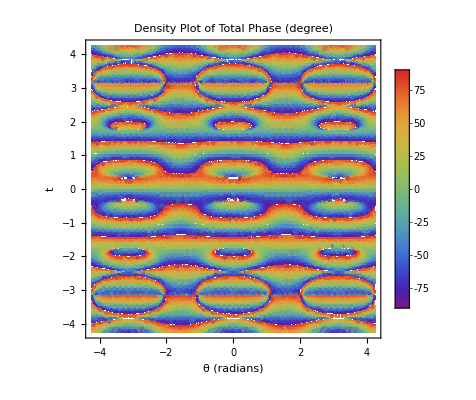

```mathematica
DensityPlot[SetPrecision[ftxcw[x,y]*(180/Pi),50],{x,-4.25,4.25},{y,-4.25,4.25},ColorFunction->"Rainbow",PlotPoints->50,Frame->True,FrameLabel->{Style["θ (radians)",Black,16],Style["t",Black,16]},PlotLabel->Style["Density Plot of Total Phase (degree)",Black,Bold,12],Mesh->False,ColorFunctionScaling->True,PlotLegends->Automatic,FrameStyle->Directive[Black],(*Makes frame darker*)FrameTicksStyle->Directive[Black,8],(*Makes frame ticks darker*)BaseStyle->{FontSize->8}  (*Overall style*)]
```

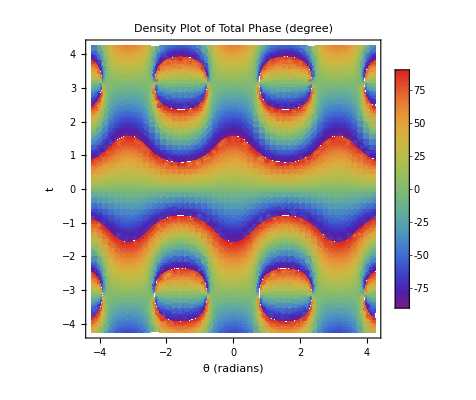

```mathematica
DensityPlot[SetPrecision[ftx[x,y]*(180/Pi),50],{x,-4.25,4.25},{y,-4.25,4.25},ColorFunction->"Rainbow",PlotPoints->50,Frame->True,FrameLabel->{Style["θ (radians)",Black,16],Style["t",Black,16]},PlotLabel->Style["Density Plot of Total Phase (degree)",Black,Bold,12],Mesh->False,ColorFunctionScaling->True,PlotLegends->Automatic,FrameStyle->Directive[Black],(*Makes frame darker*)FrameTicksStyle->Directive[Black,8],(*Makes frame ticks darker*)BaseStyle->{FontSize->8}  (*Overall style*)]
```

#### dynamical phase trial

```mathematica
phi = ArcTan[Sin[(uma[[1,1]]^2 * x+uma[[1,2]]^2 2*x)]/Cos[(uma[[1,1]]^2 * x+uma[[1,2]]^2 2*x)]]
```

tan^-1(tan(2 x sin^2(th)+x cos^2(th)))

```mathematica
norm =Normalize[{uma[[1,1]],uma[[1,2]],uma[[1,1]],uma[[1,2]]}]
```

{(cos(th))/(√(2 Abs[sin(th)]^2+2 Abs[cos(th)]^2)),-(sin(th))/(√(2 Abs[sin(th)]^2+2 Abs[cos(th)]^2)),(cos(th))/(√(2 Abs[sin(th)]^2+2 Abs[cos(th)]^2)),-(sin(th))/(√(2 Abs[sin(th)]^2+2 Abs[cos(th)]^2))}

```mathematica
norm[[1]]^2 * x+norm[[2]]^2 2*x+norm[[3]]^2 50* x+norm[[4]]^2 300*x
```

(51 x cos^2(th))/(2 Abs[sin(th)]^2+2 Abs[cos(th)]^2)+(302 x sin^2(th))/(2 Abs[sin(th)]^2+2 Abs[cos(th)]^2)

```mathematica
phicw =ArcTan[Sin[(norm[[1]]^2 * x+norm[[2]]^2 2*x+norm[[3]]^2 5* x+norm[[4]]^2 10*x)]/Cos[(norm[[1]]^2 * x+norm[[2]]^2 2*x+norm[[3]]^2 5* x+norm[[4]]^2 10*x)]]
```

tan^-1(tan((6 x cos^2(th))/(2 Abs[sin(th)]^2+2 Abs[cos(th)]^2)+(12 x sin^2(th))/(2 Abs[sin(th)]^2+2 Abs[cos(th)]^2)))

```mathematica
norm[[3]]^2 5* x
```

(5 x cos^2(th))/(2 Abs[sin(th)]^2+2 Abs[cos(th)]^2)

```mathematica
ftx[th_,x_]:= Evaluate[phi]
ftxcw[th_,x_]:= Evaluate[phicw]
```

```mathematica
Manipulate[Plot[{ArcTan[Tan[0.1x]] *(180/Pi),ArcTan[Tan[0.1x+10x]] *(180/Pi)},{x,-0,05},PlotRange->{All,{-100,100}},AxesLabel->{"x","f(x)"},PlotLabel->"Plot of f(x) with varying b and c"],{{x,1},0,5}  (*Slider for b*)]
```

```mathematica
Manipulate[Plot[{ftx[b,x] *(180/Pi),ftxcw[x,b] *(180/Pi)},{x,-05,05},PlotRange->{{-05,05},{-100,100}},AxesLabel->{"x","f(x)"},PlotLabel->"Plot of f(x) with varying b and c"],{{b,1},0,5}  (*Slider for b*)]
```

```mathematica
Plot3D[ftxcw[x,y],{x,-5,5},{y,-5,5},ColorFunction->"Rainbow",(*Color scheme*)Mesh->None,(*No mesh lines*)PlotRange->All,(*Include all values in plot range*)AxesLabel->{"x","y","f(x,y)"},(*Label axes*)PlotLabel->"Plot of f(x, y) = Sin(Sqrt[x^2 + y^2])",(*Title*)Lighting->"Neutral"      (*Neutral lighting for better visibility*)]
```

-Graphics3D-

```mathematica
DensityPlot[SetPrecision[ftxcw[x,y]*(180/Pi),50],{x,-6.25,6.25},{y,-6.25,6.25},ColorFunction->"Rainbow",PlotPoints->50,Frame->True,FrameLabel->{Style["θ (radians)",Black,16],Style["t",Black,16]},PlotLabel->Style["Density Plot of Dynamical Phase (degree)",Black,Bold,12],Mesh->False,ColorFunctionScaling->True,PlotLegends->Automatic,FrameStyle->Directive[Black],(*Makes frame darker*)FrameTicksStyle->Directive[Black,8],(*Makes frame ticks darker*)BaseStyle->{FontSize->8}  (*Overall style*)]
```

-Graphics-

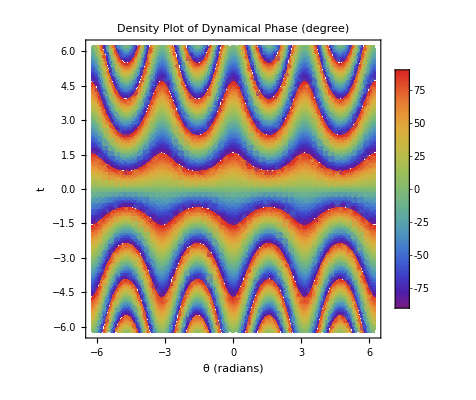

```mathematica
DensityPlot[SetPrecision[ftx[x,y]*(180/Pi),50],{x,-6.25,6.25},{y,-6.25,6.25},ColorFunction->"Rainbow",PlotPoints->50,Frame->True,FrameLabel->{Style["θ (radians)",Black,16],Style["t",Black,16]},PlotLabel->Style["Density Plot of Dynamical Phase (degree)",Black,Bold,12],Mesh->False,ColorFunctionScaling->True,PlotLegends->Automatic,FrameStyle->Directive[Black],(*Makes frame darker*)FrameTicksStyle->Directive[Black,8],(*Makes frame ticks darker*)BaseStyle->{FontSize->8}  (*Overall style*)]
```

#### PB phase trial

```mathematica
theta2
```

tan^-1((sin^2(th) sin(2 x)+cos^2(th) sin(x))/(cos^2(th) cos(x)+sin^2(th) cos(2 x)))

```mathematica
theta2cw
```

tan^-1((sin^2(th) sin(2 x)+sin^2(th) sin(5 x)+cos^2(th) sin(x)+cos^2(th) sin(10 x))/(cos^2(th) cos(x)+cos^2(th) cos(10 x)+sin^2(th) cos(2 x)+sin^2(th) cos(5 x)))

```mathematica
phi
```

tan^-1(tan(2 x sin^2(th)+x cos^2(th)))

```mathematica
phicw
```

tan^-1(tan((1.5 x cos^2(th))/(1.01 Abs[sin(th)]^2+1.01 Abs[cos(th)]^2)+(5. x sin^2(th))/(1.01 Abs[sin(th)]^2+1.01 Abs[cos(th)]^2)))

```mathematica
pbp=theta2 - phi
```

tan^-1((sin^2(th) sin(2 x)+cos^2(th) sin(x))/(cos^2(th) cos(x)+sin^2(th) cos(2 x)))-tan^-1(tan(2 x sin^2(th)+x cos^2(th)))

```mathematica
pbpcw= theta2cw - phicw
```

tan^-1((sin^2(th) sin(2 x)+sin^2(th) sin(5 x)+cos^2(th) sin(x)+cos^2(th) sin(10 x))/(cos^2(th) cos(x)+cos^2(th) cos(10 x)+sin^2(th) cos(2 x)+sin^2(th) cos(5 x)))-tan^-1(tan((1.5 x cos^2(th))/(1.01 Abs[sin(th)]^2+1.01 Abs[cos(th)]^2)+(5. x sin^2(th))/(1.01 Abs[sin(th)]^2+1.01 Abs[cos(th)]^2)))

```mathematica
ftx[th_,x_]:= Evaluate[pbp]
ftxcw[th_,x_]:= Evaluate[pbpcw]
```

```mathematica
Manipulate[Plot[{ftx[x,b] *(180/Pi),ftxcw[x,b] *(180/Pi)},{x,-05,05},PlotRange->{{-05,05},{-100,100}},AxesLabel->{"x","f(x)"},PlotLabel->"Plot of f(x) with varying b and c"],{{b,1},0,5}  (*Slider for b*)]
```

```mathematica
Plot3D[ftxcw[x,y],{x,-5,5},{y,-5,5},ColorFunction->"Rainbow",(*Color scheme*)Mesh->None,(*No mesh lines*)PlotRange->All,(*Include all values in plot range*)AxesLabel->{"x","y","f(x,y)"},(*Label axes*)PlotLabel->"Plot of f(x, y) = Sin(Sqrt[x^2 + y^2])",(*Title*)Lighting->"Neutral"      (*Neutral lighting for better visibility*)]
```

-Graphics3D-

```mathematica
DensityPlot[SetPrecision[ftxcw[x,y]*(180/Pi),50],{x,-6.25,6.25},{y,-6.25,6.25},ColorFunction->"Rainbow",PlotPoints->50,Frame->True,PlotRange->All,FrameLabel->{Style["θ (radians)",Black,16],Style["t",Black,16]},PlotLabel->Style["Density Plot of PB Phase (degree)",Black,Bold,12],Mesh->False,ColorFunctionScaling->True,PlotLegends->Automatic,FrameStyle->Directive[Black],(*Makes frame darker*)FrameTicksStyle->Directive[Black,8],(*Makes frame ticks darker*)BaseStyle->{FontSize->8}  (*Overall style*)]
```

-Graphics-

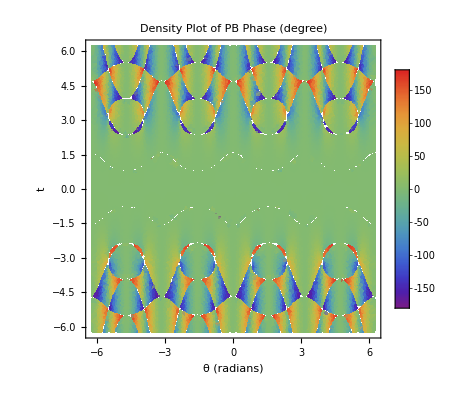

```mathematica
DensityPlot[SetPrecision[ftx[x,y]*(180/Pi),50],{x,-6.25,6.25},{y,-6.25,6.25},ColorFunction->"Rainbow",PlotPoints->50,Frame->True,PlotRange->All,FrameLabel->{Style["θ (radians)",Black,16],Style["t",Black,16]},PlotLabel->Style["Density Plot of PB Phase (degree)",Black,Bold,12],Mesh->False,ColorFunctionScaling->True,PlotLegends->Automatic,FrameStyle->Directive[Black],(*Makes frame darker*)FrameTicksStyle->Directive[Black,8],(*Makes frame ticks darker*)BaseStyle->{FontSize->8}  (*Overall style*)]
```

### Dynamical Phase for Sterile case

#### For Vacuum Case

```mathematica
Nst = 6;
Ust = Table[a,{i,3},{j,Nst}]
```

(a | a | a | a | a | a
a | a | a | a | a | a
a | a | a | a | a | a)

```mathematica
nst=Nst;  (*Define n,the number of elements in the ket vector*)(*Initialize the kett vector*)
kettst=Table[0,{i,nst}]; (*To hold the transformed elements*)
psist=Table[0,{i,3}]; (*To hold the transformed elements*)
psitst=Table[0,{i,3}]; (*To hold the transformed elements*)
```

```mathematica
(*Generate the ket vector with n elements:{ket1,ket2,...,ketn}*)
ketst=Table[Symbol["ketst"<>ToString[i]],{i,1,nst}];
(*Display the generated ket vector*)
ketst
(*Define parameters E1,E2,and t*)
Enst=Table[Symbol["Est"<>ToString[i]],{i,1,nst}];
 (*Energy values*)
tst=tst;        (*Time variable*)


(*Use a loop to define the elements of kett*)
For[i=1,i<=Length[ketst],i++,kettst[[i]]=ketst[[i]]*Exp[-I*Enst[[i]]*tst];];
(*Display the result*)
kettst
(*Defining the mixed states at time t*)
For[i=1,i<=3,i++,{psist[[i]]=Ust[[i]].ketst,psitst[[i]]=Ust[[i]].kettst};];
psist
psitst
```

{ketst1,ketst2,ketst3,ketst4,ketst5,ketst6}

{ketst1 ⅇ^(-ⅈ Est1 tst),ketst2 ⅇ^(-ⅈ Est2 tst),ketst3 ⅇ^(-ⅈ Est3 tst),ketst4 ⅇ^(-ⅈ Est4 tst),ketst5 ⅇ^(-ⅈ Est5 tst),ketst6 ⅇ^(-ⅈ Est6 tst)}

{a ketst1+a ketst2+a ketst3+a ketst4+a ketst5+a ketst6,a ketst1+a ketst2+a ketst3+a ketst4+a ketst5+a ketst6,a ketst1+a ketst2+a ketst3+a ketst4+a ketst5+a ketst6}

{a ketst1 ⅇ^(-ⅈ Est1 tst)+a ketst2 ⅇ^(-ⅈ Est2 tst)+a ketst3 ⅇ^(-ⅈ Est3 tst)+a ketst4 ⅇ^(-ⅈ Est4 tst)+a ketst5 ⅇ^(-ⅈ Est5 tst)+a ketst6 ⅇ^(-ⅈ Est6 tst),a ketst1 ⅇ^(-ⅈ Est1 tst)+a ketst2 ⅇ^(-ⅈ Est2 tst)+a ketst3 ⅇ^(-ⅈ Est3 tst)+a ketst4 ⅇ^(-ⅈ Est4 tst)+a ketst5 ⅇ^(-ⅈ Est5 tst)+a ketst6 ⅇ^(-ⅈ Est6 tst),a ketst1 ⅇ^(-ⅈ Est1 tst)+a ketst2 ⅇ^(-ⅈ Est2 tst)+a ketst3 ⅇ^(-ⅈ Est3 tst)+a ketst4 ⅇ^(-ⅈ Est4 tst)+a ketst5 ⅇ^(-ⅈ Est5 tst)+a ketst6 ⅇ^(-ⅈ Est6 tst)}

```mathematica
(*Differentiate psi1 with respect to time*)
dpsist=D[psitst,tst]
```

{-ⅈ a Est1 ketst1 ⅇ^(-ⅈ Est1 tst)-ⅈ a Est2 ketst2 ⅇ^(-ⅈ Est2 tst)-ⅈ a Est3 ketst3 ⅇ^(-ⅈ Est3 tst)-ⅈ a Est4 ketst4 ⅇ^(-ⅈ Est4 tst)-ⅈ a Est5 ketst5 ⅇ^(-ⅈ Est5 tst)-ⅈ a Est6 ketst6 ⅇ^(-ⅈ Est6 tst),-ⅈ a Est1 ketst1 ⅇ^(-ⅈ Est1 tst)-ⅈ a Est2 ketst2 ⅇ^(-ⅈ Est2 tst)-ⅈ a Est3 ketst3 ⅇ^(-ⅈ Est3 tst)-ⅈ a Est4 ketst4 ⅇ^(-ⅈ Est4 tst)-ⅈ a Est5 ketst5 ⅇ^(-ⅈ Est5 tst)-ⅈ a Est6 ketst6 ⅇ^(-ⅈ Est6 tst),-ⅈ a Est1 ketst1 ⅇ^(-ⅈ Est1 tst)-ⅈ a Est2 ketst2 ⅇ^(-ⅈ Est2 tst)-ⅈ a Est3 ketst3 ⅇ^(-ⅈ Est3 tst)-ⅈ a Est4 ketst4 ⅇ^(-ⅈ Est4 tst)-ⅈ a Est5 ketst5 ⅇ^(-ⅈ Est5 tst)-ⅈ a Est6 ketst6 ⅇ^(-ⅈ Est6 tst)}

```mathematica
(*Specify the number of dimensions*)numDimensions=nst;

(*Create a list to store all kets*)
allKets={};

(*Loop to create each ket*)
For[i=1,i<=numDimensions,i++,(*Create a vector of zeros*)tempket=Table[0,{numDimensions}];
(*Set the i-th element to 1*)tempket[[i]]=1;
(*Add the ket to our list*)AppendTo[allKets,tempket];
(*Define a variable for this ket using ToExpression*)ToExpression["ketst"<>ToString[i]<>" = "<>ToString[tempket]];]
```

```mathematica
(*Compute the inner product*)
innerProductst=Conjugate[psitst[[1]]].dpsist[[1]]
```

-ⅈ a Est1 Conjugate[a] ⅇ^(ⅈ Conjugate[(Est1 tst)]-ⅈ Est1 tst)-ⅈ a Est2 Conjugate[a] ⅇ^(ⅈ Conjugate[(Est2 tst)]-ⅈ Est2 tst)-ⅈ a Est3 Conjugate[a] ⅇ^(ⅈ Conjugate[(Est3 tst)]-ⅈ Est3 tst)-ⅈ a Est4 Conjugate[a] ⅇ^(ⅈ Conjugate[(Est4 tst)]-ⅈ Est4 tst)-ⅈ a Est5 Conjugate[a] ⅇ^(ⅈ Conjugate[(Est5 tst)]-ⅈ Est5 tst)-ⅈ a Est6 Conjugate[a] ⅇ^(ⅈ Conjugate[(Est6 tst)]-ⅈ Est6 tst)

```mathematica
(*Specify the number of E variables*)numE=nst;

(*Create the list of Element expressions*)
elementListst=Join[Table[Element[Symbol["Est"<>ToString[i]],Reals],{i,1,numE}],{Element[tst,Reals]}];

(*Display the list*)
Print["Element list: ",elementListst]
refinedExpressionst=Refine[innerProductst,elementListst]//Expand
```

Element list: {Est1∈ℝ,Est2∈ℝ,Est3∈ℝ,Est4∈ℝ,Est5∈ℝ,Est6∈ℝ,tst∈ℝ}

-ⅈ a Est1 Conjugate[a]-ⅈ a Est2 Conjugate[a]-ⅈ a Est3 Conjugate[a]-ⅈ a Est4 Conjugate[a]-ⅈ a Est5 Conjugate[a]-ⅈ a Est6 Conjugate[a]

```mathematica
expr = refinedExpressionst
```

-ⅈ a Est1 Conjugate[a]-ⅈ a Est2 Conjugate[a]-ⅈ a Est3 Conjugate[a]-ⅈ a Est4 Conjugate[a]-ⅈ a Est5 Conjugate[a]-ⅈ a Est6 Conjugate[a]

```mathematica
realpartst=Refine[(Conjugate[expr]+expr)/(2),elementListst]
imaginarypartst=Refine[(Conjugate[expr]-expr)/(2 I),elementListst]//Expand
```

0

a Est1 Conjugate[a]+a Est2 Conjugate[a]+a Est3 Conjugate[a]+a Est4 Conjugate[a]+a Est5 Conjugate[a]+a Est6 Conjugate[a]

### Total Phase for sterile case

```mathematica
innerProductsttot=Table[i+j,{i,3},{j,3}];

(*Compute the all possible inner products for total phase*)
i=1;
While[i<3+1,{j=1;
While[j<3+1,{innerProductsttot[[i,j]]=Conjugate[psitst[[i]]].psist[[j]]//Expand};j++]};i++]
```

```mathematica
(*Specify the number of E variables*)numE=nst;

(*Create the list of Element expressions*)
elementListst=Join[Table[Element[Symbol["Est"<>ToString[i]],Reals],{i,1,numE}],{Element[tst,Reals]}];

(*Display the list*)
Print["Element list: ",elementListst]
refinedExpressionsttot=Refine[innerProductsttot[[1,2]] (*Define inner product states*),elementListst]//Expand
```

Element list: {Est1∈ℝ,Est2∈ℝ,Est3∈ℝ,Est4∈ℝ,Est5∈ℝ,Est6∈ℝ,tst∈ℝ}

a Conjugate[a] ⅇ^(ⅈ Est1 tst)+a Conjugate[a] ⅇ^(ⅈ Est2 tst)+a Conjugate[a] ⅇ^(ⅈ Est3 tst)+a Conjugate[a] ⅇ^(ⅈ Est4 tst)+a Conjugate[a] ⅇ^(ⅈ Est5 tst)+a Conjugate[a] ⅇ^(ⅈ Est6 tst)

```mathematica
expr= ComplexExpand[refinedExpressionsttot]
realpartsttot=Refine[(Conjugate[expr]+expr)/(2),elementListst] //Expand
imaginarypartsttot=Refine[(Conjugate[expr]-expr)/(2 I),elementListst]//Expand
```

ⅈ (a^2 sin(Est1 tst)+a^2 sin(Est2 tst)+a^2 sin(Est3 tst)+a^2 sin(Est4 tst)+a^2 sin(Est5 tst)+a^2 sin(Est6 tst))+a^2 cos(Est1 tst)+a^2 cos(Est2 tst)+a^2 cos(Est3 tst)+a^2 cos(Est4 tst)+a^2 cos(Est5 tst)+a^2 cos(Est6 tst)

-1/2 ⅈ Conjugate[(sin(Est1 tst) a^2+sin(Est2 tst) a^2+sin(Est3 tst) a^2+sin(Est4 tst) a^2+sin(Est5 tst) a^2+sin(Est6 tst) a^2)]+1/2 Conjugate[(cos(Est1 tst) a^2+cos(Est2 tst) a^2+cos(Est3 tst) a^2+cos(Est4 tst) a^2+cos(Est5 tst) a^2+cos(Est6 tst) a^2)]+1/2 ⅈ a^2 sin(Est1 tst)+1/2 a^2 cos(Est1 tst)+1/2 ⅈ a^2 sin(Est2 tst)+1/2 a^2 cos(Est2 tst)+1/2 ⅈ a^2 sin(Est3 tst)+1/2 a^2 cos(Est3 tst)+1/2 ⅈ a^2 sin(Est4 tst)+1/2 a^2 cos(Est4 tst)+1/2 ⅈ a^2 sin(Est5 tst)+1/2 a^2 cos(Est5 tst)+1/2 ⅈ a^2 sin(Est6 tst)+1/2 a^2 cos(Est6 tst)

-1/2 Conjugate[(sin(Est1 tst) a^2+sin(Est2 tst) a^2+sin(Est3 tst) a^2+sin(Est4 tst) a^2+sin(Est5 tst) a^2+sin(Est6 tst) a^2)]-1/2 ⅈ Conjugate[(cos(Est1 tst) a^2+cos(Est2 tst) a^2+cos(Est3 tst) a^2+cos(Est4 tst) a^2+cos(Est5 tst) a^2+cos(Est6 tst) a^2)]-1/2 a^2 sin(Est1 tst)+1/2 ⅈ a^2 cos(Est1 tst)-1/2 a^2 sin(Est2 tst)+1/2 ⅈ a^2 cos(Est2 tst)-1/2 a^2 sin(Est3 tst)+1/2 ⅈ a^2 cos(Est3 tst)-1/2 a^2 sin(Est4 tst)+1/2 ⅈ a^2 cos(Est4 tst)-1/2 a^2 sin(Est5 tst)+1/2 ⅈ a^2 cos(Est5 tst)-1/2 a^2 sin(Est6 tst)+1/2 ⅈ a^2 cos(Est6 tst)

```mathematica
ArcTan[imaginarypartsttot/realpartsttot]
Thetatot= ArcTan[imaginarypartsttot/realpartsttot]/.{Est1->1,Est2->1.5,Est3->0.1,tst->tst}
```

tan^-1((-1/2 Conjugate[(sin(Est1 tst) a^2+sin(Est2 tst) a^2+sin(Est3 tst) a^2+sin(Est4 tst) a^2+sin(Est5 tst) a^2+sin(Est6 tst) a^2)]-1/2 ⅈ Conjugate[(cos(Est1 tst) a^2+cos(Est2 tst) a^2+cos(Est3 tst) a^2+cos(Est4 tst) a^2+cos(Est5 tst) a^2+cos(Est6 tst) a^2)]-1/2 a^2 sin(Est1 tst)+1/2 ⅈ a^2 cos(Est1 tst)-1/2 a^2 sin(Est2 tst)+1/2 ⅈ a^2 cos(Est2 tst)-1/2 a^2 sin(Est3 tst)+1/2 ⅈ a^2 cos(Est3 tst)-1/2 a^2 sin(Est4 tst)+1/2 ⅈ a^2 cos(Est4 tst)-1/2 a^2 sin(Est5 tst)+1/2 ⅈ a^2 cos(Est5 tst)-1/2 a^2 sin(Est6 tst)+1/2 ⅈ a^2 cos(Est6 tst))/(-1/2 ⅈ Conjugate[(sin(Est1 tst) a^2+sin(Est2 tst) a^2+sin(Est3 tst) a^2+sin(Est4 tst) a^2+sin(Est5 tst) a^2+sin(Est6 tst) a^2)]+1/2 Conjugate[(cos(Est1 tst) a^2+cos(Est2 tst) a^2+cos(Est3 tst) a^2+cos(Est4 tst) a^2+cos(Est5 tst) a^2+cos(Est6 tst) a^2)]+1/2 ⅈ a^2 sin(Est1 tst)+1/2 a^2 cos(Est1 tst)+1/2 ⅈ a^2 sin(Est2 tst)+1/2 a^2 cos(Est2 tst)+1/2 ⅈ a^2 sin(Est3 tst)+1/2 a^2 cos(Est3 tst)+1/2 ⅈ a^2 sin(Est4 tst)+1/2 a^2 cos(Est4 tst)+1/2 ⅈ a^2 sin(Est5 tst)+1/2 a^2 cos(Est5 tst)+1/2 ⅈ a^2 sin(Est6 tst)+1/2 a^2 cos(Est6 tst)))

tan^-1((-1/2 Conjugate[(sin(0.1 tst) a^2+sin(tst) a^2+sin(1.5 tst) a^2+sin(Est4 tst) a^2+sin(Est5 tst) a^2+sin(Est6 tst) a^2)]-1/2 ⅈ Conjugate[(cos(0.1 tst) a^2+cos(tst) a^2+cos(1.5 tst) a^2+cos(Est4 tst) a^2+cos(Est5 tst) a^2+cos(Est6 tst) a^2)]-1/2 a^2 sin(Est4 tst)+1/2 ⅈ a^2 cos(Est4 tst)-1/2 a^2 sin(Est5 tst)+1/2 ⅈ a^2 cos(Est5 tst)-1/2 a^2 sin(Est6 tst)+1/2 ⅈ a^2 cos(Est6 tst)-1/2 a^2 sin(0.1 tst)-1/2 a^2 sin(tst)-1/2 a^2 sin(1.5 tst)+1/2 ⅈ a^2 cos(0.1 tst)+1/2 ⅈ a^2 cos(tst)+1/2 ⅈ a^2 cos(1.5 tst))/(-1/2 ⅈ Conjugate[(sin(0.1 tst) a^2+sin(tst) a^2+sin(1.5 tst) a^2+sin(Est4 tst) a^2+sin(Est5 tst) a^2+sin(Est6 tst) a^2)]+1/2 Conjugate[(cos(0.1 tst) a^2+cos(tst) a^2+cos(1.5 tst) a^2+cos(Est4 tst) a^2+cos(Est5 tst) a^2+cos(Est6 tst) a^2)]+1/2 ⅈ a^2 sin(Est4 tst)+1/2 a^2 cos(Est4 tst)+1/2 ⅈ a^2 sin(Est5 tst)+1/2 a^2 cos(Est5 tst)+1/2 ⅈ a^2 sin(Est6 tst)+1/2 a^2 cos(Est6 tst)+1/2 ⅈ a^2 sin(0.1 tst)+1/2 ⅈ a^2 sin(tst)+1/2 ⅈ a^2 sin(1.5 tst)+1/2 a^2 cos(0.1 tst)+1/2 a^2 cos(tst)+1/2 a^2 cos(1.5 tst)))

```mathematica
fnx[tst_]:=Evaluate[Thetatot]

(*Create the interactive plot with sliders for b*)Manipulate[Plot[fnx[x],{x,-10,10},PlotRange->{{-10,10},{-10,10}},AxesLabel->{"x","f(x)"},PlotLabel->"Plot of f(x) with varying b and c"],{{b,1},0,5}  (*Slider for b*)]
```

```mathematica
Total Phase for CW case
```

### Total Phase for CW case

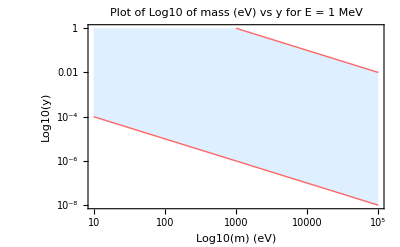

```mathematica
(*Energy=1 MeV,Length for y,L=10^3 Km and for y1,L=1 µm*)y[x_]:=10^(-3)/x
y1[x_]:=10^3/x

LogLogPlot[{y[x],y1[x]},{x,10^1,10^5},PlotLabel->"Plot of Log10 of mass (eV) vs y for E = 1 MeV",AxesLabel->{"Log10(m) (eV)","Log10(y)"},PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick],Directive[RGBColor[1,0.4,0.4],Thick]},Filling->{1->{2}},FillingStyle->LightBlue,AxesStyle->Black,LabelStyle->Directive[Black,Bold],PlotRange->{{10^1,10^5},{Automatic,1}},(*Limit y-axis to≤1*)Frame->True,(*Enable frame*)FrameLabel->{"Log10(m) (eV)","Log10(y)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black,(*Frame color*)FrameTicks->{Table[{10^n,n},{n,1,5}],(*x-axis ticks,none at top*)Table[{10^m,m},{m,-16,3,2}](*y-axis ticks,none at right*)}]
```

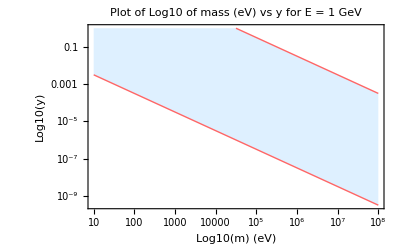

```mathematica
(*Energy=1 GeV,Length for y,L=10^3 Km and for y1,L=1 µm*)y[x_]:=Sqrt[10^(-3)]/x
y1[x_]:=Sqrt[10^9]/x

LogLogPlot[{y[x],y1[x]},{x,10^1,10^8},PlotLabel->"Plot of Log10 of mass (eV) vs y for E = 1 GeV",AxesLabel->{"Log10(m) (eV)","Log10(y)"},PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick],Directive[RGBColor[1,0.4,0.4],Thick]},Filling->{1->{2}},FillingStyle->LightBlue,AxesStyle->Black,LabelStyle->Directive[Black,Bold],PlotRange->{{10^1,10^8},{Automatic,1}},(*Limit y-axis to≤1*)Frame->True,(*Enable frame*)FrameLabel->{"Log10(m) (eV)","Log10(y)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black,(*Frame color*)FrameTicks->{Table[{10^n,n},{n,1,12}],(*x-axis ticks,none at top*)Table[{10^m,m},{m,-16,3,2}]   (*y-axis ticks,none at right*)}]
```

```mathematica
(*(*Energy=1 PeV,Length for y,L=10^3 Km and for y1,L=1 µm*)y[x_]:=Sqrt[10^(3)]/x
y1[x_]:=Sqrt[10^15]/x

LogLogPlot[{y[x],y1[x]},{x,10^1,10^14},PlotLabel->"Plot of Log10 of mass (eV) vs y for E = 1 PeV",AxesLabel->{"Log10(m) (eV)","Log10(y)"},PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick],Directive[RGBColor[1,0.4,0.4],Thick]},Filling->{1->{2}},FillingStyle->LightBlue,AxesStyle->Black,LabelStyle->Directive[Black,Bold],Ticks->{Table[{10^n,n},{n,1,15}],(*x-axis ticks*)Table[{10^m,m},{m,-16,3,2}]  (*y-axis ticks,every second tick*)},PlotRange->{{10^1,Automatic},{Automatic,1}}  (*Limit y-axis to 1*)]*)
```

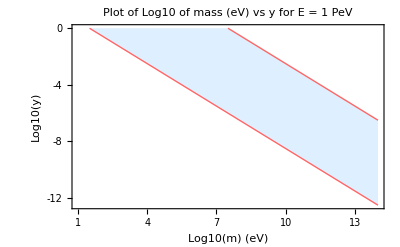

```mathematica
(*Energy=1 PeV,Length for y,L=10^3 Km and for y1,L=1 µm*)y[x_]:=Sqrt[10^(3)]/x
y1[x_]:=Sqrt[10^15]/x

LogLogPlot[{y[x],y1[x]},{x,10^1,10^14},PlotLabel->"Plot of Log10 of mass (eV) vs y for E = 1 PeV",AxesLabel->{"Log10(m) (eV)","Log10(y)"},PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick],Directive[RGBColor[1,0.4,0.4],Thick]},Filling->{1->{2}},FillingStyle->LightBlue,AxesStyle->Black,LabelStyle->Directive[Black,Bold],Ticks->{Table[{10^n,n},{n,1,15}],(*x-axis ticks*)Table[{10^m,m},{m,-16,3,2}]},(*y-axis ticks,every second tick*)PlotRange->{{10^1,Automatic},{Automatic,1}},(*Limit y-axis to≤1*)Frame->True,(*Enable frame*)FrameLabel->{"Log10(m) (eV)","Log10(y)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black,(*Frame color*)FrameTicks->{Table[{10^n,n},{n,1,15}],(*x-axis ticks*)Table[{10^m,m},{m,-16,3,2}]}  (*y-axis ticks,every second tick*)]
```

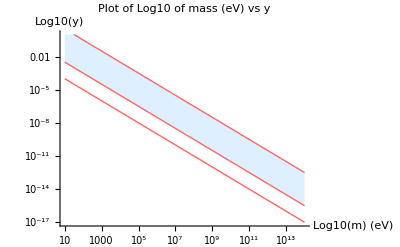

```mathematica
(*Energy=1 PeV,Length for y,L=10^3 Km and for y1,L=1 µm*)
y2[x_]:=Sqrt[10^(3)]/x
y3[x_]:=Sqrt[10^(-3)]/x
y4[x_]:=Sqrt[10^(-6)]/x

LogLogPlot[{y2[x],y3[x],y4[x]},{x,10^1,10^14},PlotLabel->"Plot of Log10 of mass (eV) vs y",AxesLabel->{"Log10(m) (eV)","Log10(y)"},PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick],Directive[RGBColor[1,0.4,0.4],Thick]},Filling->{1->{2}},FillingStyle->LightBlue,AxesStyle->Black,LabelStyle->Directive[Black,Bold],Ticks->{Table[{10^n,n},{n,1,15}],(*x-axis ticks*)Table[{10^m,m},{m,-16,3,2}]  (*y-axis ticks,every second tick*)},PlotRange->{{10^1,Automatic},{Automatic,1}}  (*Limit y-axis to≤1*)]
```

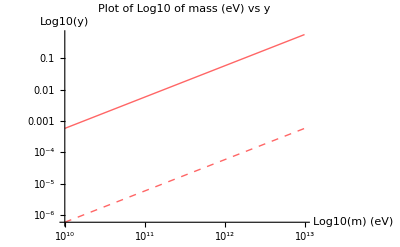

```mathematica
(*Energy=1 PeV,Length for y,L=10^3 Km and for y1,L=1 µm*)ycw[x_]:=10^(-2) x/(0173*10^(9))
y2[x_]:=10^(-8) x/(0.173*10^(9))

LogLogPlot[{ycw[x],y2[x]},{x,10^10,10^13},PlotLabel->"Plot of Log10 of mass (eV) vs y",AxesLabel->{"Log10(m) (eV)","Log10(y)"},PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick],(*ycw[x]-solid line*)Directive[RGBColor[1,0.4,0.4],Dashed,Thick]  (*y2[x]-dashed line*)},AxesStyle->Black,LabelStyle->Directive[Black,Bold],Ticks->{Table[{10^n,n},{n,1,15}],(*x-axis ticks*)Table[{10^n,n},{n,-16,0,1}]  (*y-axis ticks*)},PlotRange->{All,All}  (*Let the y-axis extend automatically*)]
```

#### Clockwork Pheno

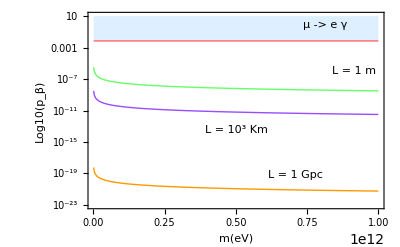

```mathematica
(*Define functions for plotting*)ycw[x_]:=10^(-2)/(Sqrt[2])
y1[x_]:=Sqrt[10^(7)]/x
y3[x_]:=Sqrt[10^1]/x
y4[x_]:=Sqrt[(1/3)*10^(-18)]/x

(*Generate the plot*)
LogPlot[{ycw[x],y1[x],y3[x],y4[x]},{x,1*10^9,1000*10^9},PlotLabel->"",Axes->False,(*Hide default axes to use frame*)Frame->True,(*Enable frame around the plot*)FrameLabel->{"m(eV)","Log10(p_β)",None,None},(*Frame labels*)FrameStyle->Black,(*Frame color*)FrameTicks->{Automatic,(*x-axis ticks*)Table[{10^n,n},{n,-24,3,2}]},(*y-axis ticks every second tick*)(*Solid colors for each curve*)PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick],(*Red for ycw[x]*)Directive[RGBColor[0.4,1,0.4],Thick],(*Light Green for y1[x]*)(*Blue for y2[x]*)Directive[RGBColor[0.6,0.3,1],Thick],(*Purple for y3[x]*)Directive[RGBColor[1,0.6,0],Thick]          (*Orange for y4[x]*)},Filling->{1->Top},(*Fills area above ycw[x]*)FillingStyle->LightBlue,(*Color for the filled area*)LabelStyle->Directive[Black,Bold],PlotRange->{All,{10^(-23),10}},(*Limit y-axis to[10^-20,1000]*)(*Add annotations with Epilog and matching background colors*)Epilog->{(*Main annotation box matching ycw[x] color (red)*)Inset[Framed[Style["μ -> e γ",Black,Bold,9],Background->RGBColor[1,0.4,0.4],RoundingRadius->5],Scaled[{0.8,0.937}]],(*Matching L=1 fm annotation box with y1[x] color (light green)*)Inset[Framed[Style["L = 1 m",Black,Bold,9],Background->RGBColor[0.4,1,0.4],RoundingRadius->5],Scaled[{0.9,0.70}]],(*Matching L=1 μm annotation box with y2[x] color (blue)*)(*Inset[Framed[Style["L = 1 μm",White,Bold,9],Background->RGBColor[0.4,0.4,1],RoundingRadius->5],Scaled[{0.7,0.50}]],(*Matching L=1 μm annotation box with y3[x] color (purple)*)*)Inset[Framed[Style["L = 10^3 Km",White,Bold,9],Background->RGBColor[0.6,0.3,1],RoundingRadius->5],Scaled[{0.5,0.4}]],(*Matching L=10^3 Km annotation box with orange color*)Inset[Framed[Style["L = 1 Gpc",Black,Bold,9],Background->RGBColor[1,0.6,0],RoundingRadius->5],Scaled[{0.7,0.17}]]}]
```

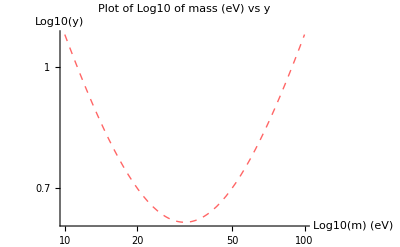

```mathematica
y2[x_]:=10/x +0.01x

LogLogPlot[{y2[x]},{x,10,100},PlotLabel->"Plot of Log10 of mass (eV) vs y",AxesLabel->{"Log10(m) (eV)","Log10(y)"},PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick],(*ycw[x]-solid line*)Directive[RGBColor[1,0.4,0.4],Dashed,Thick]  (*y2[x]-dashed line*)},AxesStyle->Black,LabelStyle->Directive[Black,Bold],Ticks->{Table[{10^n,n},{n,1,15}],(*x-axis ticks*)Table[{10^n,n},{n,-16,0,1}]  (*y-axis ticks*)},PlotRange->{All,All}  (*Let the y-axis extend automatically*)]
```

#### Pheno data Sterile

Sterile GeV

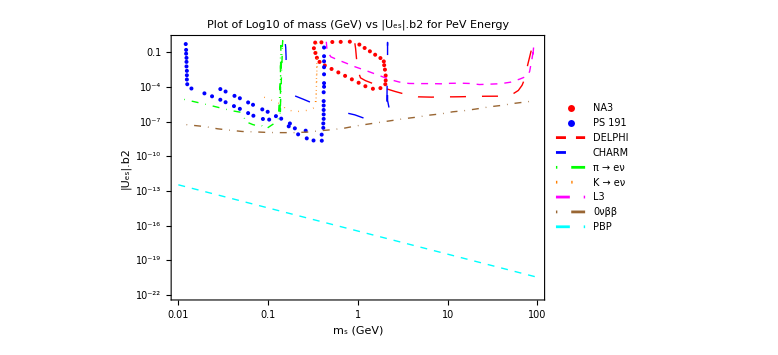

```mathematica
(*Import multiple CSV files*)data1=Import["/home/as/Documents/NA3.csv","CSV"];
data2=Import["/home/as/Documents/DELPHI.csv","CSV"];
data3=Import["/home/as/Documents/CHARM.csv","CSV"];
data4=Import["/home/as/Documents/__e_.csv","CSV"];
data5=Import["/home/as/Documents/newktoe.csv","CSV"];
data6=Import["/home/as/Documents/L3.csv","CSV"];
data7=Import["/home/as/Documents/PS 191.csv","CSV"];
data8=Import["/home/as/Documents/0nubeta.csv","CSV"];

(*Define the analytical function*)
f[x_]:=(1/3)*10^(-16)/x^2

(*Create the data plot*)
dataPlot=ListLogLogPlot[{data1,data7},Joined->False,PlotLabel->Style["Plot of Log10 of mass (GeV) vs |Uₑₛ|.b2 for PeV Energy",Bold,12,Black],PlotStyle->{{Red,PointSize[0.005],Dashing[{0.02,0.02}]},{Blue,PointSize[0.005],Dashing[{0.05,0.05}]}},PlotRange->{{10^-2,10^2},{10^-22,1}},Frame->True,FrameLabel->{Style["mₛ (GeV)",Bold,14],Style["|Uₑₛ|.b2",Bold,14]},FrameStyle->Black,GridLines->Automatic,FrameTicks->{Automatic,Table[{10^n,"10^"<>ToString[n]},{n,-22,0,2}],None,None},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[{"NA3","PS 191"},LegendLayout->{"Column",3}],{0.75,0.45}],ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->8}];
dataPlot2=ListLogLogPlot[{data2,data3,data4,data5,data6,data8},Joined->True,PlotStyle->{{Red,Thick,Dashing[{0.02,0.02}]},{Blue,Thick,Dashing[{0.02,0.05}]},{Green,Thick,DotDashed},{Orange,Thick,Dotted},{Magenta,Thick,Dashed},{Brown,Thick,DotDashed},{Black,Thick,Dashing[{0.02,0.02,0.01,0.02}]}},PlotRange->{{10^-2,10^2},{10^-20,1}},Frame->True,FrameLabel->{Style["mₛ (GeV)",Bold,14],Style["|Uₑₛ|.b2",Bold,14]},FrameStyle->Black,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[{"DELPHI","CHARM","π → eν","K → eν","L3","0νββ"},LegendLayout->{"Column",3}],{0.75,0.35}],ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->8}];
(*Create the function plot*)
functionPlot=LogLogPlot[f[x],{x,10^-2,10^2},PlotStyle->{Cyan,Thick,Dashed},PlotLegends->Placed[LineLegend[{"PBP"},LegendLayout->{"Column",3}],{0.75,0.25}],ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->8}];

(*Combine the plots*)
Show[dataPlot,dataPlot2,functionPlot]
```

Sterile eV

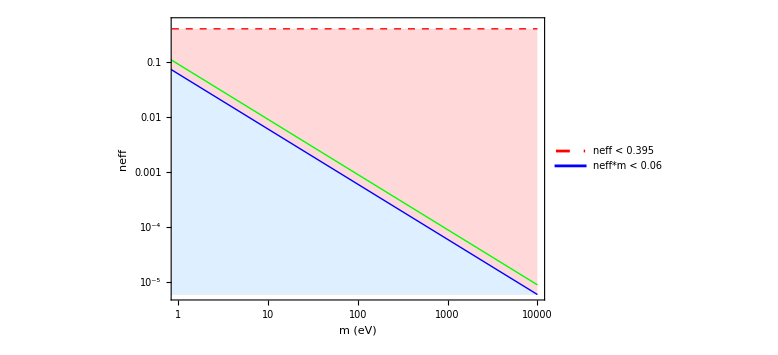

```mathematica
(*Define the ranges for plotting*)Plot[{0.395,(*First constraint:neff<0.395*)0.06/m  (*Second constraint:neff*m<0.06,rearranged as neff<0.06/m*),0.09/m},{m,0.1,10000},(*m range from 0.01 to 1*)PlotRange->{{01,10000},{0,0.5}},Frame->True,FrameLabel->{Style["m (eV)",Bold,14],Style["neff",Bold,14]},PlotStyle->{{Red,Thick,Dashed},{Blue,Thick},{Green,Thick}},Filling->{1->{Axis,LightRed},2->{Axis,LightBlue}},PlotLegends->Placed[LineLegend[{Style["neff < 0.395",Red],Style["neff*m < 0.06",Blue]},LegendLayout->{"Column",1}],{0.85,0.85}],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->12},AxesOrigin->{0,0},ScalingFunctions->{"Log","Log"}  (*Makes both axes logarithmic*)]
```

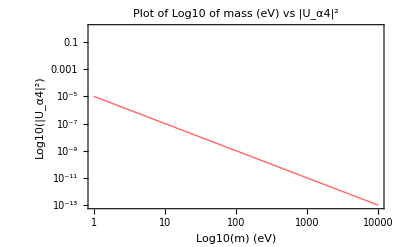

```mathematica
(*Energy=1 10MeV,Length for y,L=10^3 Km and for y1,L=1 µm*)
y2[x_]:=10^(-5)/x^2

LogLogPlot[{y2[x]},{x,10^0,10^4},PlotLabel->"Plot of Log10 of mass (eV) vs |U_α4|^2",Axes->False,(*Hide default axes to use frame*)Frame->True,(*Enable frame around the plot*)FrameLabel->{"Log10(m) (eV)","Log10(|U_α4|^2)",None,None},(*Frame labels*)FrameStyle->Black,(*Frame color*)PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick],Directive[RGBColor[1,0.4,0.4],Thick]},LabelStyle->Directive[Black,Bold],FrameTicks->{Table[{10^n,n},{n,0,15}],(*x-axis ticks*)Table[{10^m,m},{m,-16,3,2}]  (*y-axis ticks,every second tick*)},PlotRange->{{10^0,Automatic},{Automatic,1}}  (*Limit y-axis to≤1*)]
```

#### Extra Dimension Pheno

```mathematica
(* L vs R*) (* Also n vs R*)
```

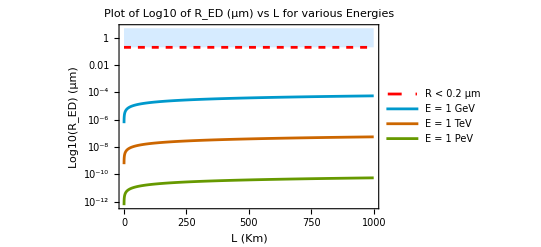

```mathematica
y1[x_]:=Sqrt[10^(-10) 0.2 x/(2 π)]
y2[x_]:=Sqrt[10^(-16) 0.2 x/(2 π)]
y3[x_]:=Sqrt[10^(-22) 0.2 x/(2 π)]

colors={Red,RGBColor[0,0.6,0.8],RGBColor[0.8,0.4,0],RGBColor[0.4,0.6,0]};

LogPlot[{0.2,y1[x],y2[x],y3[x]},{x,0.1,10^3},PlotLabel->"Plot of Log10 of R_ED (μm) vs L for various Energies",Axes->False,Frame->True,FrameLabel->{"L (Km)","Log10(\!\(\*SubscriptBox[\(R\), \(ED\)]\)) (μm)",None,None},FrameStyle->Black,FrameTicks->{Automatic,Table[{10^n,n},{n,-24,3,2}]},Filling->{1->Top},FillingStyle->Directive[Opacity[0.8],RGBColor[0.8,0.9,1]],PlotLegends->Placed[LineLegend[{Style["R < 0.2 μm",colors[[1]]],Style["E = 1 GeV",colors[[2]]],Style["E = 1 TeV",colors[[3]]],Style["E = 1 PeV",colors[[4]]]},LegendLayout->{"Column",1},LegendMarkerSize->10,LabelStyle->{FontSize->8}],{0.85,0.80}],LabelStyle->Directive[Black,Bold],PlotRange->{All,{-14,5}},PlotStyle->{{colors[[1]],Dashed},colors[[2]],colors[[3]],colors[[4]]}]
```

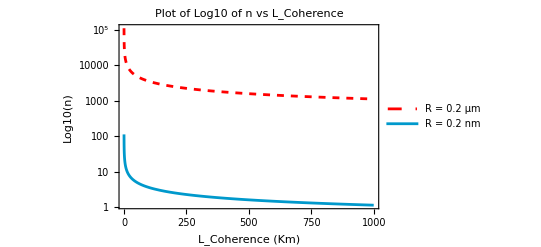

```mathematica
y1[x_]:=Sqrt[10^(9) 2 π 0.2/x]
y2[x_]:=Sqrt[10^(3) 2 π 0.2/x]

colors={Red,RGBColor[0,0.6,0.8],RGBColor[0.8,0.4,0],RGBColor[0.4,0.6,0]};

LogPlot[{y1[x],y2[x]},{x,0.1,10^3},PlotLabel->Labeled["Plot of Log10 of n vs \!\(\*SubscriptBox[\(L\), \(Coherence\)]\)",Spacer[5]],Axes->False,Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(L\), \(Coherence\)]\) (Km)","Log10(n)",None,None},FrameStyle->Black,FrameTicks->{Automatic,Table[{10^n,n},{n,0,15,2}]},PlotLegends->Placed[LineLegend[{Style["R = 0.2 μm",colors[[1]]],Style["R = 0.2 nm",colors[[2]]],Style["E = 1 TeV",colors[[3]]],Style["E = 1 PeV",colors[[4]]]},LegendLayout->{"Column",1},LegendMarkerSize->10,LabelStyle->{FontSize->8}],{0.85,0.80}],LabelStyle->Directive[Black,Bold],PlotRange->{All,All},PlotStyle->{{colors[[1]],Dashed},colors[[2]],colors[[3]],colors[[4]]}]
```

```mathematica
Table[Sqrt[10^(3)2 π 0.2 /x ],{x,1,1400,100}]
```

{35.4491,3.52731,2.50039,2.04325,1.77024,1.58375,1.446,1.33889,1.25253,1.18098,1.12044,1.06834,1.0229,0.982803}

#### total phase trial

```mathematica
theta2 = ArcTan[(uma[[1,1]]^2 * Sin[x]+uma[[1,2]]^2 * Sin[2*x])/(uma[[1,1]]^2 * Cos[x]+uma[[1,2]]^2 * Cos[2*x])]
```

Part::partd: Part specification uma⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification uma⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification uma⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

tan^-1((sin(x) uma⟦1,1⟧^2+sin(2 x) uma⟦1,2⟧^2)/(cos(x) uma⟦1,1⟧^2+cos(2 x) uma⟦1,2⟧^2))

```mathematica
theta2cw = ArcTan[(uma[[1,1]]^2 * Sin[x]+uma[[1,2]]^2 * Sin[2x]+uma[[1,1]]^2 * Sin[01000*x]/1000+uma[[1,2]]^2 * Sin[05*x]/1000)/(uma[[1,1]]^2 * Cos[x]+uma[[1,2]]^2 * Cos[2x]+uma[[1,1]]^2 * Cos[01000*x]/1000+uma[[1,2]]^2 * Cos[05*x]/1000)]
```

Part::partd: Part specification uma⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification uma⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification uma⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

tan^-1((sin(x) uma⟦1,1⟧^2+(sin(1000 x) uma⟦1,1⟧^2)/1000+sin(2 x) uma⟦1,2⟧^2+(sin(5 x) uma⟦1,2⟧^2)/1000)/(cos(x) uma⟦1,1⟧^2+(cos(1000 x) uma⟦1,1⟧^2)/1000+cos(2 x) uma⟦1,2⟧^2+(cos(5 x) uma⟦1,2⟧^2)/1000))

```mathematica
ftx[th_,x_]:= Evaluate[theta2]
ftxcw[th_,x_]:= Evaluate[theta2cw]
```

```mathematica
Manipulate[Plot[{ftx[b,x] *(180/Pi),ftxcw[b,x] *(180/Pi)},{x,-05,05},PlotRange->{{-05,05},{-100,100}},AxesLabel->{"x","f(x)"},PlotLabel->"Plot of f(x) with varying b and c"],{{b,1},0,5}  (*Slider for b*)]
```

```mathematica
Plot3D[ftxcw[x,y],{x,-5,5},{y,-5,5},ColorFunction->"Rainbow",(*Color scheme*)Mesh->None,(*No mesh lines*)PlotRange->All,(*Include all values in plot range*)AxesLabel->{"x","y","f(x,y)"},(*Label axes*)PlotLabel->"Plot of f(x, y) = Sin(Sqrt[x^2 + y^2])",(*Title*)Lighting->"Neutral"      (*Neutral lighting for better visibility*)]
```

-Graphics3D-

```mathematica
DensityPlot[SetPrecision[ftxcw[x,y]*(180/Pi),50],{x,-4.25,4.25},{y,-4.25,4.25},ColorFunction->"Rainbow",PlotPoints->50,Frame->True,FrameLabel->{Style["θ (radians)",Black,16],Style["t",Black,16]},PlotLabel->Style["Density Plot of Total Phase (degree)",Black,Bold,12],Mesh->False,ColorFunctionScaling->True,PlotLegends->Automatic,FrameStyle->Directive[Black],(*Makes frame darker*)FrameTicksStyle->Directive[Black,8],(*Makes frame ticks darker*)BaseStyle->{FontSize->8}  (*Overall style*)]
```

-Graphics-

```mathematica
DensityPlot[SetPrecision[ftx[x,y]*(180/Pi),50],{x,-4.25,4.25},{y,-4.25,4.25},ColorFunction->"Rainbow",PlotPoints->50,Frame->True,FrameLabel->{Style["θ (radians)",Black,16],Style["t",Black,16]},PlotLabel->Style["Density Plot of Total Phase (degree)",Black,Bold,12],Mesh->False,ColorFunctionScaling->True,PlotLegends->Automatic,FrameStyle->Directive[Black],(*Makes frame darker*)FrameTicksStyle->Directive[Black,8],(*Makes frame ticks darker*)BaseStyle->{FontSize->8}  (*Overall style*)]
```

-Graphics-

## PBP constraints Sterile Pheno

```mathematica
delm2[E_,L_]:=Sqrt[4* 0.197*10^(-6) E^3/L] (*E in eV, L in m*)
```

```mathematica
delm2[x,y]
```

0.000887694 √(x^3/y)

### U11

#### Unitary Condition

```mathematica
Y11 = 10^(-3);
Y12 = 10^(-2);
Y13 = 10^(-1);
```

```mathematica
colorList={RGBColor[0.1,0.2,0.8],(*Blue*)RGBColor[0.8,0.1,0.2],(*Red*)RGBColor[0.2,0.8,0.2],(*Green*)RGBColor[0.9,0.6,0.2],(*Orange*)RGBColor[0.6,0.2,0.7],(*Purple*)RGBColor[0.2,0.8,0.8],(*Cyan*)RGBColor[0.9,0.4,0.6],(*Pink*)RGBColor[0.7,0.7,0.2],(*Olive*)RGBColor[0.9,0.5,0.0],(*Amber*)RGBColor[0.1,0.9,0.1],(*Lime*)RGBColor[0.5,0.3,0.0],(*Brown*)RGBColor[0.8,0.0,0.8],(*Magenta*)RGBColor[0.0,0.5,0.5],(*Teal*)RGBColor[1.0,0.84,0.0]   (*Gold*)}
```

{RGBColor[0.1, 0.2, 0.8],RGBColor[0.8, 0.1, 0.2],RGBColor[0.2, 0.8, 0.2],RGBColor[0.9, 0.6, 0.2],RGBColor[0.6, 0.2, 0.7],RGBColor[0.2, 0.8, 0.8],RGBColor[0.9, 0.4, 0.6],RGBColor[0.7, 0.7, 0.2],RGBColor[0.9, 0.5, 0.],RGBColor[0.1, 0.9, 0.1],RGBColor[0.5, 0.3, 0.],RGBColor[0.8, 0., 0.8],RGBColor[0., 0.5, 0.5],RGBColor[1., 0.84, 0.]}

#### SND/FASER (*L = 480m , 100 GeV < E < 2 TeV*)

```mathematica
minsnd=delm2[10^11,480] (*E = 100 GeV*) //Sqrt
```

1.13193×10^6

```mathematica
maxsnd=delm2[10^(12),480] (*E = 1 TeV*) //Sqrt
```

6.36533×10^6

```mathematica
const[E_,L_]:=0.1 E/(1.27L)(*E in GeV, L in Km*)
c1snd=const[10^3,0.48];
c2snd=const[10^2,0.48];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxsnd[x_]:=c1snd/x^2
yminsnd[x_]:=c2snd/x^2
```

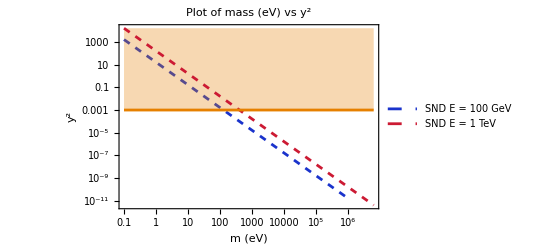

```mathematica
yminsndPlot=LogLogPlot[yminsnd[x],{x,0.1,minsnd},PlotStyle->Directive[colorList[[1]],Dashed],PlotLegends->{Style["SND E = 100 GeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsndPlot=LogLogPlot[{ymaxsnd[x],Y11},{x,0.1,maxsnd},PlotStyle->{Directive[colorList[[2]],Dashed],Directive[colorList[[9]],Thick]},PlotLegends->{Style["SND E = 1 TeV",FontSize->12,FontFamily->"Andika"]},Filling->{2->Top},(*Filling from the second curve to the top*)FillingStyle->Directive[Opacity[0.3],colorList[[9]]] (*Optional style for filling*)];(*Merge the plots*)
sndplot=Show[yminsndPlot,ymaxsndPlot,PlotLabel->"Plot of mass (eV) vs y^2",LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### DANSS (Detector of the reactor AntiNeutrino based on Solid Scintillator) (*L = 10m , 1 MeV < E < 10 MeV*)

```mathematica
mindanss = delm2[10^6,10] (*E = 1MeV*)//Sqrt
```

529.824

```mathematica
maxdanss=delm2[10^(7),10] (*E = 10GeV*)//Sqrt
```

2979.42

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1danss=const[0.01,0.01];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)
c2danss=const[0.001,0.01];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxdanss[x_]:=c1danss/x^2
ymindanss[x_]:=c2danss/x^2
```

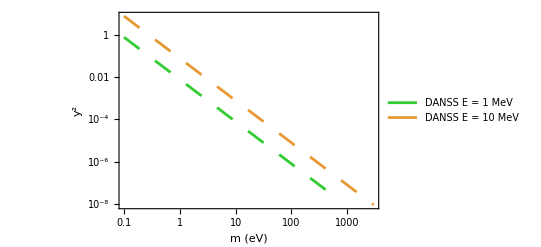

```mathematica
ymindanssPlot=LogLogPlot[ymindanss[x],{x,0.1,mindanss},PlotStyle->Directive[colorList[[3]],Thick,Dashing[Large]],PlotLegends->{Style["DANSS E = 1 MeV",FontSize->12,FontFamily->"Andika"]},PlotRange->All];

ymaxdanssPlot=LogLogPlot[ymaxdanss[x],{x,0.1,maxdanss},PlotStyle->Directive[colorList[[4]],Thick,Dashing[Large]],PlotLegends->{Style["DANSS E = 10 MeV",FontSize->12,FontFamily->"Andika"]},PlotRange->All];
(*Merge the plots*)
danssplot=Show[ymindanssPlot,ymaxdanssPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### SBL (*L = 110m , 100 MeV < E < 10 GeV*)

```mathematica
minsbl=delm2[10^8,110] (*E = 100 MeV*) //Sqrt
```

9199.91

```mathematica
maxsbl=delm2[10^(10),110] (*E = 10 GeV*)//Sqrt
```

290927.

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1sbl=const[10,0.11];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2sbl=const[0.1,0.11];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxsbl[x_]:=c1sbl/x^2
yminsbl[x_]:=c2sbl/x^2
```

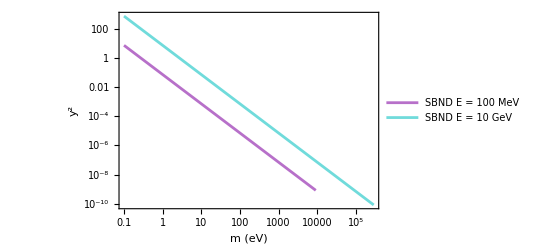

```mathematica
yminsblPlot=LogLogPlot[yminsbl[x],{x,0.1,minsbl},PlotStyle->Directive[colorList[[5]],Thick,Opacity[0.7]],PlotLegends->{Style["SBND E = 100 MeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsblPlot=LogLogPlot[{ymaxsbl[x]},{x,0.1,maxsbl},PlotStyle->{Directive[colorList[[6]],Thick,Opacity[0.7]]},PlotLegends->{Style["SBND E = 10 GeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
sblplot=Show[yminsblPlot,ymaxsblPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### LBL (*L = 1300Km , 1 MeV < E < 10 GeV*)

```mathematica
minlbl=delm2[10^6,1300*10^3] (*E = 1 MeV*) //Sqrt
```

27.9027

```mathematica
maxlbl=delm2[10^(10),1300*10^3] (*E = 10 GeV*)//Sqrt
```

27902.7

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1lbl=const[10,1300];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2lbl=const[0.001,1300];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxlbl[x_]:=c1lbl/x^2
yminlbl[x_]:=c2lbl/x^2
```

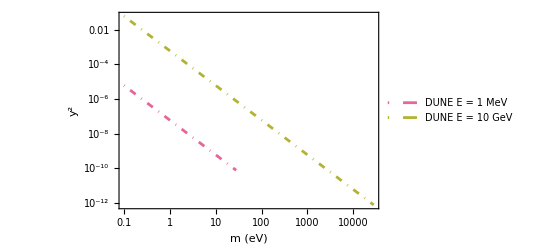

```mathematica
yminlblPlot=LogLogPlot[yminlbl[x],{x,0.1,minlbl},PlotStyle->Directive[colorList[[7]],DotDashed,Thick],PlotLegends->{Style["DUNE E = 1 MeV",FontSize->12,FontFamily->"Andika"]}];

ymaxlblPlot=LogLogPlot[{ymaxlbl[x]},{x,0.1,maxlbl},PlotStyle->{Directive[colorList[[8]],DotDashed,Thick]},PlotLegends->{Style["DUNE E = 10 GeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
lblplot=Show[yminlblPlot,ymaxlblPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### Solar (*L = 10^8Km , 100 KeV < E < 18 MeV*)

```mathematica
minsolar=delm2[10^5,10*10^11] (*E = 1 MeV*) //Sqrt
```

0.167545

```mathematica
maxsolar=delm2[1.8*10^(7),10*10^11] (*E = 10 GeV*)//Sqrt
```

8.23353

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1solar=const[10^-4,10^8];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2solar=const[1.8*10^-2,10^8];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)yminsolar[x_]:=c1solar/x^2
ymaxsolar[x_]:=c2solar/x^2
```

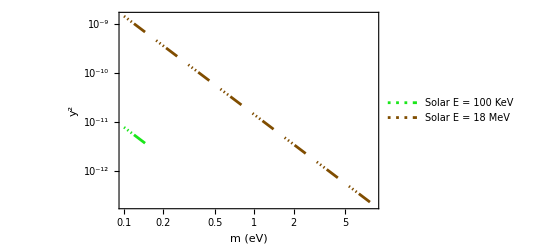

```mathematica
yminsolarPlot=LogLogPlot[yminsolar[x],{x,0.1,minsolar},PlotStyle->Directive[colorList[[10]],AbsoluteDashing[{1,2,1,2,1,2,10,10}],Thick],PlotLegends->{Style["Solar E = 100 KeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsolarPlot=LogLogPlot[{ymaxsolar[x]},{x,0.1,maxsolar},PlotStyle->{Directive[colorList[[11]],AbsoluteDashing[{1,2,1,2,1,2,10,10}],Thick]},PlotLegends->{Style["Solar E = 18 MeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
solarplot=Show[yminsolarPlot,ymaxsolarPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### Astro (*L = 10^25m , 1 TeV < E < 1 PeV*)

```mathematica
minastro=delm2[10^12,10^(25)] (*E = 1 TeV*) //Sqrt
```

16.7545

```mathematica
maxastro=delm2[10^(15),10^25] (*E = 1 PeV*)//Sqrt
```

2979.42

```mathematica
const[E_,L_]:=0.1 E/(1.27L)(*E in GeV, L in Km*)
c1astro=const[10^3,10^22];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2astro=const[10^6,10^22];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)yminastro[x_]:=c1astro/x^2
ymaxastro[x_]:=c2astro/x^2
```

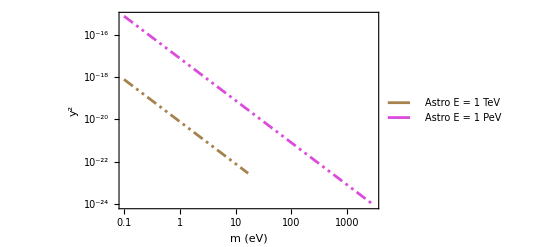

```mathematica
yminastroPlot=LogLogPlot[yminastro[x],{x,0.1,minastro},PlotStyle->Directive[colorList[[11]],AbsoluteDashing[{8,3,2,3,2,3}],Opacity[0.7]],PlotLegends->{Style["Astro E = 1 TeV",FontSize->12,FontFamily->"Andika"]},ClippingStyle->None];

ymaxastroPlot=LogLogPlot[{ymaxastro[x]},{x,0.1,maxastro},PlotStyle->{Directive[colorList[[12]],AbsoluteDashing[{8,3,2,3,2,3}],Opacity[0.7]]},PlotLegends->{Style["Astro E = 1 PeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
astroplot=Show[yminastroPlot,ymaxastroPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,All},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

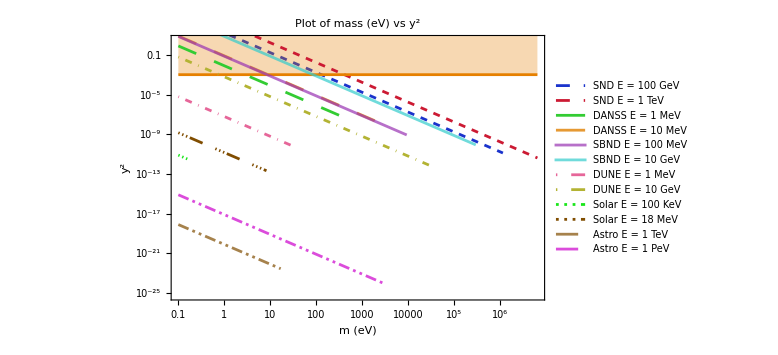

```mathematica
combinedPlot=Show[sndplot,danssplot,sblplot,lblplot,solarplot,astroplot,PlotRange->{All,{-58,1}},(*Use explicit range instead of Automatic*)Frame->True,FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},FrameStyle->Black,LabelStyle->Directive[Black,Bold],PlotRangePadding->None,(*To avoid extra padding*)ImageSize->Large]
```

### U12

#### Unitary Condition

```mathematica
Y11 = 10^(-3);
Y12 = 10^(-2);
Y13 = 10^(-1);
```

```mathematica
colorList={RGBColor[0.1,0.2,0.8],(*Blue*)RGBColor[0.8,0.1,0.2],(*Red*)RGBColor[0.2,0.8,0.2],(*Green*)RGBColor[0.9,0.6,0.2],(*Orange*)RGBColor[0.6,0.2,0.7],(*Purple*)RGBColor[0.2,0.8,0.8],(*Cyan*)RGBColor[0.9,0.4,0.6],(*Pink*)RGBColor[0.7,0.7,0.2],(*Olive*)RGBColor[0.9,0.5,0.0],(*Amber*)RGBColor[0.1,0.9,0.1],(*Lime*)RGBColor[0.5,0.3,0.0],(*Brown*)RGBColor[0.8,0.0,0.8],(*Magenta*)RGBColor[0.0,0.5,0.5],(*Teal*)RGBColor[1.0,0.84,0.0]   (*Gold*)}
```

{RGBColor[0.1, 0.2, 0.8],RGBColor[0.8, 0.1, 0.2],RGBColor[0.2, 0.8, 0.2],RGBColor[0.9, 0.6, 0.2],RGBColor[0.6, 0.2, 0.7],RGBColor[0.2, 0.8, 0.8],RGBColor[0.9, 0.4, 0.6],RGBColor[0.7, 0.7, 0.2],RGBColor[0.9, 0.5, 0.],RGBColor[0.1, 0.9, 0.1],RGBColor[0.5, 0.3, 0.],RGBColor[0.8, 0., 0.8],RGBColor[0., 0.5, 0.5],RGBColor[1., 0.84, 0.]}

#### SND/FASER (*L = 480m , 100 GeV < E < 2 TeV*)

```mathematica
minsnd=delm2[10^11,480] (*E = 100 GeV*) //Sqrt
```

1.13193×10^6

```mathematica
maxsnd=delm2[10^(12),480] (*E = 1 TeV*)//Sqrt
```

6.36533×10^6

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1snd=const[10^3,0.48];
c2snd=const[10^2,0.48];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxsnd[x_]:=c1snd/x^2
yminsnd[x_]:=c2snd/x^2
```

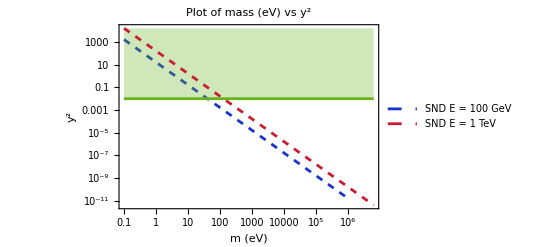

```mathematica
yminsndPlot=LogLogPlot[yminsnd[x],{x,0.1,minsnd},PlotStyle->Directive[colorList[[1]],Dashed],PlotLegends->{Style["SND E = 100 GeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsndPlot=LogLogPlot[{ymaxsnd[x],Y12},{x,0.1,maxsnd},PlotStyle->{Directive[colorList[[2]],Dashed],Directive[RGBColor[0.4,0.7,0.1],Thick]},PlotLegends->{Style["SND E = 1 TeV",FontSize->12,FontFamily->"Andika"]},Filling->{2->Top},(*Filling from the second curve to the top*)FillingStyle->Directive[Opacity[0.3],RGBColor[0.4,0.7,0.1]] (*Optional style for filling*)];(*Merge the plots*)
sndplot=Show[yminsndPlot,ymaxsndPlot,PlotLabel->"Plot of mass (eV) vs y^2",LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### DANSS (Detector of the reactor AntiNeutrino based on Solid Scintillator) (*L = 10m , 1 MeV < E < 10 MeV*)

```mathematica
mindanss = delm2[10^6,10] (*E = 1MeV*)//Sqrt
```

529.824

```mathematica
maxdanss=delm2[10^(7),10] (*E = 10GeV*)//Sqrt
```

2979.42

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1danss=const[0.01,0.01];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)
c2danss=const[0.001,0.01];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxdanss[x_]:=c1danss/x^2
ymindanss[x_]:=c2danss/x^2
```

```mathematica
ymindanssPlot=LogLogPlot[ymindanss[x],{x,0.1,mindanss},PlotStyle->Directive[colorList[[3]],Thick,Dashing[Large]],PlotLegends->{Style["DANSS E = 1 MeV",FontSize->12,FontFamily->"Andika"]},PlotRange->All];

ymaxdanssPlot=LogLogPlot[ymaxdanss[x],{x,0.1,maxdanss},PlotStyle->Directive[colorList[[4]],Thick,Dashing[Large]],PlotLegends->{Style["DANSS E = 10 MeV",FontSize->12,FontFamily->"Andika"]},PlotRange->All];
(*Merge the plots*)
danssplot=Show[ymindanssPlot,ymaxdanssPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

-Graphics-

#### SBL (*L = 110m , 100 MeV < E < 10 GeV*)

```mathematica
minsbl=delm2[10^8,110] (*E = 100 MeV*) //Sqrt
```

9199.91

```mathematica
maxsbl=delm2[10^(10),110] (*E = 10 GeV*)//Sqrt
```

290927.

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1sbl=const[10,0.11];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2sbl=const[0.1,0.11];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxsbl[x_]:=c1sbl/x^2
yminsbl[x_]:=c2sbl/x^2
```

```mathematica
yminsblPlot=LogLogPlot[yminsbl[x],{x,0.1,minsbl},PlotStyle->Directive[colorList[[5]],Thick,Opacity[0.7]],PlotLegends->{Style["SBND E = 100 MeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsblPlot=LogLogPlot[{ymaxsbl[x]},{x,0.1,maxsbl},PlotStyle->{Directive[colorList[[6]],Thick,Opacity[0.7]]},PlotLegends->{Style["SBND E = 10 GeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
sblplot=Show[yminsblPlot,ymaxsblPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

-Graphics-

#### LBL (*L = 1300Km , 1 MeV < E < 10 GeV*)

```mathematica
minlbl=delm2[10^6,1300*10^3] (*E = 1 MeV*) //Sqrt
```

27.9027

```mathematica
maxlbl=delm2[10^(10),1300*10^3] (*E = 10 GeV*)//Sqrt
```

27902.7

```mathematica
const[E_,L_]:=0.1 E/(1.27L)(*E in GeV, L in Km*)
c1lbl=const[10,1300];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2lbl=const[0.001,1300];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxlbl[x_]:=c1lbl/x^2
yminlbl[x_]:=c2lbl/x^2
```

```mathematica
yminlblPlot=LogLogPlot[yminlbl[x],{x,0.1,minlbl},PlotStyle->Directive[colorList[[7]],DotDashed,Thick],PlotLegends->{Style["DUNE E = 1 MeV",FontSize->12,FontFamily->"Andika"]}];

ymaxlblPlot=LogLogPlot[{ymaxlbl[x]},{x,0.1,maxlbl},PlotStyle->{Directive[colorList[[8]],DotDashed,Thick]},PlotLegends->{Style["DUNE E = 10 GeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
lblplot=Show[yminlblPlot,ymaxlblPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

-Graphics-

#### Solar (*L = 10^8Km , 100 KeV < E < 18 MeV*)

```mathematica
minsolar=delm2[10^5,10*10^11] (*E = 1 MeV*) //Sqrt
```

0.167545

```mathematica
maxsolar=delm2[1.8*10^(7),10*10^11] (*E = 10 GeV*)//Sqrt
```

8.23353

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1solar=const[10^-4,10^8];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2solar=const[1.8*10^-2,10^8];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)yminsolar[x_]:=c1solar/x^2
ymaxsolar[x_]:=c2solar/x^2
```

```mathematica
yminsolarPlot=LogLogPlot[yminsolar[x],{x,0.1,minsolar},PlotStyle->Directive[colorList[[10]],AbsoluteDashing[{1,2,1,2,1,2,10,10}],Thick],PlotLegends->{Style["Solar E = 100 KeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsolarPlot=LogLogPlot[{ymaxsolar[x]},{x,0.1,maxsolar},PlotStyle->{Directive[colorList[[11]],AbsoluteDashing[{1,2,1,2,1,2,10,10}],Thick]},PlotLegends->{Style["Solar E = 18 MeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
solarplot=Show[yminsolarPlot,ymaxsolarPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

-Graphics-

#### Astro (*L = 10^25m , 1 TeV < E < 1 PeV*)

```mathematica
minastro=delm2[10^12,10^(25)] (*E = 1 TeV*) //Sqrt
```

16.7545

```mathematica
maxastro=delm2[10^(15),10^25] (*E = 1 PeV*)//Sqrt
```

2979.42

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1astro=const[10^3,10^22];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2astro=const[10^6,10^22];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)yminastro[x_]:=c1astro/x^2
ymaxastro[x_]:=c2astro/x^2
```

```mathematica
yminastroPlot=LogLogPlot[yminastro[x],{x,0.1,minastro},PlotStyle->Directive[colorList[[11]],AbsoluteDashing[{8,3,2,3,2,3}],Opacity[0.7]],PlotLegends->{Style["Astro E = 1 TeV",FontSize->12,FontFamily->"Andika"]},ClippingStyle->None];

ymaxastroPlot=LogLogPlot[{ymaxastro[x]},{x,0.1,maxastro},PlotStyle->{Directive[colorList[[12]],AbsoluteDashing[{8,3,2,3,2,3}],Opacity[0.7]]},PlotLegends->{Style["Astro E = 1 PeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
astroplot=Show[yminastroPlot,ymaxastroPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

-Graphics-

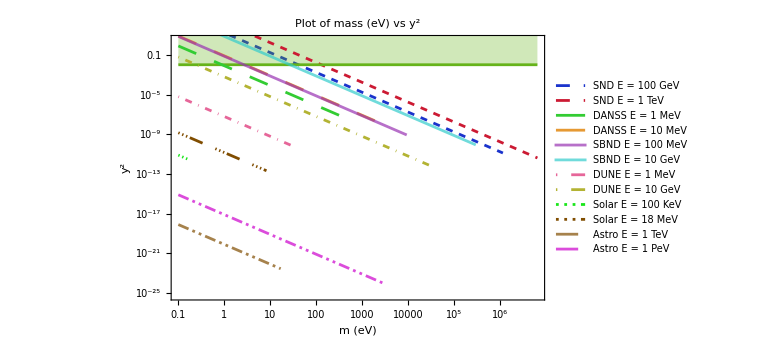

```mathematica
combinedPlot=Show[sndplot,danssplot,sblplot,lblplot,solarplot,astroplot,PlotRange->{All,{-58,1}},(*Use explicit range instead of Automatic*)Frame->True,FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},FrameStyle->Black,LabelStyle->Directive[Black,Bold],PlotRangePadding->None,(*To avoid extra padding*)ImageSize->Large]
```

### U13

#### Unitary Condition

```mathematica
Y11 = 10^(-3);
Y12 = 10^(-2);
Y13 = 10^(-1);
```

```mathematica
colorList={RGBColor[0.1,0.2,0.8],(*Blue*)RGBColor[0.8,0.1,0.2],(*Red*)RGBColor[0.2,0.8,0.2],(*Green*)RGBColor[0.9,0.6,0.2],(*Orange*)RGBColor[0.6,0.2,0.7],(*Purple*)RGBColor[0.2,0.8,0.8],(*Cyan*)RGBColor[0.9,0.4,0.6],(*Pink*)RGBColor[0.7,0.7,0.2],(*Olive*)RGBColor[0.9,0.5,0.0],(*Amber*)RGBColor[0.1,0.9,0.1],(*Lime*)RGBColor[0.5,0.3,0.0],(*Brown*)RGBColor[0.8,0.0,0.8],(*Magenta*)RGBColor[0.0,0.5,0.5],(*Teal*)RGBColor[1.0,0.84,0.0]   (*Gold*)}
```

{RGBColor[0.1, 0.2, 0.8],RGBColor[0.8, 0.1, 0.2],RGBColor[0.2, 0.8, 0.2],RGBColor[0.9, 0.6, 0.2],RGBColor[0.6, 0.2, 0.7],RGBColor[0.2, 0.8, 0.8],RGBColor[0.9, 0.4, 0.6],RGBColor[0.7, 0.7, 0.2],RGBColor[0.9, 0.5, 0.],RGBColor[0.1, 0.9, 0.1],RGBColor[0.5, 0.3, 0.],RGBColor[0.8, 0., 0.8],RGBColor[0., 0.5, 0.5],RGBColor[1., 0.84, 0.]}

#### SND/FASER (*L = 480m , 100 GeV < E < 2 TeV*)

```mathematica
minsnd=delm2[10^11,480] (*E = 100 GeV*) //Sqrt
```

1.13193×10^6

```mathematica
maxsnd=delm2[10^(12),480] (*E = 1 TeV*)//Sqrt
```

6.36533×10^6

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1snd=const[10^3,0.48];
c2snd=const[10^2,0.48];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxsnd[x_]:=c1snd/x^2
yminsnd[x_]:=c2snd/x^2
```

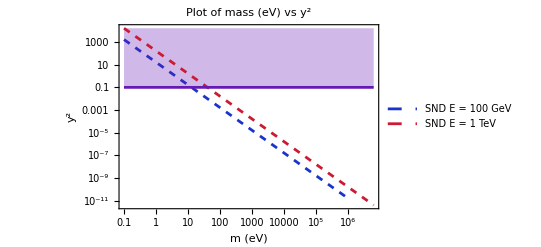

```mathematica
yminsndPlot=LogLogPlot[yminsnd[x],{x,0.1,minsnd},PlotStyle->Directive[colorList[[1]],Dashed],PlotLegends->{Style["SND E = 100 GeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsndPlot=LogLogPlot[{ymaxsnd[x],Y13},{x,0.1,maxsnd},PlotStyle->{Directive[colorList[[2]],Dashed],Directive[RGBColor[0.4,0.1,0.7],Thick]},PlotLegends->{Style["SND E = 1 TeV",FontSize->12,FontFamily->"Andika"]},Filling->{2->Top},(*Filling from the second curve to the top*)FillingStyle->Directive[Opacity[0.3],RGBColor[0.4,0.1,0.7]] (*Optional style for filling*)];(*Merge the plots*)
sndplot=Show[yminsndPlot,ymaxsndPlot,PlotLabel->"Plot of mass (eV) vs y^2",LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### DANSS (Detector of the reactor AntiNeutrino based on Solid Scintillator) (*L = 10m , 1 MeV < E < 10 MeV*)

```mathematica
mindanss = delm2[10^6,10] (*E = 1MeV*)//Sqrt
```

529.824

```mathematica
maxdanss=delm2[10^(7),10] (*E = 10GeV*)//Sqrt
```

2979.42

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1danss=const[0.01,0.01];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)
c2danss=const[0.001,0.01];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxdanss[x_]:=c1danss/x^2
ymindanss[x_]:=c2danss/x^2
```

```mathematica
ymindanssPlot=LogLogPlot[ymindanss[x],{x,0.1,mindanss},PlotStyle->Directive[colorList[[3]],Thick,Dashing[Large]],PlotLegends->{Style["DANSS E = 1 MeV",FontSize->12,FontFamily->"Andika"]},PlotRange->All];

ymaxdanssPlot=LogLogPlot[ymaxdanss[x],{x,0.1,maxdanss},PlotStyle->Directive[colorList[[4]],Thick,Dashing[Large]],PlotLegends->{Style["DANSS E = 10 MeV",FontSize->12,FontFamily->"Andika"]},PlotRange->All];
(*Merge the plots*)
danssplot=Show[ymindanssPlot,ymaxdanssPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

-Graphics-

#### SBL (*L = 110m , 100 MeV < E < 10 GeV*)

```mathematica
minsbl=delm2[10^8,110] (*E = 100 MeV*) //Sqrt
```

9199.91

```mathematica
maxsbl=delm2[10^(10),110] (*E = 10 GeV*)//Sqrt
```

290927.

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1sbl=const[10,0.11];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2sbl=const[0.1,0.11];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxsbl[x_]:=c1sbl/x^2
yminsbl[x_]:=c2sbl/x^2
```

```mathematica
yminsblPlot=LogLogPlot[yminsbl[x],{x,0.1,minsbl},PlotStyle->Directive[colorList[[5]],Thick,Opacity[0.7]],PlotLegends->{Style["SBND E = 100 MeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsblPlot=LogLogPlot[{ymaxsbl[x]},{x,0.1,maxsbl},PlotStyle->{Directive[colorList[[6]],Thick,Opacity[0.7]]},PlotLegends->{Style["SBND E = 10 GeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
sblplot=Show[yminsblPlot,ymaxsblPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

-Graphics-

#### LBL (*L = 1300Km , 1 MeV < E < 10 GeV*)

```mathematica
minlbl=delm2[10^6,1300*10^3] (*E = 1 MeV*) //Sqrt
```

27.9027

```mathematica
maxlbl=delm2[10^(10),1300*10^3] (*E = 10 GeV*)//Sqrt
```

27902.7

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1lbl=const[10,1300];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2lbl=const[0.001,1300];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)ymaxlbl[x_]:=c1lbl/x^2
yminlbl[x_]:=c2lbl/x^2
```

```mathematica
yminlblPlot=LogLogPlot[yminlbl[x],{x,0.1,minlbl},PlotStyle->Directive[colorList[[7]],DotDashed,Thick],PlotLegends->{Style["DUNE E = 1 MeV",FontSize->12,FontFamily->"Andika"]}];

ymaxlblPlot=LogLogPlot[{ymaxlbl[x]},{x,0.1,maxlbl},PlotStyle->{Directive[colorList[[8]],DotDashed,Thick]},PlotLegends->{Style["DUNE E = 10 GeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
lblplot=Show[yminlblPlot,ymaxlblPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

-Graphics-

#### Solar (*L = 10^8Km , 100 KeV < E < 18 MeV*)

```mathematica
minsolar=delm2[10^5,10*10^11] (*E = 1 MeV*) //Sqrt
```

0.167545

```mathematica
maxsolar=delm2[1.8*10^(7),10*10^11] (*E = 10 GeV*)//Sqrt
```

8.23353

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1solar=const[10^-4,10^8];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2solar=const[1.8*10^-2,10^8];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)yminsolar[x_]:=c1solar/x^2
ymaxsolar[x_]:=c2solar/x^2
```

```mathematica
yminsolarPlot=LogLogPlot[yminsolar[x],{x,0.1,minsolar},PlotStyle->Directive[colorList[[10]],AbsoluteDashing[{1,2,1,2,1,2,10,10}],Thick],PlotLegends->{Style["Solar E = 100 KeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsolarPlot=LogLogPlot[{ymaxsolar[x]},{x,0.1,maxsolar},PlotStyle->{Directive[colorList[[11]],AbsoluteDashing[{1,2,1,2,1,2,10,10}],Thick]},PlotLegends->{Style["Solar E = 18 MeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
solarplot=Show[yminsolarPlot,ymaxsolarPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

-Graphics-

#### Astro (*L = 10^25m , 1 TeV < E < 1 PeV*)

```mathematica
minastro=delm2[10^12,10^(25)] (*E = 1 TeV*) //Sqrt
```

16.7545

```mathematica
maxastro=delm2[10^(15),10^25] (*E = 1 PeV*)//Sqrt
```

2979.42

```mathematica
const[E_,L_]:=0.1 E/(1.27L) (*E in GeV, L in Km*)
c1astro=const[10^3,10^22];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)c2astro=const[10^6,10^22];
(*Energy=1 TeV,Length for y,L=0.48 km and for y1,L=1 µm*)yminastro[x_]:=c1astro/x^2
ymaxastro[x_]:=c2astro/x^2
```

```mathematica
yminastroPlot=LogLogPlot[yminastro[x],{x,0.1,minastro},PlotStyle->Directive[colorList[[11]],AbsoluteDashing[{8,3,2,3,2,3}],Opacity[0.7]],PlotLegends->{Style["Astro E = 1 TeV",FontSize->12,FontFamily->"Andika"]},ClippingStyle->None];

ymaxastroPlot=LogLogPlot[{ymaxastro[x]},{x,0.1,maxastro},PlotStyle->{Directive[colorList[[12]],AbsoluteDashing[{8,3,2,3,2,3}],Opacity[0.7]]},PlotLegends->{Style["Astro E = 1 PeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
astroplot=Show[yminastroPlot,ymaxastroPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

-Graphics-

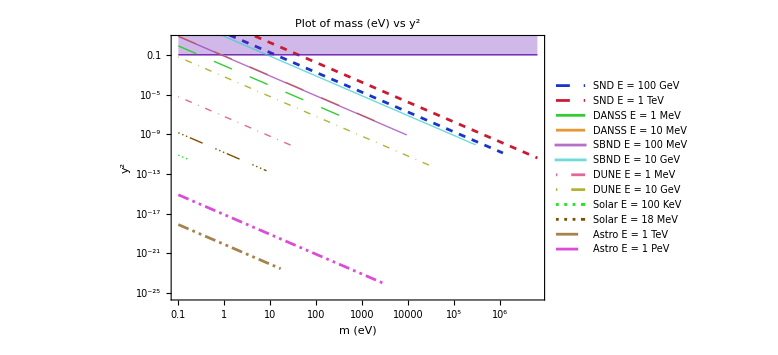

```mathematica
combinedPlot=Show[sndplot,danssplot,sblplot,lblplot,solarplot,astroplot,PlotRange->{All,{-58,1}},(*Use explicit range instead of Automatic*)Frame->True,FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},FrameStyle->Black,LabelStyle->Directive[Black,Bold],PlotRangePadding->None,(*To avoid extra padding*)ImageSize->Large]
```

## Clockwork Pheno

```mathematica
delm2[E_,L_]:=Sqrt[4* 0.197*10^(-6) E^3/L] (*E in eV, L in m*)
delm2[x,y]
```

0.000887694 √(x^3/y)

### Perturbation Validity

```mathematica
v= 246*10^9 (*eV*);
```

```mathematica
pert[m_]:=m/v (*m in eV*)
colorList={RGBColor[0.1,0.2,0.8],(*Blue*)RGBColor[0.8,0.1,0.2],(*Red*)RGBColor[0.2,0.8,0.2],(*Green*)RGBColor[0.9,0.6,0.2],(*Orange*)RGBColor[0.6,0.2,0.7],(*Purple*)RGBColor[0.2,0.8,0.8],(*Cyan*)RGBColor[0.9,0.4,0.6],(*Pink*)RGBColor[0.7,0.7,0.2],(*Olive*)RGBColor[0.9,0.5,0.0],(*Amber*)RGBColor[0.1,0.9,0.1],(*Lime*)RGBColor[0.5,0.3,0.0],(*Brown*)RGBColor[0.8,0.0,0.8],(*Magenta*)RGBColor[0.0,0.5,0.5],(*Teal*)RGBColor[1.0,0.84,0.0]   (*Gold*)}
```

{RGBColor[0.1, 0.2, 0.8],RGBColor[0.8, 0.1, 0.2],RGBColor[0.2, 0.8, 0.2],RGBColor[0.9, 0.6, 0.2],RGBColor[0.6, 0.2, 0.7],RGBColor[0.2, 0.8, 0.8],RGBColor[0.9, 0.4, 0.6],RGBColor[0.7, 0.7, 0.2],RGBColor[0.9, 0.5, 0.],RGBColor[0.1, 0.9, 0.1],RGBColor[0.5, 0.3, 0.],RGBColor[0.8, 0., 0.8],RGBColor[0., 0.5, 0.5],RGBColor[1., 0.84, 0.]}

### y constraints

```mathematica
etolog10 = 2.31;
```

```mathematica
pert[1]//N (*1 eV*)
pert[10^(6)]//N (*1 MeV*)
```

4.06504×10^-12

4.06504×10^-6

```mathematica
lam[k_,N_]:=1+q^2-2 q Cos[(k π)/(N+1)];
```

```mathematica
N1=15; q=3;(*Example size*)
mass=Table[lam[k,N1],{k,1,N1}]//N;
```

```mathematica
sumOfSquares=Total[mass^2]
```

1752.

```mathematica
ycw[E_,L_]:=Sqrt[(0.1/(3*1.27)) (E/L)(1/((sumOfSquares)v^2))] (*E in GeV, L in Km*)
```

#### SND/FASER (*L = 480m , 100 GeV < E < 2 TeV*)

```mathematica
minsnd=delm2[10^11,480] (*E = 100 GeV*) //Sqrt
```

1.13193×10^6

```mathematica
maxsnd=delm2[2*10^(12),480] (*E = 1 TeV*)//Sqrt
```

1.07052×10^7

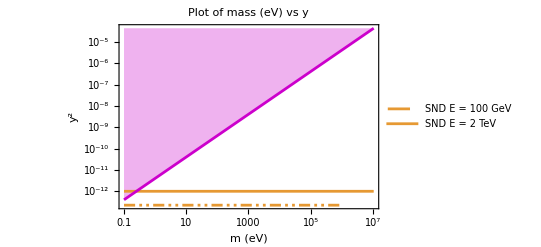

```mathematica
yminsndPlot=LogLogPlot[ycw[100,0.48],{x,0.1,minsnd},PlotStyle->Directive[colorList[[4]],AbsoluteDashing[{8,3,2,3,2,3}]],PlotLegends->{Style["SND E = 100 GeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsndPlot=LogLogPlot[{ycw[2000,0.48],pert[x]},{x,0.1,maxsnd},PlotStyle->{Directive[colorList[[4]],Dashing],Directive[colorList[[12]],Thick]},PlotLegends->{Style["SND E = 2 TeV",FontSize->12,FontFamily->"Andika"]},Filling->{2->Top},(*Filling from the second curve to the top*)FillingStyle->Directive[Opacity[0.3],colorList[[12]]] (*Optional style for filling*)];(*Merge the plots*)
sndplot=Show[yminsndPlot,ymaxsndPlot,PlotLabel->"Plot of mass (eV) vs y",LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### DANSS (Detector of the reactor AntiNeutrino based on Solid Scintillator) (*L = 10m , 1 MeV < E < 10 MeV*)

```mathematica
mindanss = delm2[10^6,10] (*E = 1MeV*)//Sqrt
```

529.824

```mathematica
maxdanss=delm2[10^(7),10] (*E = 10GeV*)//Sqrt
```

2979.42

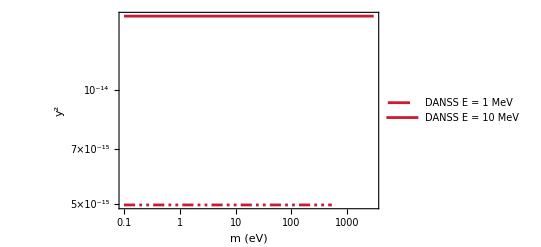

```mathematica
ymindanssPlot=LogLogPlot[ycw[10^-3,0.01],{x,0.1,mindanss},PlotStyle->Directive[colorList[[2]],Thick,AbsoluteDashing[{8,3,2,3,2,3}]],PlotLegends->{Style["DANSS E = 1 MeV",FontSize->12,FontFamily->"Andika"]},PlotRange->All];

ymaxdanssPlot=LogLogPlot[ycw[10^-2,0.01],{x,0.1,maxdanss},PlotStyle->Directive[colorList[[2]],Thick,Dashing],PlotLegends->{Style["DANSS E = 10 MeV",FontSize->12,FontFamily->"Andika"]},PlotRange->All];
(*Merge the plots*)
danssplot=Show[ymindanssPlot,ymaxdanssPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### SBL (*L = 110m , 100 MeV < E < 10 GeV*)

```mathematica
minsbl=delm2[10^8,110] (*E = 100 MeV*) //Sqrt
```

9199.91

```mathematica
maxsbl=delm2[10^(10),110] (*E = 10 GeV*)//Sqrt
```

290927.

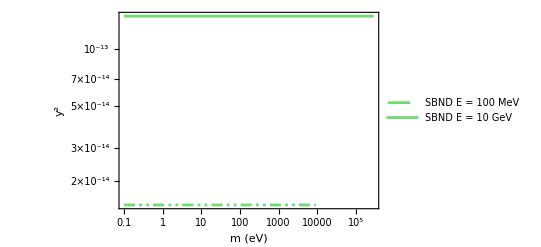

```mathematica
yminsblPlot=LogLogPlot[ycw[0.1,0.110],{x,0.1,minsbl},PlotStyle->Directive[colorList[[3]],AbsoluteDashing[{8,3,2,3,2,3}],Opacity[0.7]],PlotLegends->{Style["SBND E = 100 MeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsblPlot=LogLogPlot[ycw[10,0.110],{x,0.1,maxsbl},PlotStyle->{Directive[colorList[[3]],Dashing,Opacity[0.7]]},PlotLegends->{Style["SBND E = 10 GeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
sblplot=Show[yminsblPlot,ymaxsblPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### LBL (*L = 1300Km , 1 MeV < E < 10 GeV*)

```mathematica
minlbl=delm2[10^6,1300*10^3] (*E = 1 MeV*) //Sqrt
```

27.9027

```mathematica
maxlbl=delm2[10^(10),1300*10^3] (*E = 10 GeV*)//Sqrt
```

27902.7

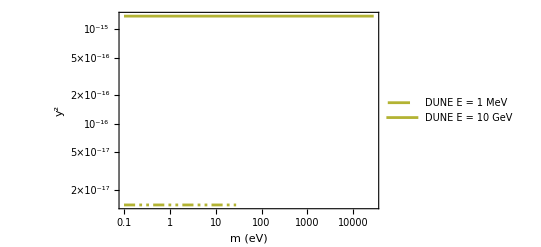

```mathematica
yminlblPlot=LogLogPlot[ycw[10^-3,1300],{x,0.1,minlbl},PlotStyle->Directive[colorList[[8]],AbsoluteDashing[{8,3,2,3,2,3}],Thick],PlotLegends->{Style["DUNE E = 1 MeV",FontSize->12,FontFamily->"Andika"]}];

ymaxlblPlot=LogLogPlot[ycw[10,1300],{x,0.1,maxlbl},PlotStyle->{Directive[colorList[[8]],Dashing,Thick]},PlotLegends->{Style["DUNE E = 10 GeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
lblplot=Show[yminlblPlot,ymaxlblPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### Solar (*L = 10^8Km , 100 KeV < E < 18 MeV*)

```mathematica
minsolar=delm2[10^5,10*10^11] (*E = 1 MeV*) //Sqrt
```

0.167545

```mathematica
maxsolar=delm2[1.8*10^(7),10*10^11] (*E = 10 GeV*)//Sqrt
```

8.23353

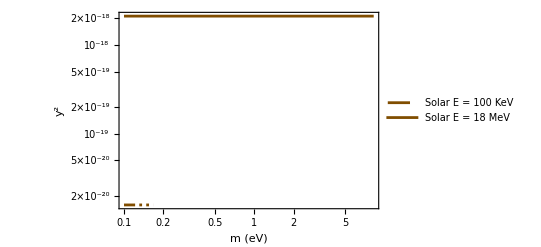

```mathematica
yminsolarPlot=LogLogPlot[ycw[10^-4,10^8],{x,0.1,minsolar},PlotStyle->Directive[colorList[[11]],AbsoluteDashing[{8,3,2,3,2,3}],Thick],PlotLegends->{Style["Solar E = 100 KeV",FontSize->12,FontFamily->"Andika"]}];

ymaxsolarPlot=LogLogPlot[ycw[1.8,10^8],{x,0.1,maxsolar},PlotStyle->{Directive[colorList[[11]],Dashing,Thick]},PlotLegends->{Style["Solar E = 18 MeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
solarplot=Show[yminsolarPlot,ymaxsolarPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(2\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

#### Astro (*L = 10^25m , 1 TeV < E < 1 PeV*)

```mathematica
minastro=delm2[10^12,10^(25)] (*E = 1 TeV*) //Sqrt
```

16.7545

```mathematica
maxastro=delm2[10^(15),10^25] (*E = 1 PeV*)//Sqrt
```

2979.42

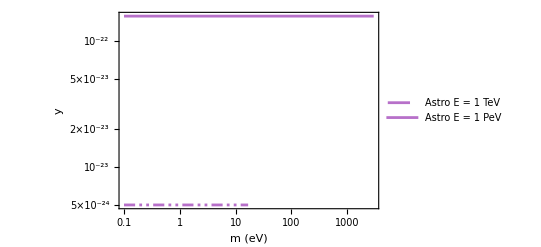

```mathematica
yminastroPlot=LogLogPlot[ycw[10^3,10^22],{x,0.1,minastro},PlotStyle->Directive[colorList[[5]],AbsoluteDashing[{8,3,2,3,2,3}],Opacity[0.7]],PlotLegends->{Style["Astro E = 1 TeV",FontSize->12,FontFamily->"Andika"]},ClippingStyle->None];

ymaxastroPlot=LogLogPlot[ycw[10^6,10^22],{x,0.1,maxastro},PlotStyle->{Directive[colorList[[5]],Dashing,Opacity[0.7]]},PlotLegends->{Style["Astro E = 1 PeV",FontSize->12,FontFamily->"Andika"]}];
(*Merge the plots*)
astroplot=Show[yminastroPlot,ymaxastroPlot,LabelStyle->Directive[Black,Bold],PlotRange->{All,{Automatic,1}},(*Limit y-axis to<=1*)Frame->True,(*Enable frame*)FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(\)]\)",None,None},(*Frame labels for x and y axes*)FrameStyle->Black]
```

```mathematica
ep1={{Opacity[0.3],colorList[[4]],(*Fill color*)EdgeForm[None],(*SND/FASER*)Polygon[{{etolog10*Log10[0.1],etolog10*Log10[ycw[2000,0.48]]},{etolog10*Log10[maxsnd],etolog10*Log10[ycw[2000,0.48]]},{etolog10*Log10[minsnd],etolog10*Log10[ycw[100,0.48]]},{etolog10*Log10[0.1],etolog10*Log10[ycw[100,0.48]]}}]},{Opacity[0.3],colorList[[2]],(*Fill color*)EdgeForm[None],(*DANSS*)Polygon[{{etolog10*Log10[0.1],etolog10*Log10[ycw[10^-2,0.01]]},{etolog10*Log10[maxdanss],etolog10*Log10[ycw[10^-2,0.01]]},{etolog10*Log10[mindanss],etolog10*Log10[ycw[10^-3,0.01]]},{etolog10*Log10[0.1],etolog10*Log10[ycw[10^-3,0.01]]}}]},{Opacity[0.3],colorList[[3]],(*Fill color*)EdgeForm[None],(*SBL*)Polygon[{{etolog10*Log10[0.1],etolog10*Log10[ycw[10,0.110]]},{etolog10*Log10[maxsbl],etolog10*Log10[ycw[10,0.110]]},{etolog10*Log10[minsbl],etolog10*Log10[ycw[0.1,0.110]]},{etolog10*Log10[0.1],etolog10*Log10[ycw[0.1,0.110]]}}]},{Opacity[0.3],colorList[[8]],(*Fill color*)EdgeForm[None],(*LBL*)Polygon[{{etolog10*Log10[0.1],etolog10*Log10[ycw[10,1300]]},{etolog10*Log10[maxlbl],etolog10*Log10[ycw[10,1300]]},{etolog10*Log10[minlbl],etolog10*Log10[ycw[10^-3,1300]]},{etolog10*Log10[0.1],etolog10*Log10[ycw[10^-3,1300]]}}]},{Opacity[0.3],colorList[[11]],(*Fill color*)EdgeForm[None],(*Solar*)Polygon[{{etolog10*Log10[0.1],etolog10*Log10[ycw[1.8,10^8]]},{etolog10*Log10[maxsolar],etolog10*Log10[ycw[1.8,10^8]]},{etolog10*Log10[minsolar],etolog10*Log10[ycw[10^-4,10^8]]},{etolog10*Log10[0.1],etolog10*Log10[ycw[10^-4,10^8]]}}]},{Opacity[0.3],colorList[[5]],(*Fill color*)EdgeForm[None],(*Astro*)Polygon[{{etolog10*Log10[0.1],etolog10*Log10[ycw[10^6,10^22]]},{etolog10*Log10[maxastro],etolog10*Log10[ycw[10^6,10^22]]},{etolog10*Log10[minastro],etolog10*Log10[ycw[10^3,10^22]]},{etolog10*Log10[0.1],etolog10*Log10[ycw[10^3,10^22]]}}]}};
```

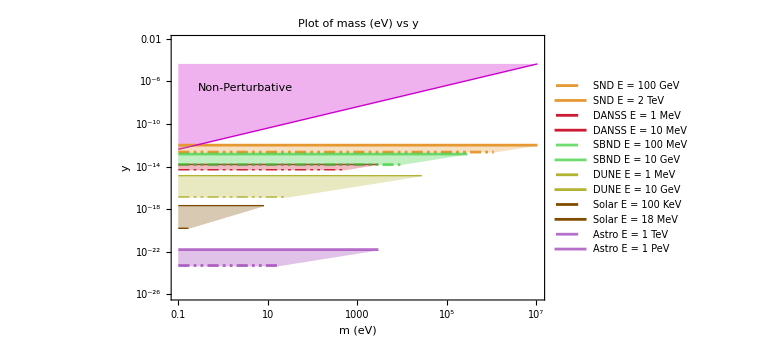

```mathematica
combinedPlot=Show[sndplot,danssplot,sblplot,lblplot,solarplot,astroplot,PlotRange->{All,{-60,-5}},(*Use explicit range instead of Automatic*)Frame->True,FrameLabel->{"m (eV)","\!\(\*SuperscriptBox[\(y\), \(\)]\)",None,None},FrameStyle->Black,LabelStyle->Directive[Black,Bold],PlotRangePadding->None,(*To avoid extra padding*)ImageSize->Large,Epilog->{Inset[Framed[Style["Non-Perturbative",White,Bold,9],Background->colorList[[12]],RoundingRadius->5],Scaled[{0.2,0.80}]],ep1}]
```

```mathematica
pert[1]//N (*1 eV*)
pert[10^(6)]//N (*1 MeV*)
```

4.06504×10^-12

4.06504×10^-6

```mathematica
lam[k_,N_]:=1+q^2-2 q Cos[(k π)/(N+1)];
```

```mathematica
N1=20; q=3;(*Example size*)
mass=Table[lam[k,N1],{k,1,N1}]//N;
```

```mathematica
sumOfSquares=Total[mass^2]
```

2342.

```mathematica
ycw[E_,L_]:=Sqrt[(0.1/3) (E/L)(1/((sumOfSquares)v^2))] (*E in GeV, L in Km*)
```

```mathematica
ycw[1,1]
```

1.5336×10^-14

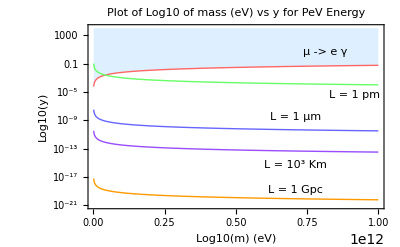

```mathematica
(*Define functions for plotting*)ycw[x_]:=10^(-2)*x/(173*10^(9))
y1[x_]:=Sqrt[10^(16)]/x
y2[x_]:=Sqrt[10^(3)]/x
y3[x_]:=Sqrt[10^(-3)]/x
y4[x_]:=Sqrt[(1/3)*10^(-16)]/x

(*Generate the plot*)
LogPlot[{ycw[x],y1[x],y2[x],y3[x],y4[x]},{x,1*10^9,1000*10^9},PlotLabel->"Plot of Log10 of mass (eV) vs y for PeV Energy",Axes->False,(*Hide default axes to use frame*)Frame->True,(*Enable frame around the plot*)FrameLabel->{"Log10(m) (eV)","Log10(y)",None,None},(*Frame labels*)FrameStyle->Black,(*Frame color*)FrameTicks->{Automatic,(*x-axis ticks*)Table[{10^n,n},{n,-24,3,2}]},(*y-axis ticks every second tick*)(*Solid colors for each curve*)PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick],(*Red for ycw[x]*)Directive[RGBColor[0.4,1,0.4],Thick],(*Light Green for y1[x]*)Directive[RGBColor[0.4,0.4,1],Thick],(*Blue for y2[x]*)Directive[RGBColor[0.6,0.3,1],Thick],(*Purple for y3[x]*)Directive[RGBColor[1,0.6,0],Thick]          (*Orange for y4[x]*)},Filling->{1->Top},(*Fills area above ycw[x]*)FillingStyle->LightBlue,(*Color for the filled area*)LabelStyle->Directive[Black,Bold],PlotRange->{All,{10^(-21),10000}},(*Limit y-axis to[10^-20,1000]*)(*Add annotations with Epilog and matching background colors*)Epilog->{(*Main annotation box matching ycw[x] color (red)*)Inset[Framed[Style["μ -> e γ",Black,Bold,9],Background->RGBColor[1,0.4,0.4],RoundingRadius->5],Scaled[{0.8,0.85}]],(*Matching L=1 fm annotation box with y1[x] color (light green)*)Inset[Framed[Style["L = 1 pm",Black,Bold,9],Background->RGBColor[0.4,1,0.4],RoundingRadius->5],Scaled[{0.9,0.62}]],(*Matching L=1 μm annotation box with y2[x] color (blue)*)Inset[Framed[Style["L = 1 μm",White,Bold,9],Background->RGBColor[0.4,0.4,1],RoundingRadius->5],Scaled[{0.7,0.50}]],(*Matching L=1 μm annotation box with y3[x] color (purple)*)Inset[Framed[Style["L = 10^3 Km",White,Bold,9],Background->RGBColor[0.6,0.3,1],RoundingRadius->5],Scaled[{0.7,0.24}]],(*Matching L=10^3 Km annotation box with orange color*)Inset[Framed[Style["L = 1 Gpc",Black,Bold,9],Background->RGBColor[1,0.6,0],RoundingRadius->5],Scaled[{0.7,0.1}]]}]
```

### Pseudo-Dirac data

```mathematica
log10toe=2.3;
```

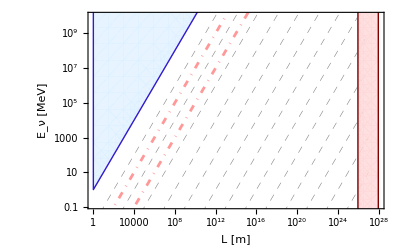

```mathematica
(*Create the main plot*)mainPlot=LogLogPlot[Evaluate@Table[x 10^n,{n,-32,1,2}],{x,10^0,10^27},PlotStyle->Table[{Gray,Dashed,Thickness[0.001]},{n,-32,-8,6}],Frame->True,FrameLabel->{Style["L [m]",FontColor->Black],Style["E_ν [MeV]",FontColor->Black],Style[ Rotate["δm^2",45 Degree],FontSize->14,FontColor->Black]}
,PlotRange->{{10^0,10^27},{10^-2,10^13}},GridLines->Automatic,FrameTicksStyle->Directive[Black],GridLinesStyle->Directive[Gray,Dotted]];

extraPlot1=LogLogPlot[x 10^-3,{x,10^0,10^27},PlotStyle->{RGBColor[1,0.6,0.6]
,DotDashed}];
(*SM flavour oscillation mass squared difference value*)
extraPlot2=LogLogPlot[x 10^-5,{x,10^0,10^27},PlotStyle->{RGBColor[1,0.6,0.6]
,DotDashed}];
(*SM flavour oscillation mass squared difference value*)
mainPlot2=Show[mainPlot,extraPlot1,extraPlot2];

(*Fill the region above y=x*)
filledRegion1=RegionPlot[y>x,{x,10^-2*log10toe,28*log10toe},{y,-2*log10toe,16*log10toe},PlotStyle->Directive[Opacity[0.7],LightBlue],BoundaryStyle->{Thick, RGBColor[0.2,0.1,0.8]},PlotRange->{{0,26},{-2,27}}];
(*Fill the region above x >= Universe Length*)filledRegion2=RegionPlot[x>26*log10toe,{x,10^0*log10toe,28*log10toe},{y,-2*log10toe,16*log10toe},PlotStyle->Directive[Opacity[0.8],LightRed],BoundaryStyle->{Thick, RGBColor[0.5,0,0]},PlotRange->{{1,28},{-2,16}}];
(*Combine the plots*)
plot=Show[mainPlot2,filledRegion1,filledRegion2,PlotRange->{{0.1,28*log10toe},{-2,10*log10toe}}]
```

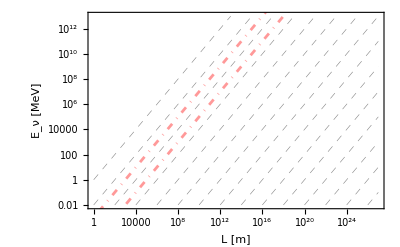

```mathematica
mainPlot2
```

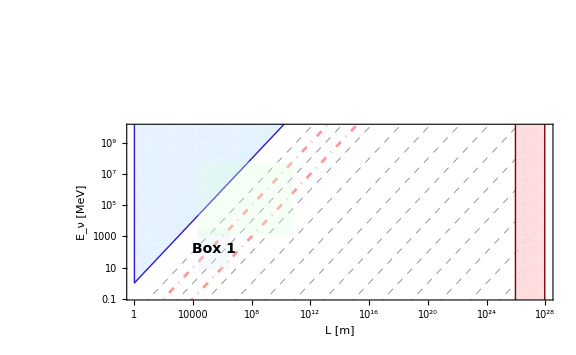

```mathematica
(*Texts For labellings*)
ts = {Text[Rotate[Style["-12",Bold,Black,10],45 Degree],{12.5,35}]};
ts1 = {Text[Rotate[Style["Observable Universe",Bold,Black,10],45 Degree],{12.5,35}]};
ts2 = {Text[Style["Box 1",Bold,Black,14],{12.5,5}]};

(*Region Plot for Experiments.*)
region={{Directive[Opacity[0.3],LightBlue],Rectangle[{10,2},{15,8}]},{Directive[Opacity[0.3],LightGreen],Rectangle[{10,7},{25,18}]}};

Show[plot,Epilog->{region,{ts,ts2}},PlotRange->{{0.1,28*log10toe},{-2,10*log10toe}}]
```

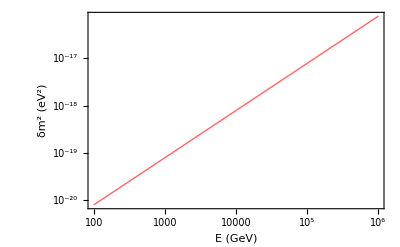

```mathematica
(*Energy=1 MeV,Length for y,L=10^3 Km and for y1,L=1 µm*)y[x_]:=1*x/(1.27*10^(22))
l1=LogLogPlot[{y[x]},{x,10^2,10^6},PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick]},AxesStyle->Black,LabelStyle->Directive[Black,Bold],PlotRange->{All,All},(*Limit y-axis to≤1*)Frame->True,(*Enable frame*)FrameLabel->{"E (GeV)","δm^2 (eV^2) ",None,None},(*Frame labels for x and y axes*)FrameStyle->Black(*Frame color*)]
```

#### Pheno data Sterile

Sterile GeV

```mathematica
log10toe=2.3;
```

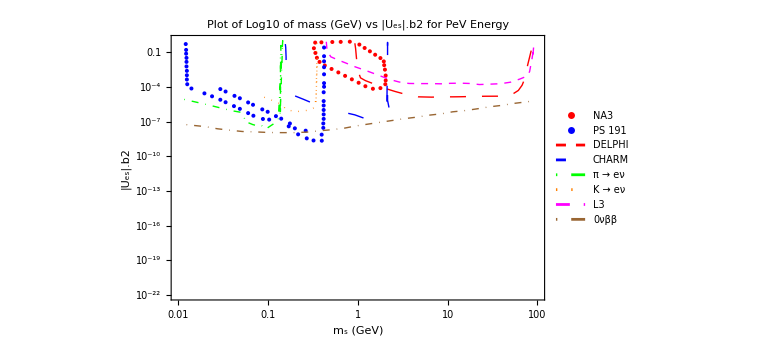

```mathematica
(*Import multiple CSV files*)data1=Import["/home/as/Documents/NA3.csv","CSV"];
data2=Import["/home/as/Documents/DELPHI.csv","CSV"];
data3=Import["/home/as/Documents/CHARM.csv","CSV"];
data4=Import["/home/as/Documents/__e_.csv","CSV"];
data5=Import["/home/as/Documents/newktoe.csv","CSV"];
data6=Import["/home/as/Documents/L3.csv","CSV"];
data7=Import["/home/as/Documents/PS 191.csv","CSV"];
data8=Import["/home/as/Documents/0nubeta.csv","CSV"];

(*Define the analytical function*)
f[x_]:=(1/3)*10^(-19-18)/x^2
g[x_]:=(1/3)*10^(-11-18)/x^2

(*Create the data plot*)
dataPlot=ListLogLogPlot[{data1,data7},Joined->False,PlotLabel->Style["Plot of Log10 of mass (GeV) vs |Uₑₛ|.b2 for PeV Energy",Bold,12,Black],PlotStyle->{{Red,PointSize[0.005],Dashing[{0.02,0.02}]},{Blue,PointSize[0.005],Dashing[{0.05,0.05}]}},PlotRange->{{10^-2,10^2},{10^-22,1}},Frame->True,FrameLabel->{Style["mₛ (GeV)",Bold,14],Style["|Uₑₛ|.b2",Bold,14]},FrameStyle->Black,GridLines->Automatic,FrameTicks->{Automatic,Table[{10^n,"10^"<>ToString[n]},{n,-22,0,2}],None,None},GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[{"NA3","PS 191"},LegendLayout->{"Column",3}],{0.75,0.45}],ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->8}];
dataPlot2=ListLogLogPlot[{data2,data3,data4,data5,data6,data8},Joined->True,PlotStyle->{{Red,Thick,Dashing[{0.02,0.02}]},{Blue,Thick,Dashing[{0.02,0.05}]},{Green,Thick,DotDashed},{Orange,Thick,Dotted},{Magenta,Thick,Dashed},{Brown,Thick,DotDashed},{Black,Thick,Dashing[{0.02,0.02,0.01,0.02}]}},PlotRange->{{10^-2,10^2},{10^-20,1}},Frame->True,FrameLabel->{Style["mₛ (GeV)",Bold,14],Style["|Uₑₛ|.b2",Bold,14]},FrameStyle->Black,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotLegends->Placed[LineLegend[{"DELPHI","CHARM","π → eν","K → eν","L3","0νββ"},LegendLayout->{"Column",3}],{0.75,0.53}],ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->8}];
Show[dataPlot,dataPlot2(*or specify custom ticks*)](*Create the function plot*)
```

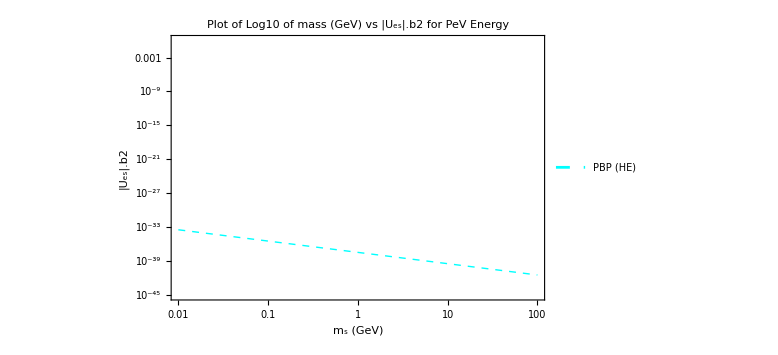

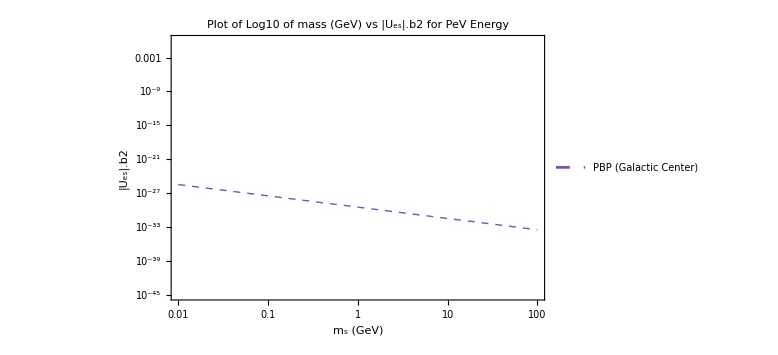

```mathematica
functionPlot=LogLogPlot[f[x],{x,10^-2,10^2},PlotStyle->{Cyan,Thick,Dashed},PlotLabel->Style["Plot of Log10 of mass (GeV) vs |Uₑₛ|.b2 for PeV Energy",Bold,12,Black],PlotLegends->Placed[LineLegend[{"PBP (HE)"},LegendLayout->{"Column",3}],{0.75,0.20}],PlotRange->{{10^-2,10^2},{10^-45,1}},ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->8},GridLines->{Table[10^n,{n,-2,2,1}],(*x gridlines every power of 10*)Table[10^n,{n,-45,0,5}]  (*y gridlines every 5 powers*)},Frame->True,FrameLabel->{Style["mₛ (GeV)",Bold,14],Style["|Uₑₛ|.b2",Bold,14]},FrameStyle->Black,GridLinesStyle->Directive[Gray,Dotted],FrameTicks->{{Table[{10^n,Superscript[10,n]},{n,-45,0,3}],(*y-axis major ticks every 3 powers*)None},{Table[{10^n,Superscript[10,n]},{n,-2,2,1}],(*x-axis major ticks every power*)None}}]

functionPlot2=LogLogPlot[g[x],{x,10^-2,10^2},PlotStyle->{RGBColor[0.5,0.3,0.7],Thick,Dashed},PlotLabel->Style["Plot of Log10 of mass (GeV) vs |Uₑₛ|.b2 for PeV Energy",Bold,12,Black],PlotLegends->Placed[LineLegend[{"PBP (Galactic Center)"},LegendLayout->{"Column",3}],{0.75,0.25}],PlotRange->{{10^-2,10^2},{10^-45,1}},ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->8},GridLines->{Table[10^n,{n,-2,2,1}],(*x gridlines every power of 10*)Table[10^n,{n,-45,0,5}]  (*y gridlines every 5 powers*)},Frame->True,FrameLabel->{Style["mₛ (GeV)",Bold,14],Style["|Uₑₛ|.b2",Bold,14]},FrameStyle->Black,GridLinesStyle->Directive[Gray,Dotted],FrameTicks->{{Table[{10^n,Superscript[10,n]},{n,-45,0,3}],(*y-axis major ticks every 3 powers*)None},{Table[{10^n,Superscript[10,n]},{n,-2,2,1}],(*x-axis major ticks every power*)None}}]
```

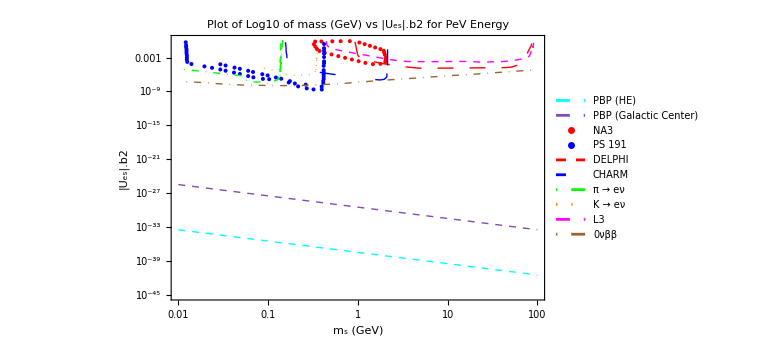

```mathematica
Show[functionPlot,functionPlot2,dataPlot,dataPlot2(*or specify custom ticks*)]
```

Sterile eV

```mathematica
(*Define the ranges for plotting*)Plot[{0.395,(*First constraint:neff<0.395*)0.06/m  (*Second constraint:neff*m<0.06,rearranged as neff<0.06/m*),0.09/m},{m,0.1,10000},(*m range from 0.01 to 1*)PlotRange->{{01,10000},{0,0.5}},Frame->True,FrameLabel->{Style["m (eV)",Bold,14],Style["neff",Bold,14]},PlotStyle->{{Red,Thick,Dashed},{Blue,Thick},{Green,Thick}},Filling->{1->{Axis,LightRed},2->{Axis,LightBlue}},PlotLegends->Placed[LineLegend[{Style["neff < 0.395",Red],Style["neff*m < 0.06",Blue]},LegendLayout->{"Column",1}],{0.85,0.85}],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->12},AxesOrigin->{0,0},ScalingFunctions->{"Log","Log"}  (*Makes both axes logarithmic*)]
```

-Graphics-

```mathematica
(*Energy=1 10MeV,Length for y,L=10^3 Km and for y1,L=1 µm*)
y2[x_]:=10^(-5)/x^2

LogLogPlot[{y2[x]},{x,10^0,10^4},PlotLabel->"Plot of Log10 of mass (eV) vs |U_α4|^2",Axes->False,(*Hide default axes to use frame*)Frame->True,(*Enable frame around the plot*)FrameLabel->{"Log10(m) (eV)","Log10(|U_α4|^2)",None,None},(*Frame labels*)FrameStyle->Black,(*Frame color*)PlotStyle->{Directive[RGBColor[1,0.4,0.4],Thick],Directive[RGBColor[1,0.4,0.4],Thick]},LabelStyle->Directive[Black,Bold],FrameTicks->{Table[{10^n,n},{n,0,15}],(*x-axis ticks*)Table[{10^m,m},{m,-16,3,2}]  (*y-axis ticks,every second tick*)},PlotRange->{{10^0,Automatic},{Automatic,1}}  (*Limit y-axis to≤1*)]
```

-Graphics-

#### Extra Dimension Pheno

```mathematica
(* L vs R*) (* Also n vs R*)
```

```mathematica
y1[x_]:=Sqrt[10^(-10) 0.2 x/(2 π)]
y2[x_]:=Sqrt[10^(-16) 0.2 x/(2 π)]
y3[x_]:=Sqrt[10^(-22) 0.2 x/(2 π)]

colors={Red,RGBColor[0,0.6,0.8],RGBColor[0.8,0.4,0],RGBColor[0.4,0.6,0]};

LogPlot[{0.2,y1[x],y2[x],y3[x]},{x,0.1,10^3},PlotLabel->"Plot of Log10 of R_ED (μm) vs L for various Energies",Axes->False,Frame->True,FrameLabel->{"L (Km)","Log10(\!\(\*SubscriptBox[\(R\), \(ED\)]\)) (μm)",None,None},FrameStyle->Black,FrameTicks->{Automatic,Table[{10^n,n},{n,-24,3,2}]},Filling->{1->Top},FillingStyle->Directive[Opacity[0.8],RGBColor[0.8,0.9,1]],PlotLegends->Placed[LineLegend[{Style["R < 0.2 μm",colors[[1]]],Style["E = 1 GeV",colors[[2]]],Style["E = 1 TeV",colors[[3]]],Style["E = 1 PeV",colors[[4]]]},LegendLayout->{"Column",1},LegendMarkerSize->10,LabelStyle->{FontSize->8}],{0.85,0.80}],LabelStyle->Directive[Black,Bold],PlotRange->{All,{-14,5}},PlotStyle->{{colors[[1]],Dashed},colors[[2]],colors[[3]],colors[[4]]}]
```

-Graphics-

```mathematica
y1[x_]:=Sqrt[10^(9) 2 π 0.2/x]
y2[x_]:=Sqrt[10^(3) 2 π 0.2/x]

colors={Red,RGBColor[0,0.6,0.8],RGBColor[0.8,0.4,0],RGBColor[0.4,0.6,0]};

LogPlot[{y1[x],y2[x]},{x,0.1,10^3},PlotLabel->Labeled["Plot of Log10 of n vs \!\(\*SubscriptBox[\(L\), \(Coherence\)]\)",Spacer[5]],Axes->False,Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(L\), \(Coherence\)]\) (Km)","Log10(n)",None,None},FrameStyle->Black,FrameTicks->{Automatic,Table[{10^n,n},{n,0,15,2}]},PlotLegends->Placed[LineLegend[{Style["R = 0.2 μm",colors[[1]]],Style["R = 0.2 nm",colors[[2]]],Style["E = 1 TeV",colors[[3]]],Style["E = 1 PeV",colors[[4]]]},LegendLayout->{"Column",1},LegendMarkerSize->10,LabelStyle->{FontSize->8}],{0.85,0.80}],LabelStyle->Directive[Black,Bold],PlotRange->{All,All},PlotStyle->{{colors[[1]],Dashed},colors[[2]],colors[[3]],colors[[4]]}]
```

-Graphics-

```mathematica
Table[Sqrt[10^(3)2 π 0.2 /x ],{x,1,1400,100}]
```

{35.4491,3.52731,2.50039,2.04325,1.77024,1.58375,1.446,1.33889,1.25253,1.18098,1.12044,1.06834,1.0229,0.982803}

#### total phase trial

```mathematica
theta2 = ArcTan[(uma[[1,1]]^2 * Sin[x]+uma[[1,2]]^2 * Sin[2*x])/(uma[[1,1]]^2 * Cos[x]+uma[[1,2]]^2 * Cos[2*x])]
```

Part::partd: Part specification uma⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification uma⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification uma⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

tan^-1((sin(x) uma⟦1,1⟧^2+sin(2 x) uma⟦1,2⟧^2)/(cos(x) uma⟦1,1⟧^2+cos(2 x) uma⟦1,2⟧^2))

```mathematica
theta2cw = ArcTan[(uma[[1,1]]^2 * Sin[x]+uma[[1,2]]^2 * Sin[2x]+uma[[1,1]]^2 * Sin[01000*x]/1000+uma[[1,2]]^2 * Sin[05*x]/1000)/(uma[[1,1]]^2 * Cos[x]+uma[[1,2]]^2 * Cos[2x]+uma[[1,1]]^2 * Cos[01000*x]/1000+uma[[1,2]]^2 * Cos[05*x]/1000)]
```

Part::partd: Part specification uma⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification uma⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification uma⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

tan^-1((sin(x) uma⟦1,1⟧^2+(sin(1000 x) uma⟦1,1⟧^2)/1000+sin(2 x) uma⟦1,2⟧^2+(sin(5 x) uma⟦1,2⟧^2)/1000)/(cos(x) uma⟦1,1⟧^2+(cos(1000 x) uma⟦1,1⟧^2)/1000+cos(2 x) uma⟦1,2⟧^2+(cos(5 x) uma⟦1,2⟧^2)/1000))

```mathematica
ftx[th_,x_]:= Evaluate[theta2]
ftxcw[th_,x_]:= Evaluate[theta2cw]
```

```mathematica
Manipulate[Plot[{ftx[b,x] *(180/Pi),ftxcw[b,x] *(180/Pi)},{x,-05,05},PlotRange->{{-05,05},{-100,100}},AxesLabel->{"x","f(x)"},PlotLabel->"Plot of f(x) with varying b and c"],{{b,1},0,5}  (*Slider for b*)]
```

```mathematica
Plot3D[ftxcw[x,y],{x,-5,5},{y,-5,5},ColorFunction->"Rainbow",(*Color scheme*)Mesh->None,(*No mesh lines*)PlotRange->All,(*Include all values in plot range*)AxesLabel->{"x","y","f(x,y)"},(*Label axes*)PlotLabel->"Plot of f(x, y) = Sin(Sqrt[x^2 + y^2])",(*Title*)Lighting->"Neutral"      (*Neutral lighting for better visibility*)]
```

-Graphics3D-

```mathematica
DensityPlot[SetPrecision[ftxcw[x,y]*(180/Pi),50],{x,-4.25,4.25},{y,-4.25,4.25},ColorFunction->"Rainbow",PlotPoints->50,Frame->True,FrameLabel->{Style["θ (radians)",Black,16],Style["t",Black,16]},PlotLabel->Style["Density Plot of Total Phase (degree)",Black,Bold,12],Mesh->False,ColorFunctionScaling->True,PlotLegends->Automatic,FrameStyle->Directive[Black],(*Makes frame darker*)FrameTicksStyle->Directive[Black,8],(*Makes frame ticks darker*)BaseStyle->{FontSize->8}  (*Overall style*)]
```

-Graphics-

```mathematica
DensityPlot[SetPrecision[ftx[x,y]*(180/Pi),50],{x,-4.25,4.25},{y,-4.25,4.25},ColorFunction->"Rainbow",PlotPoints->50,Frame->True,FrameLabel->{Style["θ (radians)",Black,16],Style["t",Black,16]},PlotLabel->Style["Density Plot of Total Phase (degree)",Black,Bold,12],Mesh->False,ColorFunctionScaling->True,PlotLegends->Automatic,FrameStyle->Directive[Black],(*Makes frame darker*)FrameTicksStyle->Directive[Black,8],(*Makes frame ticks darker*)BaseStyle->{FontSize->8}  (*Overall style*)]
```

-Graphics-

## Dynamical Phases (Θ)

### SM Phase

```mathematica
(*Neutrino mixing angles*)θ12=34.0 Degree;
θ23=40.0 Degree;
θ13=9.0 Degree;

(*Neutrino mixing matrix elements*)
Upmns={{Cos[θ12] Cos[θ13],Sin[θ12] Cos[θ13],Sin[θ13]},{-Sin[θ12] Cos[θ23]-Cos[θ12] Sin[θ23] Sin[θ13],Cos[θ12] Cos[θ23]-Sin[θ12] Sin[θ23] Sin[θ13],Sin[θ23] Cos[θ13]},{Sin[θ12] Sin[θ23]-Cos[θ12] Cos[θ23] Sin[θ13],-Cos[θ12] Sin[θ23]-Sin[θ12] Cos[θ23] Sin[θ13],Cos[θ23] Cos[θ13]}};
```

```mathematica
SMTheta[x_,E1_]:=Upmns[[1,1]]^2 * m1^2/(2E1)*x +Upmns[[1,2]]^2 *m2^2/(2E1)*x +Upmns[[1,3]]^2 *m3^2/(2E1)*x ;
```

```mathematica
m1no=0.0298;m2no=0.031;m3no=0.0589(* ∑ Subscript[m, i]<= 0.12 Normal Ordering*); 
m1io=0.0157;m2io=0.0517;m3io=0.0525;(* ∑ Subscript[m, i]<= 0.12 Normal Ordering*)
```

```mathematica
m1=m1no;m2=m2no;m3=m3no;(*m (eV), L (Km), E (GeV)*)
```

### CW Phase

```mathematica
n=39;q=2;(*m (eV), L (Km), E (GeV)*)(*m (eV), L (Km), E (GeV)*)
v=173*Power[10,9]; m =1*Power[10,12] (*1 TeV*);
 y1=0.1*1.1;y2=0.1*1.15;y3=0.1*2.15;
```

```mathematica
p=y1*v/m;p2=y2*v/m;p3=y3*v/m;
```

```mathematica
lambda = Table[1+q^2-2q*Cos[i*π/(n+1)],{i,1,n}]
```

{5-4 cos(π/40),5-4 cos(π/20),5-4 cos((3 π)/40),5-4 √(5/8+(√5)/8),5-4 cos(π/8),5-4 cos((3 π)/20),5-4 cos((7 π)/40),4-√5,5-4 cos((9 π)/40),5-2 √2,5-4 sin((9 π)/40),5-4 √(5/8-(√5)/8),5-4 sin((7 π)/40),5-4 sin((3 π)/20),5-4 sin(π/8),6-√5,5-4 sin((3 π)/40),5-4 sin(π/20),5-4 sin(π/40),5,5+4 sin(π/40),5+4 sin(π/20),5+4 sin((3 π)/40),4+√5,5+4 sin(π/8),5+4 sin((3 π)/20),5+4 sin((7 π)/40),5+4 √(5/8-(√5)/8),5+4 sin((9 π)/40),5+2 √2,5+4 cos((9 π)/40),6+√5,5+4 cos((7 π)/40),5+4 cos((3 π)/20),5+4 cos(π/8),5+4 √(5/8+(√5)/8),5+4 cos((3 π)/40),5+4 cos(π/20),5+4 cos(π/40)}

```mathematica
Ccomp=Table[2*q^2/(lambda[[i]])*Sin[(n*i*π)/(n+1)]^2,{i,1,n}]
```

{(8 sin^2(π/40))/(5-4 cos(π/40)),(8 sin^2(π/20))/(5-4 cos(π/20)),(8 sin^2((3 π)/40))/(5-4 cos((3 π)/40)),(1-√5)^2/(2 (5-4 √(5/8+(√5)/8))),(8 sin^2(π/8))/(5-4 cos(π/8)),(8 sin^2((3 π)/20))/(5-4 cos((3 π)/20)),(8 sin^2((7 π)/40))/(5-4 cos((7 π)/40)),(8 (5/8-(√5)/8))/(4-√5),(8 sin^2((9 π)/40))/(5-4 cos((9 π)/40)),4/(5-2 √2),(8 cos^2((9 π)/40))/(5-4 sin((9 π)/40)),(-1-√5)^2/(2 (5-4 √(5/8-(√5)/8))),(8 cos^2((7 π)/40))/(5-4 sin((7 π)/40)),(8 cos^2((3 π)/20))/(5-4 sin((3 π)/20)),(8 cos^2(π/8))/(5-4 sin(π/8)),(8 (5/8+(√5)/8))/(6-√5),(8 cos^2((3 π)/40))/(5-4 sin((3 π)/40)),(8 cos^2(π/20))/(5-4 sin(π/20)),(8 cos^2(π/40))/(5-4 sin(π/40)),8/5,(8 cos^2(π/40))/(5+4 sin(π/40)),(8 cos^2(π/20))/(5+4 sin(π/20)),(8 cos^2((3 π)/40))/(5+4 sin((3 π)/40)),(8 (5/8+(√5)/8))/(4+√5),(8 cos^2(π/8))/(5+4 sin(π/8)),(8 cos^2((3 π)/20))/(5+4 sin((3 π)/20)),(8 cos^2((7 π)/40))/(5+4 sin((7 π)/40)),(-1-√5)^2/(2 (5+4 √(5/8-(√5)/8))),(8 cos^2((9 π)/40))/(5+4 sin((9 π)/40)),4/(5+2 √2),(8 sin^2((9 π)/40))/(5+4 cos((9 π)/40)),(8 (5/8-(√5)/8))/(6+√5),(8 sin^2((7 π)/40))/(5+4 cos((7 π)/40)),(8 sin^2((3 π)/20))/(5+4 cos((3 π)/20)),(8 sin^2(π/8))/(5+4 cos(π/8)),(1-√5)^2/(2 (5+4 √(5/8+(√5)/8))),(8 sin^2((3 π)/40))/(5+4 cos((3 π)/40)),(8 sin^2(π/20))/(5+4 cos(π/20)),(8 sin^2(π/40))/(5+4 cos(π/40))}

```mathematica
U10=1-p^2/(n+1) *Sum[Ccomp[[i]]/(2*lambda[[i]]),{i,1,n}] (*p = yv/m < 1*)
```

0.99994

```mathematica
U1j=Table[-p*Sqrt[Ccomp[[i]]/((n+1)*lambda[[i]])],{i,1,n}]
```

{-0.000659591,-0.00126885,-0.00178901,-0.00219931,-0.00249664,-0.00269063,-0.00279766,-0.0028359,-0.00282229,-0.00277118,-0.00269395,-0.00259928,-0.00249359,-0.00238153,-0.00226637,-0.0021504,-0.00203514,-0.00192163,-0.00181049,-0.00170209,-0.00159663,-0.00149415,-0.00139461,-0.00129792,-0.00120395,-0.00111252,-0.00102347,-0.000936605,-0.00085175,-0.000768713,-0.000687313,-0.000607369,-0.000528706,-0.000451152,-0.00037454,-0.000298707,-0.000223492,-0.00014874,-0.0000742934}

```mathematica
masscw=Table[m*Sqrt[lambda[[i]](1+ p^2*Ccomp[[i]]/(2(n+1)lambda[[i]]))],{i,1,n}];
```

```mathematica
U2j =U1j/.p->p2;
U3j =U1j/.p->p3;
U20 =U10/.p->p2;
U30 =U10/.p->p3;
masscw2=masscw/.p->p2;
masscw3=masscw/.p->p3;
```

```mathematica
massdivE={m1^2/(2*E1),Table[masscw[[i]]^2/(2*E1),{i,1,n}]}//Flatten;
massdivE2=massdivE /.p->p2;
massdivE3=massdivE /.p->p3;
```

```mathematica
Upmns
```

(0.818831 | 0.552308 | 0.156434
-0.51173 | 0.57885 | 0.634874
0.260094 | -0.599906 | 0.756613)

```mathematica
Utot1=Flatten[{U10,U1j}];
Utot2=Flatten[{U20,U2j}];
Utot3=Flatten[{U30,U3j}];
```

```mathematica
CWTheta[t_,E2_]:=((Evaluate[Sum[Utot1[[i]]^2*massdivE[[i]],{i,1,n+1}]*Upmns[[1,1]]^2+Sum[Utot2[[i]]^2*massdivE2[[i]],{i,1,n+1}]*Upmns[[1,2]]^2+Sum[Utot3[[i]]^2*massdivE3[[i]],{i,1,n+1}]*Upmns[[1,3]]^2] /.E1->E2))*t
```

```mathematica
CW[t_,E2_]:=Evaluate[CWTheta[t,E2]]
```

### Sterile Phase

```mathematica
Usterile=0.01;ms=10;(*m (eV), L (Km), E (GeV)*)
```

```mathematica
SterileTheta[x_,E1_]:=Upmns[[1,1]]^2 * m1^2/(2E1)*x +Upmns[[1,2]]^2 *m2^2/(2E1)*x +Upmns[[1,3]]^2 *m3^2/(2E1)*x +Usterile^2 *( ms^2/(2E1))*x ;
```

```mathematica
SterileTheta[x,y]
```

(0.00548673 x)/y

### Extra Dimension Phase (Approx.)

```mathematica
Clear[m1ED,m2ED,m3ED,RED,n]
```

```mathematica
R=1 (*Same as RED*);En=Power[10,13] (*GeV*);ned=0.01En*R;
```

```mathematica
massED01=m1ED(1-(π^2/6)*(m1ED*RED)^2);
massED02=massED01/.m1ED->m2ED;
massED02=massED01/.m1ED->m3ED;
```

```mathematica
UEDi01=Sqrt[1/(1+1/3*π^2(m1ED*RED)^2)];
UEDi02=UEDi01/.m1ED->m2ED;
UEDi03=UEDi01/.m1ED->m3ED;
```

```mathematica
massdivEED01=UEDi01^2massED01^2/(2*E1);
massdivEED02=massdivEED01/.m1ED->m2ED;
massdivEED03=massdivEED01/.m1ED->m3ED;
```

```mathematica
massdivEEDi1=2m1ED^2/(2*E1);
massdivEEDi2=massdivEEDi1/.m1ED->m2ED;
massdivEEDi3=massdivEEDi1/.m1ED->m3ED;
```

```mathematica
EDThetaapprox[t_,E2_]:=((Evaluate[massdivEED01*Upmns[[1,1]]^2+massdivEED02*Upmns[[1,2]]^2+massdivEED03*Upmns[[1,3]]^2+ned*massdivEEDi1*Upmns[[1,1]]^2+ned*massdivEEDi2*Upmns[[1,2]]^2+ned*massdivEEDi3*Upmns[[1,3]]^2] /.E1->E2))*t
```

```mathematica
m1ED=m1;m2ED=m2;m3ED=m3; (*mR<<1*)RED=1(*1 eV^-1 = 1 μm*);
```

```mathematica
EDapp[x_,y_]:=Evaluate[EDThetaapprox[x,y]];
```

### Extra Dimension Phase (Exact)

```mathematica
Clear[m1ED,m2ED,m3ED,RED,n]
```

```mathematica
R=1 (*Same as RED*);En=Power[10,13] (*GeV*);ned=0.0000000001En*R;
```

```mathematica
massEDi=ParallelTable[(i/RED)(1+(m1ED*RED)^2/(i^2)),{i,1,ned}];(*m (eV), L (Km), E (GeV)*)
massED0=m1ED(1-(π^2/6)*(m1ED*RED)^2);
```

```mathematica
massED={massED0,ParallelTable[massEDi[[i]],{i,1,ned}]}//Flatten;
massED2=massED/.m1ED->m2ED;
massED3=massED/.m1ED->m2ED;
```

```mathematica
UEDij=ParallelTable[Sqrt[2/(1+π^2(m1ED*RED)^2+(massED[[i]]/m1ED)^2)],{i,1,ned+1}];
UEDij2=UEDij/.m1ED->m2ED;
UEDij3=UEDij/.m1ED->m3ED;
```

```mathematica
massdivEED=ParallelTable[massED[[i]]^2/(2*E1),{i,1,ned+1}];
massdivEED2=massdivEED/.m1ED->m2ED;
massdivEED3=massdivEED/.m1ED->m3ED;
```

```mathematica
EDTheta[t_,E2_]:=((Evaluate[Sum[UEDij[[i]]^2*massdivEED[[i]],{i,1,ned+1}]*Upmns[[1,1]]^2+Sum[UEDij2[[i]]^2*massdivEED2[[i]],{i,1,ned+1}]*Upmns[[1,2]]^2+Sum[UEDij3[[i]]^2*massdivEED3[[i]],{i,1,ned+1}]*Upmns[[1,3]]^2] /.E1->E2))*t
```

```mathematica
m1ED=m1;m2ED=m2;m3ED=m3; (*mR<<1*)RED=1(*1 eV^-1 = 1 μm*);
```

```mathematica
ED[x_,y_]:=Evaluate[EDTheta[x,y]];
```

### Pseudo-Dirac Phase

```mathematica
f[x_]:=Mod[x,360]
g[x_]:=Mod[x+x,360]
```

```mathematica
m1pd=0.01*m1;m2pd=0.01*m2;m3pd=0.01*m3;(*m (eV), L (Km), E (GeV)*)
```

```mathematica
PDTheta[x_,E1_]:=Upmns[[1,1]]^2 * m1^2/(2E1)*x +Upmns[[1,2]]^2 *m2^2/(2E1)*x +Upmns[[1,3]]^2 *m3^2/(2E1)*x +Upmns[[1,1]]^2 * m1pd^2/(2E1)*x +Upmns[[1,2]]^2 *m2pd^2/(2E1)*x +Upmns[[1,3]]^2 *m3pd^2/(2E1)*x ;
```

### All Theta Phases

```mathematica
SMTheta[x,1]/.x->100
```

0.0486731

```mathematica
CW[x,1]
```

1.81071×10^20 x

```mathematica
PDTheta[x,1]/.x->100
```

0.048678

```mathematica
SterileTheta[x,1]/.x->100
```

0.548673

```mathematica
Energy = 100000; (*GeV*)
```

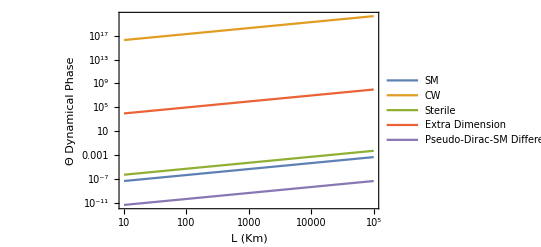

```mathematica
LogLogPlot[{SMTheta[x,Energy],CW[x,Energy],SterileTheta[x,Energy],EDapp[x,Energy],-SMTheta[x,Energy]+PDTheta[x,Energy]},{x,10,100000},PlotLegends->LineLegend[{"SM","CW","Sterile","Extra Dimension","Pseudo-Dirac-SM \n Difference"},LegendFunction->(Framed[#,RoundingRadius->10]&),LabelStyle->{FontSize->7}],PlotRange->All,Frame->True,FrameLabel->{Style["L (Km)",Black,FontSize->10],Style["Θ Dynamical Phase",Black,FontSize->10]},FrameTicksStyle->Black,LabelStyle->{FontSize->12}]
```